```mathematica
CloseKernels[];
LaunchKernels[];
$HistoryLength=0;
ParallelEvaluate[$HistoryLength=0];
```

# Deconvolution via Approximate Maximum Likelihood

## Notation

G, K ∈ ℕ        	— Number of genes/cell types
Φ, σ ∈ ℝ_+^(G×K)  	— Matrix of single cell means/variances
Ψ ∈ ℝ_+^G 		— Bulk means
α ∈ Δ^(K-1) 		— Convex weights
n ∈ ℕ 		— Number of cells in the bulk sample
m ∈ ℕ^K 		— Number of cells  for each cell type in the single cell reference

## General Functions

mixtureσ 		— Variances of an α-mixture of distributions with means Φ and variances σ
ΦVars, αVars 	— Dummy variables used for optimization
rowℒ		— Contribution to likelihood of a single row
ℒ 			— Full Likelihood

```mathematica
mixtureσ[αList_,σRow_,ΦRow_]:=(ΦRow^2+σRow).αList-(ΦRow.αList)^2
```

```mathematica
weightedNorm[vector_,weights_,p_:2]:=Total[vector^p*weights]
```

```mathematica
mMatrix[mList_,G_]:=If[G>1,ConstantArray[mList,G],mList]
```

```mathematica
ℒ[Φ_,ΦObserved_,ΨObserved_,α_,σ_,n_,mList_]:=Total[mMatrix[mList,Length@Φ]/σ*(Φ-ΦObserved)^2,2]+Total[n/(mixtureσ[α,σ,Φ])*(Φ.α-ΨObserved/n)^2]+Total@Log[mixtureσ[α,σ,Φ]*n]
```

```mathematica
ℒJoint[Φ_,ΦObserved_,ΨsObserved_,αs_,σ_,ns_,mList_]:=Total[mMatrix[mList,Length@Φ]/σ*(Φ-ΦObserved)^2,2]+Total[MapThread[(#1/(mixtureσ[#2,σ,Φ])*(Φ.#2-#3/#1)^2)&,{ns,Transpose@αs,Transpose@ΨsObserved}],2]+Total[MapThread[Log[mixtureσ[#2,σ,Φ]*#1]&,{ns,Transpose@αs,Transpose@ΨsObserved}],2]
```

```mathematica
rowℒ[ΦRow_,ΦObservedRow_,ΨObservedScalar_,α_,σRow_,n_,mList_]:=Total[mList/σRow*(ΦRow-ΦObservedRow)^2]+Total[n/(mixtureσ[α,σRow,ΦRow])*(ΦRow.α-ΨObservedScalar/n)^2]+Log[mixtureσ[α,σRow,ΦRow]*n]
```

```mathematica
rowℒJoint[ΦRow_,ΦObservedRow_,ΨObservedScalars_,αs_,σRow_,ns_,mList_]:=Total[mList/σRow*(ΦRow-ΦObservedRow)^2]+Total[MapThread[#1/(mixtureσ[#2,σRow,ΦRow])*(ΦRow.#2-#3/#1)^2&,{ns,Transpose@αs,ΨObservedScalars}],2]+Total[MapThread[Log[mixtureσ[#2,σRow,ΦRow]*#1]&,{ns,Transpose@αs}]]
```

```mathematica
ΦVars[k_]:=Module[{ϕ},Array[ϕ,k]]
```

```mathematica
αVars[k_]:=Module[{α},Array[α,k]]
```

## Updates (1)

minΦRow 	— Optimize one row of Φ for fixed α, mixtureσ
minΦ 		— Iterate minΦRow over rows
minα 		— W-NNLS for fixed Φ, mixtureσ
minαHelper 	— Iterate minα until convergence (ε) or maxIter times
alternate 		— Alternate minΦ and minα until convergence (δ) or maxIter times

```mathematica
nUpdate[Φ_,α_,Ψ_,σ_]:=With[{G=Length@Ψ,A=weightedNorm[Φ.α,1/mixtureσ[α,σ,Φ]],C=weightedNorm[Ψ,1/mixtureσ[α,σ,Φ]]},
-G/(2A)+Sqrt[G^2/(4A^2)+C/A]]
```

```mathematica
minΦRow[ΦVars_,ΦPre_,ΨScalar_,ΦobservedRow_,σRow_,αList_,n_,mList_]:=QuadraticOptimization[Total[mList/σRow(ΦobservedRow-ΦVars)^2+n/(mixtureσ[αList,σRow,ΦPre])(ΦVars.αList-ΨScalar/n)^2],{Thread[ΦVars≥0]},ΦVars]
```

```mathematica
minΦ[ΦVars_,ΦPre_,ΨVec_,ΦMatrixObserved_,σMatrix_,αList_,n_,mList_]:=Parallelize[Table[ΦVars/.minΦRow[ΦVars,#1[[j]],#2[[j]],#3[[j]],#4[[j]],αList,n,mList]&@@{ΦPre,ΨVec,ΦMatrixObserved,σMatrix},{j,1,Length@ΨVec}]]
```

```mathematica
minα[αVars_,αPre_,σMatrix_,ΦMatrix_,ΨVector_,n_]:=αVars/.QuadraticOptimization[(n/mixtureσ[αPre,σMatrix,ΦMatrix]).(ΦMatrix.αVars-ΨVector/n)^2,Thread[αVars≥0]~Join~{Total[αVars]==1},αVars]
```

```mathematica
minαLSHelper[αVars_,αPre_,σMatrix_,ΦMatrix_,ΨVector_,n_,ε_,maxIter_]:=NestWhile[minα[αVars,#,σMatrix,ΦMatrix,ΨVector,n]&,αPre,Norm[#1-#2,2]>ε&,2,maxIter]
```

```mathematica
alternate[Φ_,Ψ_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,αList,ℒPast,ℒNext,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=Φ;
αPast=#/Total[#]&@(#*UnitStep[#]&/@LeastSquares[Φ,Ψ]); (* Initialise with naive least squares solution *)
nPast=Norm[#,1]&@LeastSquares[Φ,Ψ];
ℒPast=ℒ[ΦPast,Φ,Ψ,αPast,σ,nPast,mList];
ΦNext=minΦ[ΦVars[k],ΦPast,Ψ,Φ,σ,αPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

Print["α_0 = ",αPast,", ℒ_0 = ",ℒPast,", n_0 = ",nPast];
Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

If[ℒNext+δ>ℒPast,αNext=αPast];

Monitor[While[Norm[αNext-αPast,Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=minΦ[ΦVars[k],ΦPast,Ψ,Φ,σ,αPast,nNext,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Joint Updates (1)

minΦRow 	— Optimize one row of Φ for fixed α, mixtureσ
minΦ 		— Iterate minΦRow over rows
minα 		— W-NNLS for fixed Φ, mixtureσ
minαHelper 	— Iterate minα until convergence (ε) or maxIter times
alternate 		— Alternate minΦ and minα until convergence (δ) or maxIter times

```mathematica
nUpdateJoint[Φ_,αs_,Ψs_,σ_]:=MapThread[nUpdate[Φ,#1,#2,σ]&,{Transpose@αs,Transpose@Ψs}]
```

```mathematica
minΦRowJoint[ΦVars_,ΦPre_,ΨScalars_,ΦobservedRow_,σRow_,αLists_,ns_,mList_]:=QuadraticOptimization[Total[mList/σRow(ΦobservedRow-ΦVars)^2+Total[MapThread[#3/(mixtureσ[#1,σRow,ΦPre])(ΦVars.#1-#2/#3)^2&,{Transpose@αLists,ΨScalars,ns}]]],{Thread[ΦVars≥0]},ΦVars]
```

```mathematica
minΦJoint[ΦVars_,ΦPre_,ΨVecs_,ΦMatrixObserved_,σMatrix_,αLists_,ns_,mList_]:=Parallelize[Table[ΦVars/.minΦRowJoint[ΦVars,#1[[j]],#2[[j]],#3[[j]],#4[[j]],αLists,ns,mList]&@@{ΦPre,ΨVecs,ΦMatrixObserved,σMatrix},{j,1,Length@ΨVecs}]]
```

```mathematica
minαJoint[αVars_,αsPre_,σMatrix_,ΦMatrix_,ΨVectors_,ns_]:=Transpose@MapThread[minα[αVars,#1,σMatrix,ΦMatrix,#2,#3]&,{Transpose@αsPre,Transpose@ΨVectors,ns}]
```

```mathematica
minαLSHelperJoint[αVars_,αsPre_,σMatrix_,ΦMatrix_,ΨVectors_,ns_,ε_,maxIter_]:=NestWhile[minαJoint[αVars,#,σMatrix,ΦMatrix,ΨVectors,ns]&,αsPre,Norm[Flatten[#1-#2],2]>ε&,2,maxIter]
```

```mathematica
alternateJoint[Φ_,Ψs_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,αList,ℒPast,ℒNext,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=Φ;
αPast=Transpose@Table[#/Total[#]&@(#*UnitStep[#]&/@LeastSquares[Φ,Ψ]),{Ψ,Transpose@Ψs}]; (* Initialise with naive least squares solution *)
nPast=Table[Norm[#,1]&@LeastSquares[Φ,Ψ],{Ψ,Transpose@Ψs}];
ℒPast=ℒJoint[ΦPast,Φ,Ψs,αPast,σ,nPast,mList];
ΦNext=minΦJoint[ΦVars[k],ΦPast,Ψs,Φ,σ,αPast,nPast,mList];
αNext=minαLSHelperJoint[αVars[k],αPast,σ,ΦNext,Ψs,nPast,10^(-4),1];
nNext=nUpdateJoint[ΦNext,αNext,Ψs,σ];
ℒNext=ℒJoint[ΦNext,Φ,Ψs,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

Print["α_0 = ",Transpose@αPast,", ℒ_0 = ",ℒPast,", n_0 = ",nPast];
Print["α = ",Transpose@αNext,", ℒ = ",ℒNext,", n = ",nNext];

If[ℒNext+δ>ℒPast,αNext=αPast];

Monitor[While[Norm[Flatten[αNext-αPast],Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=minΦJoint[ΦVars[k],ΦPast,Ψs,Φ,σ,αPast,nNext,mList];
αNext=minαLSHelperJoint[αVars[k],αPast,σ,ΦNext,Ψs,nPast,10^(-4),1];
nNext=nUpdateJoint[ΦNext,αNext,Ψs,σ];
ℒNext=ℒJoint[ΦNext,Φ,Ψs,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",Transpose@αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Updates (2)

gradientΦRow 		— Like minΦRow, but not ignoring Φ-dependence of mixtureσ
gradientΦ 			— Iterate gradientΦRow over rows of Φ
gradientIteration 		— Alternate minα and gradientΦ until convergence (δ) or maxIter iterations

```mathematica
gradientΦRow[ΦRow_,ΦObservedRow_,ΨObservedScalar_,α_,σRow_,ΦPast_,n_,mList_]:=ΦRow/.FindMinimum[{rowℒ[ΦRow,ΦObservedRow,ΨObservedScalar,α,σRow,n,mList],Thread[ΦRow≥0]},Transpose@{ΦRow,ΦPast}][[2]]
```

```mathematica
gradientΦ[ΦVars_,ΦObserved_,ΨObserved_,α_,σ_,ΦPast_,n_,mList_]:=Parallelize[Table[gradientΦRow[ΦVars,#1[[j]],#2[[j]],α,#3[[j]],#4[[j]],n,mList]&@@{ΦObserved,ΨObserved,σ,ΦPast},{j,1,Length@σ}]]
```

```mathematica
gradientIteration[Φ_,Ψ_,ΦInit_,αInit_,nInit_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,ℒPast,ℒNext,αList,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=ΦInit;
αPast=αInit;
nPast=nInit;
ℒPast=ℒ[ΦPast,Φ,Ψ,αPast,σ,nPast,mList];
ΦNext=gradientΦ[ΦVars[k],Φ,Ψ,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

If[ℒNext+δ>ℒPast,αNext=αPast];

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

Monitor[While[Norm[αNext-αPast,Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=gradientΦ[ΦVars[k],Φ,Ψ,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelper[αVars[k],αPast,σ,ΦNext,Ψ,nPast,10^(-4),1];
nNext=nUpdate[ΦNext,αNext,Ψ,σ];
ℒNext=ℒ[ΦNext,Φ,Ψ,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Joint Updates (2)

gradientΦRow 		— Like minΦRow, but not ignoring Φ-dependence of mixtureσ
gradientΦ 			— Iterate gradientΦRow over rows of Φ
gradientIteration 		— Alternate minα and gradientΦ until convergence (δ) or maxIter iterations

```mathematica
gradientΦRowJoint[ΦRow_,ΦObservedRow_,ΨObservedScalars_,αs_,σRow_,ΦPast_,ns_,mList_]:=ΦRow/.FindMinimum[{rowℒJoint[ΦRow,ΦObservedRow,ΨObservedScalars,αs,σRow,ns,mList],Thread[ΦRow≥0]},Transpose@{ΦRow,ΦPast}][[2]]
```

```mathematica
gradientΦJoint[ΦVars_,ΦObserved_,ΨsObserved_,αs_,σ_,ΦPast_,ns_,mList_]:=Parallelize[Table[gradientΦRowJoint[ΦVars,#1[[j]],#2[[j]],αs,#3[[j]],#4[[j]],ns,mList]&@@{ΦObserved,ΨsObserved,σ,ΦPast},{j,1,Length@σ}]]
```

```mathematica
gradientIterationJoint[Φ_,Ψs_,ΦInit_,αsInit_,nsInit_,σ_,ε_,maxIter_,δ_,mList_]:=Module[
{αNext,αPast,ΦPast,ΦNext,nPast,nNext,ℒPast,ℒNext,αList,ℒList,nList,iter=1,k=Length[First@Φ]},

ΦPast=ΦInit;
αPast=αsInit;
nPast=nsInit;
ℒPast=ℒJoint[ΦPast,Φ,Ψs,αPast,σ,nPast,mList];
ΦNext=gradientΦJoint[ΦVars[k],Φ,Ψs,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelperJoint[αVars[k],αPast,σ,ΦNext,Ψs,nPast,10^(-4),1];
nNext=nUpdateJoint[ΦNext,αNext,Ψs,σ];
ℒNext=ℒJoint[ΦNext,Φ,Ψs,αNext,σ,nNext,mList];

αList={αPast};
ℒList={ℒPast};
nList={nPast};

If[ℒNext+δ>ℒPast,αNext=αPast];

Print["α = ",Transpose@αNext,", ℒ = ",ℒNext,", n = ",nNext];

Monitor[While[Norm[Flatten[αNext-αPast],Infinity]>ε&&iter<maxIter&&ℒNext+δ<ℒPast,
ΦPast=ΦNext;
αPast=αNext;
nPast=nNext;
ℒPast=ℒNext;
AppendTo[αList,αNext];
AppendTo[ℒList,ℒNext];
AppendTo[nList,nNext];
ΦNext=gradientΦJoint[ΦVars[k],Φ,Ψs,αPast,σ,ΦPast,nPast,mList];
αNext=minαLSHelperJoint[αVars[k],αPast,σ,ΦNext,Ψs,nPast,10^(-4),1];
nNext=nUpdateJoint[ΦNext,αNext,Ψs,σ];
ℒNext=ℒJoint[ΦNext,Φ,Ψs,αNext,σ,nNext,mList];
iter+=1;

Print["α = ",Transpose@αNext,", ℒ = ",ℒNext,", n = ",nNext];

],iter];

{αList,ℒList,nList,ΦNext}
]
```

## Hypothesis Tests

ΨTesting 			— Hypothesis testing based on residual
ΦTesting 			— Hypothesis testing based on Φ
doubleTesting 	— Combine both statistics

```mathematica
ΨTesting[Φ_,α_,Ψ_,σ_,n_]:=GammaRegularized[Length[Ψ]/2,Total[(Φ.α-Ψ/n)^2*n/mixtureσ[α,σ,Φ]]/2]
```

```mathematica
ΦTesting[Φ_,ΦObserved_,σ_,mList_]:=GammaRegularized[Times@@Dimensions[Φ]/2,Total[mMatrix[mList,Length@Φ](Φ-ΦObserved)^2/σ,2]/2]
```

```mathematica
doubleTesting[Φ_,ΦObserved_,α_,Ψ_,σ_,n_,mList_]:=GammaRegularized[(Times@@Dimensions[Φ]+Length[Ψ])/2,(Total[(Φ.α-Ψ/n)^2*n/mixtureσ[α,σ,Φ]]+Total[mMatrix[mList,Length@Φ](Φ-ΦObserved)^2/σ,2])/2]
```

## Main Function

Arguments:
	Φ, σ 			— Sample means and variances for observed single cell data
	Ψ			— Bulk sample to deconvolve
	ε, δ			— Convergence criteria for α and likelihood
	maxIter		— (Half the) Maximum number of iterations to be performed
	mList 		— Number of cells for each cell type in single cell reference
Outputs:
	αList		— List of mixture weights obtained at each iteration
	ℒList		— List of likelihoods attained at each iteration
	nList			— List of inferred n values at each iteration
     powerScores	— Outcome of the three hypothesis tests
{αLS, ℒLS, 		— Statistics as above after applying one final NNLS with updated parameters
LSpowerScores}

```mathematica
findMixtures[Φ_,Ψ_,σ_,ε_,δ_,maxIter_,mList_]:=Module[
{αListFirst,ℒListFirst,nListFirst,ΦFirst,αListSecond,ℒListSecond,nListSecond,ΦSecond,αLS,ℒLS,ℒFinal,
αListThird,ℒListThird,nListThird,ΦThird,iter=1},

{αListFirst,ℒListFirst,nListFirst,ΦFirst}=alternate[Φ,Ψ,σ,ε,maxIter,0.,mList];
{αListSecond,ℒListSecond,nListSecond,ΦSecond}=gradientIteration[Φ,Ψ,ΦFirst,αListFirst[[-1]],nListFirst[[-1]],σ,ε,maxIter,δ,mList];

αLS=Normalize[Clip[#,{0,Infinity}],Total]&@(LeastSquares[#.Φ,#.Ψ]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListSecond[[-1]],σ,ΦSecond]]]);
ℒLS=ℒ[ΦSecond,Φ,Ψ,αLS,σ,nListSecond[[-1]],mList];

ℒFinal=ℒ[ΦSecond,Φ,Ψ,αListSecond[[-1]],σ,nListSecond[[-1]],mList];

Print["α_Final = ",αListSecond[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListSecond[[-1]]];
Print["α_LS = ",αLS,", ℒ_LS = ",ℒLS];

While[ℒLS<ℒFinal&&iter≤maxIter,
αListSecond=αListSecond~Join~αListThird;
{αListThird,ℒListThird,nListThird,ΦThird}=gradientIteration[Φ,Ψ,ΦSecond,αLS,nListSecond[[-1]],σ,ε,maxIter,δ,mList];
αLS=Normalize[Clip[#,{0,Infinity}],Total]&@(LeastSquares[#.Φ,#.Ψ]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListThird[[-1]],σ,ΦThird]]]);
ℒLS=ℒ[ΦThird,Φ,Ψ,αLS,σ,nListThird[[-1]],mList];
ℒFinal=ℒ[ΦThird,Φ,Ψ,αListThird[[-1]],σ,nListThird[[-1]],mList];
iter+=1;
Print["α_Final = ",αListThird[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListThird[[-1]]];
Print["α_LS = ",αLS,", ℒ_LS = ",ℒLS];
];

{αListFirst~Join~αListSecond,ΦSecond,ℒListFirst~Join~ℒListSecond~Join~{ℒFinal},nListFirst~Join~nListSecond,{αLS,ℒLS}}
]
```

```mathematica
findMixturesJoint[Φ_,Ψs_,σ_,ε_,δ_,maxIter_,mList_]:=Module[
{αListFirst,ℒListFirst,nListFirst,ΦFirst,αListSecond,ℒListSecond,nListSecond,ΦSecond,αLS,ℒLS,ℒFinal,
αListThird,ℒListThird,nListThird,ΦThird,iter=1},

{αListFirst,ℒListFirst,nListFirst,ΦFirst}=alternateJoint[Φ,Ψs,σ,ε,maxIter,0.,mList];
{αListSecond,ℒListSecond,nListSecond,ΦSecond}=gradientIterationJoint[Φ,Ψs,ΦFirst,αListFirst[[-1]],nListFirst[[-1]],σ,ε,maxIter,δ,mList];

αLS=Transpose[Table[Normalize[Clip[#,{0,Infinity}],Total]&@LeastSquares[#.Φ,#.Ψs⟦;;,i⟧]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListSecond[[-1]]⟦;;,i⟧,σ,ΦSecond]]],{i,Range[Length@Ψs⟦1⟧]}]];
ℒLS=ℒJoint[ΦSecond,Φ,Ψs,αLS,σ,nListSecond[[-1]],mList];

ℒFinal=ℒJoint[ΦSecond,Φ,Ψs,αListSecond[[-1]],σ,nListSecond[[-1]],mList];

Print["α_Final = ",Transpose@αListSecond[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListSecond[[-1]]];
Print["α_LS = ",Transpose@αLS,", ℒ_LS = ",ℒLS];

While[ℒLS<ℒFinal&&iter≤maxIter,
αListSecond=αListSecond~Join~αListThird;
{αListThird,ℒListThird,nListThird,ΦThird}=gradientIterationJoint[Φ,Ψs,ΦSecond,αLS,nListSecond[[-1]],σ,ε,maxIter,δ,mList];
αLS=Transpose[Table[Normalize[Clip[#,{0,Infinity}],Total]&@LeastSquares[#.Φ,#.Ψs⟦;;,i⟧]&@DiagonalMatrix[1/Sqrt[mixtureσ[αListThird[[-1]]⟦;;,1⟧,σ,ΦThird]]],{i,Range[Length@Ψs⟦1⟧]}]];
ℒLS=ℒJoint[ΦThird,Φ,Ψs,αLS,σ,nListThird[[-1]],mList];
ℒFinal=ℒJoint[ΦThird,Φ,Ψs,αListThird[[-1]],σ,nListThird[[-1]],mList];
iter+=1;
Print["α_Final = ",Transpose@αListThird[[-1]],", ℒ_Final = ",ℒFinal,", n_Final = ",nListThird[[-1]]];
Print["α_LS = ",Transpose@αLS,", ℒ_LS = ",ℒLS];
];

{αListFirst~Join~αListSecond,ΦSecond,ℒListFirst~Join~ℒListSecond~Join~{ℒFinal},nListFirst~Join~nListSecond,{αLS,ℒLS}}
]
```

## Confidence Region

### Exact Fisher

Disregard this section of the code—it is not used in our final algorithm.

partialσ–		— ∂_x σ_g^2(α)
partial––		— ∂_(x,y) (-log ℙ)
blockMatrix	— form block-diagonal matrix with input matrices on diagonal
–MapGK		— translate indices of GK × GK matrix and its flattening

```mathematica
blockMatrix[mat_]:=SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat]
```

```mathematica
partialσα[Φ_,σ_,α_]:=σ+Φ^2-2Φ*(Φ.α)
```

```mathematica
partialσΦ[Φ_,α_]:=2mMatrix[α,Length@Φ](Φ-Φ.α)
```

```mathematica
partialαα[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
n*Transpose[Φ].DiagonalMatrix[1/σα].Φ+Transpose[partialσα[Φ,σ,α]].DiagonalMatrix[1/σα^2].partialσα[Φ,σ,α]/2
]
```

```mathematica
partialΦΦ[Φ_,σ_,α_,n_,mList_]:=With[{m=mMatrix[mList,Length@Φ],σα=mixtureσ[α,σ,Φ],αMatrix=mMatrix[α,Length@Φ],G=Length@Φ,K=Length@Φ[[1]]},
blockMatrix[ConstantArray[n*KroneckerProduct[α,α],G]/σα+(KroneckerProduct[#,#]&/@partialσΦ[Φ,α])/(2σα^2)]+DiagonalMatrix[Flatten[m/σ]]
]
```

```mathematica
partialαΦ[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ],G=Length@Φ,K=Length@α},
Table[(n*α[[Last@#]]*Φ[[First@#,k]]/σα[[First@#]]+(partialσα[Φ,σ,α][[First@#,k]]*partialσΦ[Φ,α][[First@#,Last@#]]/σα[[First@#]]^2)/2)&@backwardMapGK[index,G,K],{k,1,K},{index,1,G*K}]
]
```

```mathematica
partialnn[Φ_,σ_,α_,n_]:=With[{G=Length@Φ,σα=mixtureσ[α,σ,Φ]},
(1-G/2)/n^2+Total[(Φ.α)^2/σα]/n
]
```

```mathematica
partialnα[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
Transpose[Φ/σα].(Φ.α)+Total[partialσα[Φ,σ,α]/σα]/(2n)
]
```

```mathematica
partialnΦ[Φ_,σ_,α_,n_]:=With[{σα=mixtureσ[α,σ,Φ]},
Flatten[KroneckerProduct[(Φ.α)/σα,α]+(partialσΦ[Φ,α]/σα)/(2n)]
]
```

```mathematica
forwardMapGK[g_,k_,K_]:=(g-1)*K+k
```

```mathematica
backwardMapGK[index_,G_,K_]:={Floor[(index-1)/K]+1,Mod[index-1,K]+1}
```

```mathematica
inverseFisher[Φ_,σ_,α_,n_,mList_]:=With[
{on11=partialαα[Φ,σ,α,n],on22={{partialnn[Φ,σ,α,n]}},on33=partialΦΦ[Φ,σ,α,n,mList],
off12=Transpose@{partialnα[Φ,σ,α,n]},off13=partialαΦ[Φ,σ,α,n],off23={partialnΦ[Φ,σ,α,n]}},
Part[(#+Transpose[#])/2&@Inverse[ArrayFlatten[({{on11, off12, off13}, {Transpose[off12], on22, off23}, {Transpose[off13], Transpose[off23], on33}})]],;;Length[α]+1,;;Length[α]+1]
]
```

```mathematica
crossProtocolFisherInformation[Φ_,α_,Ψ_,n_,σ_,mlist_]:=Module[{zScores=(Φ.α-Ψ/n)/(Sqrt[mixtureσ[α,σ,Φ]/n]),zTail,filterLength,filter,G=Length@Ψ},
zTail=Total[zScores^2]-G;
filterLength=Max[Ceiling[500-400Max[zTail,0]/50000],100];
filter=RandomSample[Thread[{Range[G]}],filterLength];
If[G<500,filter=Thread[{Range[G]}]];
Quiet@inverseFisher[Extract[Φ,filter],Extract[σ,filter]/.{0|0.->1.},α,n,mlist]
]
```

### Empirical Fisher

Disregard this section of the code—it is not used in our final algorithm.

```mathematica
sampleFisher[α_,Φ_,σ2_,y_,n_,subsetSize_]:=With[{subset=RandomSample[Range[Length@y],subsetSize],K=Length@α},
Sqrt[subsetSize]*Inverse[δδℓxy[α,Φ⟦subset⟧,σ2⟦subset⟧,y⟦subset⟧,n]].δℓxy[α,Φ⟦subset⟧,σ2⟦subset⟧,y⟦subset⟧,n]
]
```

```mathematica
sampleFisherInvertible[α_,Φ_,σ2_,y_,n_,subsetSize_]:=Module[{subset=RandomSample[Range[Length@y],subsetSize],K=Length@α,ε,tempMat,tempVec},
ε=Mean[Flatten@σ2⟦subset⟧];
tempMat=Inverse[If[MemberQ[Flatten@#,Indeterminate],δδℓxy[α,Φ⟦subset⟧+RandomReal[ε{-1,1},{Length@subset,K}],σ2⟦subset⟧,y⟦subset⟧,n],#]&@δδℓxy[α,Φ⟦subset⟧,σ2⟦subset⟧,y⟦subset⟧,n]];
tempVec=If[MemberQ[#,Indeterminate],δℓxy[α,Φ⟦subset⟧+RandomReal[ε{-1,1},{Length@subset,K}],σ2⟦subset⟧,y⟦subset⟧,n],#]&@δℓxy[α,Φ⟦subset⟧,σ2⟦subset⟧,y⟦subset⟧,n];
Sqrt[subsetSize]*tempMat.tempVec
]
```

#### Primitives

```mathematica
σg2[α_,Φ_,σ2_]:=α.(σ2+Φ^2)-(α.Φ)^2
```

```mathematica
ryg2[α_,Φ_,σ2_,y_]:=(α.Φ-y)^2/σg2[α,Φ,σ2]
```

```mathematica
ℓxy[α_,Φ_,σ2_,y_,n_]:=Length[y]/2*Log[n]+Total[MapThread[ryg2[α,#1,#2,#3]+Log[σg2[α,#1,#2]]&,{Φ,σ2,y}]]/(2n)
```

#### ∇_α

```mathematica
δσg2[α_,Φ_,σ2_]:=σ2+Φ^2-2(α.Φ)Φ
```

```mathematica
δryg2[α_,Φ_,σ2_,y_]:=2(α.Φ-y)/σg2[α,Φ,σ2]*Φ-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2]
```

```mathematica
δℓxy[α_,Φ_,σ2_,y_,n_]:=Total[MapThread[δryg2[α,#1,#2,#3]/n+δσg2[α,#1,#2]/σg2[α,#1,#2]&,{Φ,σ2,y}]]/2
```

#### ∇_α ⊗ ∇_α

```mathematica
δδσg2[α_,Φ_,σ2_]:=-2KroneckerProduct[Φ,Φ]
```

```mathematica
δδryg2[α_,Φ_,σ2_,y_]:=2/σg2[α,Φ,σ2]*KroneckerProduct[Φ-(α.Φ-y)/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2],Φ]-1/σg2[α,Φ,σ2]*KroneckerProduct[δryg2[α,Φ,σ2,y]-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2],δσg2[α,Φ,σ2]]-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δδσg2[α,Φ,σ2]
```

```mathematica
δδℓxy[α_,Φ_,σ2_,y_,n_]:=Total[MapThread[δδryg2[α,#1,#2,#3]/n+δδσg2[α,#1,#2]/σg2[α,#1,#2]*(1+1/σg2[α,#1,#2])&,{Φ,σ2,y}]]/2
```

### Constrained Empirical Fisher

#### Primitives

σg2		—		mixture variance (defined row-wise; that is, for each gene g at a time)
ryg2		—		squared residual (defined row-wise too)
y		—		RHS (bulk vector; previously called Ψ)
ℓxy		—		log-likelihood ℒ (don’t worry about the xy notation, it was supposed to help me organise individual terms in the final Godambe computation)

```mathematica
σg2[α_,Φ_,σ2_]:=α.(σ2+Φ^2)-(α.Φ)^2
```

```mathematica
ryg2[α_,Φ_,σ2_,y_]:=(α.Φ-y)^2/σg2[α,Φ,σ2]
```

```mathematica
ℓxy[α_,Φ_,σ2_,y_,n_]:=Length[y]/2*Log[n]+Total[MapThread[ryg2[α,#1,#2,#3]+Log[σg2[α,#1,#2]]&,{Φ,σ2,y}]]/(2n)
```

#### ∇_α

α-gradients of the quantities in the Primitives section (taking into account the simplex-constraint; i.e., gradients live in ℝ^(K-1))

```mathematica
δσg2[α_,Φ_,σ2_]:=With[{K=Length@α},Most[σ2]+Most[Φ^2]-ConstantArray[Last[σ2+Φ^2],K-1]-2(α.Φ)(Most[Φ]-ConstantArray[Last[Φ],K-1])]
```

```mathematica
δryg2[α_,Φ_,σ2_,y_]:=With[{K=Length@α},2(α.Φ-y)/σg2[α,Φ,σ2]*(Most[Φ]-ConstantArray[Last@Φ,K-1])-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2]]
```

```mathematica
δℓxy[α_,Φ_,σ2_,y_,n_]:=Append[Total[MapThread[δryg2[α,#1,#2,#3]/n+δσg2[α,#1,#2]/σg2[α,#1,#2]&,{Φ,σ2,y}]]/2,Length[y]/(2n)-Total[MapThread[ryg2[α,#1,#2,#3]&,{Φ,σ2,y}]]/(2n^2)]
```

#### ∇_α ⊗ ∇_α

α-Hessians of the quantities in the Primitives section (taking into account the simplex-constraint; i.e., gradients live in ℝ^(K-1))

```mathematica
δδσg2[α_,Φ_,σ2_]:=With[{K=Length@α},-2KroneckerProduct[Most[Φ]-ConstantArray[Last[Φ],K-1],Most[Φ]-ConstantArray[Last[Φ],K-1]]]
```

```mathematica
δδryg2[α_,Φ_,σ2_,y_]:=With[{K=Length@α},2/σg2[α,Φ,σ2]*KroneckerProduct[Most[Φ]-ConstantArray[Last@Φ,K-1]-(α.Φ-y)/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2],Most[Φ]-ConstantArray[Last@Φ,K-1]]-1/σg2[α,Φ,σ2]*KroneckerProduct[δryg2[α,Φ,σ2,y]-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δσg2[α,Φ,σ2],δσg2[α,Φ,σ2]]-ryg2[α,Φ,σ2,y]/σg2[α,Φ,σ2]*δδσg2[α,Φ,σ2]]
```

```mathematica
δδℓxy[α_,Φ_,σ2_,y_,n_]:=With[
{
finalRow=Append[-Total[MapThread[δryg2[α,#1,#2,#3]&,{Φ,σ2,y}]]/(2n^2),-Length[y]/(2n^2)+Total[MapThread[ryg2[α,#1,#2,#3]&,{Φ,σ2,y}]]/(n^3)],
αMatrix=Total[MapThread[δδryg2[α,#1,#2,#3]/n+δδσg2[α,#1,#2]/σg2[α,#1,#2]*(1+1/σg2[α,#1,#2])&,{Φ,σ2,y}]]/2
},
ArrayFlatten[{{αMatrix,{Most[finalRow]}ᵀ},{{Most[finalRow]},{{Last@finalRow}}}}]
]
```

#### Final Godambe Matrix

Remember that the general Fisher information ℐ is given by ℐ=[𝔼∇_θ ⊗∇_θ ℒ]^-1, where [𝔼∇_θ ⊗∇_θ ℒ]^-1 is really just G= [𝔼∇_θ ⊗∇_θ ℒ]^-1·Cov[𝔼∇_θ ℒ]·[𝔼∇_θ ⊗∇_θ ℒ]^-t, with the middle covariance simplifying to the Hessian. This simplification of G crucially depends on the assumption of correct model specification when performing MLE, which we may not necessarily have access to when deconvolving. However, G itself is derived from a Taylor Expansion argument and therefore surprisingly robust—in particular, it holds under general model misspecification. Of course, if the model is misspecified, then obtaining closed-form expressions for the constituent matrices is difficult, with the next best resort being empirical approximations. The Godambe Matrix Ĝ is exactly that: the empirical version of G (with the Hessian called the denominator and the Covariance matrix in the middle the enumerator).

subsampledGodambe		—		Godambe matrix computed from only the gene indices given in the argument subsample (in order to avoid numerical instabilities)
godambeInformation		—		Full Godambe Computation that defaults to sub-sampling the 300 worst offenders in case the resulting matrix is barely invertible
singleConfidences			—		Extract marginal confidence intervals from the diagonal entries of a covariance matrix

```mathematica
subsampledGodambe[α_,Φ_,σ2_,y_,n_,subsample_]:=With[
{
enumerator=Covariance@MapThread[δℓxy[α,{#1},{#2},{#3},n]&,{Φ⟦subsample⟧,σ2⟦subsample⟧,y⟦subsample⟧}],
denominator=Mean@MapThread[δδℓxy[α,{#1},{#2},{#3},n]&,{Φ⟦subsample⟧,σ2⟦subsample⟧,y⟦subsample⟧}]
},
Inverse[denominator].enumerator.Transpose[Inverse@denominator]
]
```

```mathematica
godambeInformation[α_,Φ_,σ2_,y_,n_]:=With[
{
enumerator=Covariance@MapThread[δℓxy[α,{#1},{#2},{#3},n]&,{Φ,σ2,y}],
denominator=Mean@MapThread[δδℓxy[α,{#1},{#2},{#3},n]&,{Φ,σ2,y}]
},
If[
(First[#]/Last[#]&@Eigenvalues[denominator])<10^6,
Inverse[denominator].enumerator.Transpose[Inverse@denominator],
subsampledGodambe[α,Φ,σ2,y,n,Flatten[Position[#,x_/;x>Quantile[#,1-300/Length[#]]]]&@(y/n-Φ.α)]
]
]
```

```mathematica
singleConfidences[fisher_,G_]:=2Sqrt[Append[Diagonal@#,Total[#,2]]&@(fisher⟦;;-2,;;-2⟧/G)]
```

## Filtering

#### Filtering based on worst case distance of Ψ_g from [min Φ_g, max Φ_g] — by quantile and by absolute threshold

```mathematica
offSimplexDistances[means_,variances_,bulk_]:=With[{maxσ=Max/@variances,minμ=Min/@means,maxμ=Max/@means},
(Max/@Transpose[{Max[#,0]&/@(minμ-bulk)/maxσ,Max[#,0]&/@(bulk-maxμ)/maxσ}])
]
```

```mathematica
offSimplexFilter[Φ_,σ_,Ψ_,remainder_]:=With[{n=𝒮/.Quiet@FindMinimum[Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
{n,Extract[#,Position[#,x_/;x≤Quantile[#,remainder/Length[#]]]&@offSimplexDistances[Φ,σ/n,Ψ/n]]&/@{Φ,σ,Ψ}}
]
```

```mathematica
offSimplexFilterAbsolute[Φ_,σ_,Ψ_,p_]:=With[{n=𝒮/.Quiet@FindMinimum[{Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],𝒮>0},{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
{n,Extract[#,Position[#,x_/;x≤p]&@offSimplexDistances[Φ,σ/n,Ψ/n]]&/@{Φ,σ,Ψ}}
]
```

```mathematica
adjustVariances[Φ_,σ_,Ψ_,p_]:=With[{n=𝒮/.Quiet@FindMinimum[{Median[offSimplexDistances[Φ,σ/𝒮,Ψ/𝒮]],𝒮>0},{𝒮,Total[#]&@LeastSquares[Φ,Ψ]}][[2]]},
p*σ*(offSimplexDistances[Φ,σ/n,Ψ/n]/.{0|0.->1.})
]
```

```mathematica
simpleFilter[Φ_,Ψ_]:=With[{nonzeroΦ=Position[Max/@Φ,x_/;x>0],nonzeroΨ=Position[Ψ,x_/;x>0]},Intersection[nonzeroΦ,nonzeroΨ]]
```

#### Empirical Protocol Filters

Filter a gene g based on its (one-sided) distance (in units of median deviations) from the median of the following key statistics:
	
	1. max {(σ_(g,k)^2)/(Φ_(g,k))}_(k∈[K])
	2. min {Ψ_g/(Φ_(g,k))}_(k∈[K])

Individual thresholds (given by thresholdrule and iterationrule) are based on empirical trends in thirteen tissues of the Tabula Muris dataset

• F/D Filtering Helper Functions

```mathematica
fdfilter[Φ_,σ_,Ψ_,mdplus_:0,mdminus_:Infinity,extraratio_:0]:=With[{
σΦratios=Max/@(σ/(Φ/.{0|0.->10^(-10)})),
ΨΦratios=Min/@(Ψ/(Φ/.{0|0.->10^(-10)})),
nonzeros=Position[Max/@Φ,x_/;x>0.],
Φm=Median[Max/@Φ],Φmd=MedianDeviation[Max/@Φ],
σm=Median[Max/@σ],σmd=MedianDeviation[Max/@σ],
σΦm=Median[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],σΦmd=MedianDeviation[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],
ΨΦm=Median[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))],ΨΦmd=MedianDeviation[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))]
},

Intersection[
nonzeros,
Position[Ψ,x_/;x>0.],
Position[Max/@Φ,x_/;Φm-Φmd*mdminus≤x≤Φm+Φmd*mdplus],
Position[Max/@σ,x_/;σm-σmd*mdminus≤x≤σm+σmd*mdplus],
Position[σΦratios,x_/;σΦm-σΦmd*mdminus≤x≤σΦm+σΦmd*mdplus],
Position[ΨΦratios,x_/;ΨΦm-ΨΦmd*Infinity≤x≤ΨΦm+ΨΦmd*mdplus]
]
]
```

```mathematica
fdthresholdrule[Φ_,σ_,Ψ_]:=With[{
ΨΦratios=Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]},
If[(MedianDeviation[#]/Median[#]<0.55)&&(Skewness[#]<105),1,5]&@ΨΦratios
]
```

```mathematica
fditerationrule[Φ_,σ_,Ψ_]:=With[{
ΨΦratios=Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]},
If[(0.52<MedianDeviation[#]/Median[#]<0.7)||(.06<Quantile[#,0.05]/Median[#]<0.18),1,2]&@ΨΦratios
]
```

• Final F/D Filtering (note: iterations is to be fed as maxIter into findMixture)

```mathematica
filterFD[Φ_,σ_,Ψ_]:=With[{threshold=fdthresholdrule[Φ,σ,Ψ],iterations=fditerationrule[Φ,σ,Ψ]},
{iterations,fdfilter[Φ,σ,Ψ,threshold,3]}
]
```

• D/F Filtering Helper Functions

```mathematica
dffilter[Φ_,σ_,Ψ_,mdplus_:0,mdminus_:Infinity]:=With[{
σΦratios=Max/@(σ/(Φ/.{0|0.->10^(-10)})),
ΨΦratios=Min/@(Ψ/(Φ/.{0|0.->10^(-10)})),
nonzeros=Position[Max/@Φ,x_/;x>0.],
Φm=Median[Max/@Φ],Φmd=MedianDeviation[Max/@Φ],
σm=Median[Max/@σ],σmd=MedianDeviation[Max/@σ],
σΦm=Median[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],σΦmd=MedianDeviation[Max/@(σ/(Φ/.{0|0.->10^(-10)}))],
ΨΦm=Median[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))],ΨΦmd=MedianDeviation[Min/@(Ψ/(Φ/.{0|0.->10^(-10)}))]
},

Intersection[
nonzeros,
Position[Ψ,x_/;x>0.],
Position[Max/@Φ,x_/;Φm-Φmd*mdminus≤x≤Φm+Φmd*mdplus],
Position[Max/@σ,x_/;σm-σmd*mdminus≤x≤σm+σmd*mdplus],
Position[σΦratios,x_/;σΦm-σΦmd*mdminus≤x≤σΦm+σΦmd*mdplus],
Position[ΨΦratios,x_/;ΨΦm-ΨΦmd*mdminus≤x≤ΨΦm+ΨΦmd*mdplus]
]
]
```

```mathematica
dfiterationrule[Φ_,σ_,Ψ_]:=With[{
leftTail=Quantile[#,0.05]/Median[#]&@(Min/@Extract[Ψ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]])},

If[leftTail≥0.1,1,3]
]
```

```mathematica
dfthresholdrule[Φ_,σ_,Ψ_]:=With[{
skew=Skewness[Max/@Extract[σ/(Φ/.{0|0.->10^(-10)}),Intersection[Position[Max/@Φ,_?Positive],Position[Ψ,_?Positive]]]]
},

If[skew≤40,4,If[skew≤60,1,7]]
]
```

• Final D/F Filtering (note: iterations is to be fed as maxIter into findMixture; moreover, final projection typically outperform the minimizer resulting from the alternating optimization, so should be selected by default)

```mathematica
filterDF[Φ_,σ_,Ψ_]:=With[{threshold=dfthresholdrule[Φ,σ,Ψ],iterations=dfiterationrule[Φ,σ,Ψ]},
{iterations,dffilter[Φ,σ,Ψ,threshold,Infinity]}
]
```

## Example Run

```mathematica
g=1000;
k=4;
mList=ConstantArray[200.,k];
ϕ=RandomVariate[ExponentialDistribution[1/100],{g,k}];
σ=10ϕ;
αs=Transpose@{{4,3,2,1}/10.,{1,2,3,4}/10};
ns={500.,1100};ψs=(ϕ.αs).DiagonalMatrix[ns];
```

```mathematica
Φ=ϕ+Table[RandomVariate[NormalDistribution[0,σ[[i,j]]/mList[[j]]]],{i,1,Length@ϕ},{j,1,Length@αs}];Ψs=ψs+Transpose@MapThread[RandomVariate[NormalDistribution[0,Sqrt[#]]]&/@(#2*mixtureσ[#1,σ,ϕ])&,{Transpose@αs,ns}];
```

```mathematica
Quiet[{αInferred,ΦInferred,ℒInferred,nInferred,LSInferred}=findMixturesJoint[Φ,Ψs,σ,10^(-10),10^(-10),3,mList]];
```

α_0 = {{0.405736,0.297203,0.198365,0.0986955},{0.10172,0.197574,0.300947,0.39976}}, ℒ_0 = 35246.3, n_0 = {498.584,1098.62}

α = {{0.404106,0.297979,0.198296,0.0996191},{0.10097,0.198148,0.300796,0.400087}}, ℒ = 35438.5, n = {498.291,1098.7}

α = {{0.402861,0.29862,0.198232,0.100287},{0.100325,0.198942,0.300319,0.400414}}, ℒ = 33713.4, n = {498.459,1099.58}

α = {{0.402276,0.29901,0.198147,0.100567},{0.0998701,0.199317,0.300146,0.400667}}, ℒ = 33708., n = {498.487,1099.9}

α = {{0.402125,0.299117,0.198122,0.100636},{0.0997411,0.199423,0.300096,0.40074}}, ℒ = 33707.5, n = {498.512,1100.03}

α_Final = {{0.402276,0.29901,0.198147,0.100567},{0.0998701,0.199317,0.300146,0.400667}}, ℒ_Final = 33707.6, n_Final = {498.487,1099.9}

α_LS = {{0.401685,0.299641,0.198013,0.100661},{0.0997304,0.20021,0.29978,0.400279}}, ℒ_LS = 33708.6

```mathematica
ℒJoint[ϕ,ϕ,ψs,αs,σ,ns,mList]
```

29866.1

```mathematica
100Mean/@(Transpose@Abs[αs-αInferred⟦-1⟧])
```

{0.142152,0.0406533}

```mathematica
exampleGodambe=MapThread[godambeInformation[#1,ΦInferred,σ,#2,#3]&,{Transpose@αInferred⟦-1⟧,Transpose@Ψs,nInferred⟦-1⟧}];
```

```mathematica
MapThread[{#,CDF[ChiSquareDistribution[k-1],#]}&@(Most[#1-#2].Inverse[#3]⟦;;k-1,;;k-1⟧.Most[#1-#2])*g&,{Transpose@αs,Transpose@αInferred⟦-1⟧,exampleGodambe}]
```

{{0.150751,0.000492256},{0.0177383,0.0000198694}}

## Data Analysis

```mathematica
tissues={skin,liver,pancreas,bladder,thymus,mammarygland,tongue,trachea,largeintestine,limbmuscle,kidney,lung,marrow};
```

### Cross-Protocol

#### Load Data

```mathematica
MapIndexed[(ddropCols[#1]={{3},{3},{3,4},{},{},{},{},{},{},{},{},{},{}}⟦First@#2⟧)&,tissues];
```

```mathematica
fileDirectory="/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/individual_files/";
```

```mathematica
(dmlist[#]=Drop[Transpose@Import[fileDirectory<>ToString[#]<>"/droplet/m_mat.csv","Data"][[2;;,2;;]],{},ddropCols[#]])&/@tissues;
Table[dfilenames[tissue]=#<>".csv"&/@Import[fileDirectory<>ToString[tissue]<>"/droplet/m_mat.csv","Data"][[1,2;;]],{tissue,tissues}];
```

```mathematica
MapIndexed[(fdropCols[#1]={{2},{},{1,4,3},{},{},{},{},{},{},{},{},{},{}}⟦First@#2⟧)&,tissues];
```

```mathematica
(fmlist[#]=Drop[Transpose@Import[fileDirectory<>ToString[#]<>"/facs/m_mat.csv","Data"][[2;;,2;;]],{},fdropCols[#]])&/@tissues;
Table[ffilenames[tissue]=#<>".csv"&/@Import[fileDirectory<>ToString[tissue]<>"/facs/m_mat.csv","Data"][[1,2;;]],{tissue,tissues}];
```

```mathematica
Table[dΦs[tissue]=(Drop[Import[fileDirectory<>ToString[tissue]<>"/droplet/mean/mean_"<>#][[2;;,2;;]],{},ddropCols[tissue]]&/@dfilenames[tissue])/.{""->-10^10},{tissue,tissues}];
Table[dσs[tissue]=(Drop[Import[fileDirectory<>ToString[tissue]<>"/droplet/var/var_"<>#][[2;;,2;;]],{},ddropCols[tissue]]&/@dfilenames[tissue])/.{""->-10^10},{tissue,tissues}];
```

```mathematica
Table[fΦs[tissue]=(Drop[Import[fileDirectory<>ToString[tissue]<>"/facs/mean/mean_"<>#][[2;;,2;;]],{},fdropCols[tissue]]&/@ffilenames[tissue])/.{""->-10^10},{tissue,tissues}];
Table[fσs[tissue]=(Drop[Import[fileDirectory<>ToString[tissue]<>"/facs/var/var_"<>#][[2;;,2;;]],{},fdropCols[tissue]]&/@ffilenames[tissue])/.{""->-10^10},{tissue,tissues}];
```

```mathematica
Table[dΦ[tissue]=Total[MapThread[mMatrix[#2,Length@#1]*#1&,{dΦs[tissue],dmlist[tissue]}]]/mMatrix[Total[dmlist[tissue]],Length[First@dΦs[tissue]]],{tissue,tissues}];
Table[fΦ[tissue]=Total[MapThread[mMatrix[#2,Length@#1]*#1&,{fΦs[tissue],fmlist[tissue]}]]/mMatrix[Total[fmlist[tissue]],Length[First@fΦs[tissue]]],{tissue,tissues}];
```

```mathematica
Table[dσ[tissue]=Transpose@MapThread[mixtureσ[#1,#3,#2]&,{Normalize[#,Total]&/@Transpose[dmlist[tissue]],Transpose[dΦs[tissue],{3,2,1}],Transpose[dσs[tissue],{3,2,1}]}],{tissue,tissues}];
Table[fσ[tissue]=Transpose@MapThread[mixtureσ[#1,#3,#2]&,{Normalize[#,Total]&/@Transpose[fmlist[tissue]],Transpose[fΦs[tissue],{3,2,1}],Transpose[fσs[tissue],{3,2,1}]}],{tissue,tissues}];
```

```mathematica
Table[dΨ[tissue]=Total[Total[MapThread[mMatrix[#2,Length@#1]*#1&,{dΦs[tissue],dmlist[tissue]}]],{2}],{tissue,tissues}];
Table[fΨ[tissue]=Total[Total[MapThread[mMatrix[#2,Length@#1]*#1&,{fΦs[tissue],fmlist[tissue]}]],{2}],{tissue,tissues}];
```

```mathematica
Table[dmixture[tissue]=1.*Normalize[Total[dmlist[tissue]],Total],{tissue,tissues}];
Table[fmixture[tissue]=1.*Normalize[Total[fmlist[tissue]],Total],{tissue,tissues}];
```

```mathematica
Table[dnames[tissue]=Import[fileDirectory<>ToString[tissue]<>"/droplet/mean/mean_"<>dfilenames[tissue][[1]]][[2;;,1]],{tissue,tissues}];
Table[fnames[tissue]=Import[fileDirectory<>ToString[tissue]<>"/facs/mean/mean_"<>ffilenames[tissue][[1]]][[2;;,1]],{tissue,tissues}];
```

#### Filter Data

```mathematica
Table[{dΦsimple[tissue],dσsimple[tissue],fΨsimple[tissue]}=Extract[#,simpleFilter[dΦ[tissue],fΨ[tissue]]]&/@{dΦ[tissue],dσ[tissue],fΨ[tissue]},{tissue,tissues}];
```

```mathematica
Length[Part[{fiterations[#],ffilter[#]}=filterFD[fΦ[#],fσ[#],dΨ[#]],2]]&/@tissues
```

{3210,9909,10113,10109,2553,10233,10049,10873,3263,11456,10137,11116,10014}

```mathematica
Length[Part[{diterations[#],dfilter[#]}=filterDF[dΦ[#],dσ[#],fΨ[#]],2]]&/@tissues
```

{9774,12123,12806,11981,6540,10780,8464,12483,3762,12992,5023,13326,11232}

```mathematica
Table[{dΦf[tissue],dσf[tissue],fΨf[tissue]}=Extract[#,dfilter[tissue]]&/@{dΦ[tissue],dσ[tissue],fΨ[tissue]},{tissue,tissues}];
```

```mathematica
Table[{fΦf[tissue],fσf[tissue],dΨf[tissue]}=Extract[#,ffilter[tissue]]&/@{fΦ[tissue],fσ[tissue],dΨ[tissue]},{tissue,tissues}];
```

#### Deconvolve Data

```mathematica
Monitor[Table[Block[{Print},Quiet[{fαf[tissue],estfΦ[tissue],fLf[tissue],fnf[tissue],fLSf[tissue]}=findMixtures[fΦf[tissue],dΨf[tissue],fσf[tissue]/.{0|0.->10^(-6)},10^(-10),50,fiterations[tissue],Total[fmlist[tissue]]]]],{tissue,tissues}];,tissue]
```

```mathematica
With[{tissue=trachea},Block[{Print},Quiet[{fαf[tissue],estfΦ[tissue],fLf[tissue],fnf[tissue],fLSf[tissue]}=findMixtures[fΦf[tissue],dΨf[tissue],fσf[tissue]/.{0|0.->10^(-6)},10^(-10),50,fiterations[tissue],Total[fmlist[tissue]]]]]];
```

```mathematica
With[{tissue=trachea},Block[{},Quiet[{dαf[tissue],estdΦ[tissue],dLf[tissue],dnf[tissue],dLSf[tissue]}=findMixtures[dΦf[tissue],fΨf[tissue],dσf[tissue]/.{0|0.->10^(-6)},10^(-10),50,diterations[tissue],Total[dmlist[tissue]]]]]];
```

#### Confidence Regions

Import Files

```mathematica
Import["/Users/Dani/deconvolution_variables/fd_alphas.wl"];
Import["/Users/Dani/deconvolution_variables/fd_Phis.wl"];
Import["/Users/Dani/deconvolution_variables/fd_Ns.wl"];
```

```mathematica
Import["/Users/Dani/deconvolution_variables/df_LSs.wl"];
Import["/Users/Dani/deconvolution_variables/df_Phis.wl"];
Import["/Users/Dani/deconvolution_variables/df_Ns.wl"];
(dαf[#]=dLSf[#]⟦1⟧)&/@tissues;
```

```mathematica
dαf[trachea]=dLSf[trachea]⟦1⟧;
```

Compute Empirical Fisher Matrices

```mathematica
Monitor[Quiet@Table[fempFisher[tissue]= Covariance[Table[sampleFisher[fαf[tissue]⟦-1⟧,estfΦ[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,100],{i,1,1000}]],{tissue,tissues}],{tissue,ProgressIndicator[i/1000]}];
```

```mathematica
Quiet[Monitor[With[{tissue=skin},fempFisher[tissue]= Covariance[Table[sampleFisher[fαf[tissue]⟦-1⟧,fΦf[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,100],{i,1,1000}]]],ProgressIndicator[i/1000]]];
```

```mathematica
Monitor[Table[fGodambe[tissue]=godambeInformation[fαf[tissue]⟦-1⟧,estfΦ[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧],{tissue,tissues}],tissue];
```

```mathematica
Monitor[Quiet@Table[dempFisher[tissue]= Covariance[Table[sampleFisherInvertible[dαf[tissue],estdΦ[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,100],{i,1,1000}]],{tissue,tissues}],{tissue,ProgressIndicator[i/1000]}];
```

```mathematica
Quiet[Monitor[With[{tissue=skin},dempFisher[tissue]= Covariance[Table[sampleFisherInvertible[dαf[tissue],dΦf[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,100],{i,1,1000}]]],ProgressIndicator[i/1000]]];
```

```mathematica
Monitor[Table[dGodambe[tissue]=godambeInformation[dαf[tissue],estdΦ[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧],{tissue,tissues}],tissue];
```

Evaluate Quality of Confidence Regions

```mathematica
testStatistic[α_,Φ_,σ2_,Ψ_,n_,G0_]:=With[{zScores=(Φ.α-Ψ/n)/MapThread[Sqrt[σg2[α,#1,#2]/n]/.{0.->10^(-10)}&,{Φ,σ2}],G=Length[Ψ]},
(*(Total[Abs[CDF[EmpiricalDistribution[zScores-Median[zScores]],#]-CDF[NormalDistribution[0,1.],#]]&/@equiRange[-5,5,G0]])/G0*)
G(Mean[Abs[Sort[zScores]-Sort[RandomVariate[NormalDistribution[0,1],Length@zScores]]]^2])
]
```

```mathematica
KendallTau@@Transpose[Table[{testStatistic[fαf[tissue]⟦-1⟧,estfΦ[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,100],Mean@Abs[dmixture[tissue]-fαf[tissue]⟦-1⟧]},{tissue,tissues}]]
```

0.230769

```mathematica
KendallTau@@Transpose[Table[{testStatistic[dαf[tissue],estdΦ[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,100],Mean@Abs[fmixture[tissue]-dαf[tissue]]},{tissue,tissues}]]
```

0.307692

```mathematica
effectiveG[α_,Φ_,σ2_,Ψ_,n_,G0_]:=With[{testStat=testStatistic[α,Φ,σ2,Ψ,n,G0],G=Length[Ψ]},
1.*Sqrt[G]
]
```

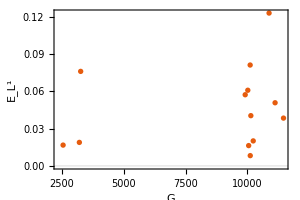
-Graphics--Graphics--Graphics-

```mathematica
Row[{ListPlot[Transpose@{Length[fΦf[#]]&/@tissues,Table[Mean@Abs[dmixture[tissue]-fαf[tissue]⟦-1⟧],{tissue,tissues}]},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"G","E_(L^1)"}],ListPlot[Transpose@{effectiveG[fαf[#]⟦-1⟧,fΦf[#],fσf[#],dΨf[#],fnf[#]⟦-1⟧,500]&/@tissues,Table[Mean@Abs[dmixture[tissue]-fαf[tissue]⟦-1⟧],{tissue,tissues}]},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"G_eff","E_(L^1)"}],ListPlot[Table[Tooltip[{testStatistic[fαf[tissue]⟦-1⟧,fΦf[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,100],Mean@Abs[dmixture[tissue]-fαf[tissue]⟦-1⟧]},tissue],{tissue,tissues}],PlotRange->{Automatic,All},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"z-median","E_(L^1)"}]},Spacer[10]]
```

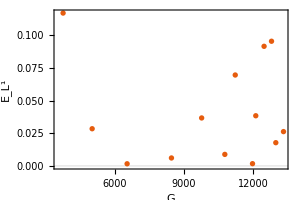
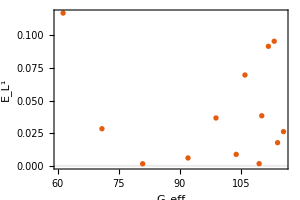
-Graphics--Graphics--Graphics-

```mathematica
Row[{ListPlot[Transpose@{Length[dΦf[#]]&/@tissues,Table[Mean@Abs[fmixture[tissue]-dαf[tissue]],{tissue,tissues}]},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"G","E_(L^1)"}],ListPlot[Transpose@{effectiveG[dαf[#],dΦf[#],dσf[#],fΨf[#],dnf[#]⟦-1⟧,500]&/@tissues,Table[Mean@Abs[fmixture[tissue]-dαf[tissue]],{tissue,tissues}]},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"G_eff","E_(L^1)"}],ListPlot[Table[Tooltip[{testStatistic[dαf[tissue],dΦf[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,100],Mean@Abs[fmixture[tissue]-dαf[tissue]]},tissue],{tissue,tissues}],PlotRange->{Automatic,All},ImageSize->{300,200},AspectRatio->Full,PlotTheme->"Scientific",FrameLabel->{"z-median","E_(L^1)"}]},Spacer[10]]
```

```mathematica
(fempConfidences[#]=singleConfidences[(*fempFisher[#]*)fGodambe[#],effectiveG[fαf[#]⟦-1⟧,estfΦ[#],fσf[#],dΨf[#],fnf[#]⟦-1⟧,1]])&/@tissues;
(dempConfidences[#]=singleConfidences[(*dempFisher[#]*)dGodambe[#],effectiveG[dαf[#],estdΦ[#],dσf[#],fΨf[#],dnf[#]⟦-1⟧,1]])&/@tissues;
```

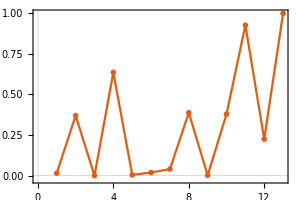
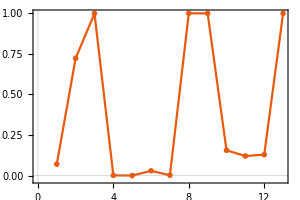

```mathematica
Row[{ListLinePlot[Table[CDF[ChiSquareDistribution[Length@dmixture[tissue]],#]&@(Part[dmixture[tissue]-fαf[tissue]⟦-1⟧,;;-2].Inverse[fempFisher[tissue]⟦;;-2,;;-2⟧/(effectiveG[fαf[tissue]⟦-1⟧,fΦf[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,1])].Part[dmixture[tissue]-fαf[tissue]⟦-1⟧,;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}],
ListLinePlot[Table[CDF[ChiSquareDistribution[Length@fmixture[tissue]],#]&@(Part[fmixture[tissue]-dαf[tissue],;;-2].Inverse[dempFisher[tissue]⟦;;-2,;;-2⟧/(effectiveG[dαf[tissue],dΦf[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,1])].Part[fmixture[tissue]-dαf[tissue],;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}]},Spacer[10]]
```

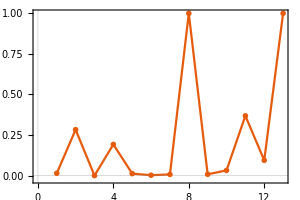
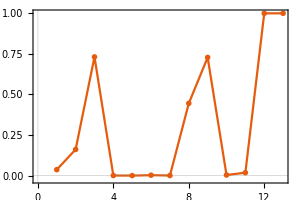

```mathematica
Quiet@Row[{ListLinePlot[Table[CDF[ChiSquareDistribution[Length@dmixture[tissue]],#]&@(Part[dmixture[tissue]-fαf[tissue]⟦-1⟧,;;-2].Inverse[fGodambe[tissue]⟦;;-2,;;-2⟧/(effectiveG[fαf[tissue]⟦-1⟧,fΦf[tissue],fσf[tissue],dΨf[tissue],fnf[tissue]⟦-1⟧,1])].Part[dmixture[tissue]-fαf[tissue]⟦-1⟧,;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}],
ListLinePlot[Table[CDF[ChiSquareDistribution[Length@fmixture[tissue]],#]&@(Part[fmixture[tissue]-dαf[tissue],;;-2].Inverse[dGodambe[tissue]⟦;;-2,;;-2⟧/(effectiveG[dαf[tissue],dΦf[tissue],dσf[tissue],fΨf[tissue],dnf[tissue]⟦-1⟧,1])].Part[fmixture[tissue]-dαf[tissue],;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}]},Spacer[10]]
```

```mathematica
Count[#,True]/Length[#]&/@{Thread[Flatten[Abs[fαf[#]⟦-1⟧-dmixture[#]]&/@tissues]≤Flatten[fempConfidences[#]&/@tissues]],Thread[Flatten[Abs[dαf[#]-fmixture[#]]&/@tissues]≤Flatten[dempConfidences[#]&/@tissues]]}//N
```

{0.918033,0.918033}

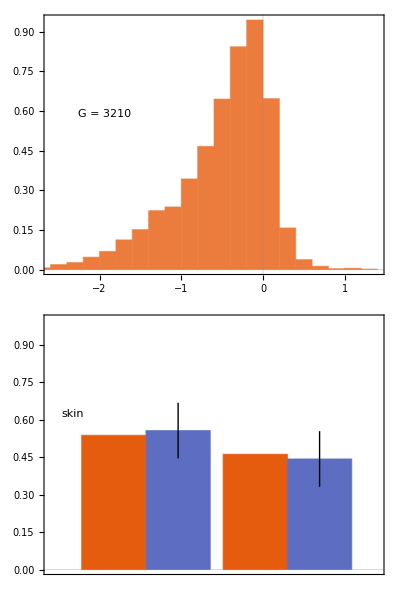
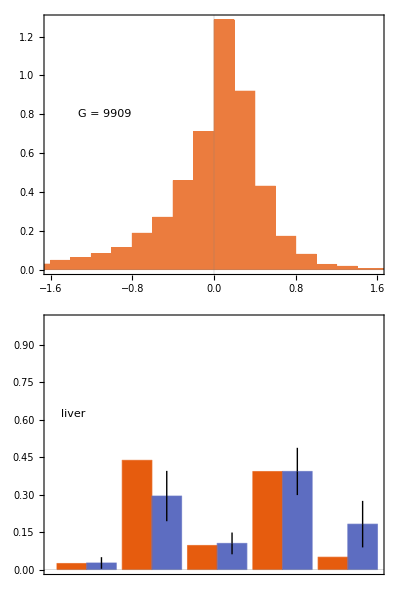
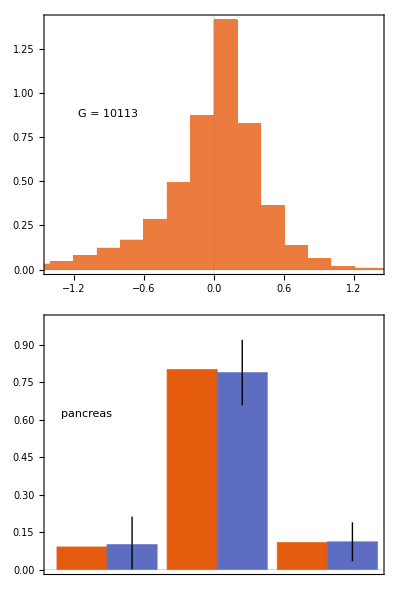
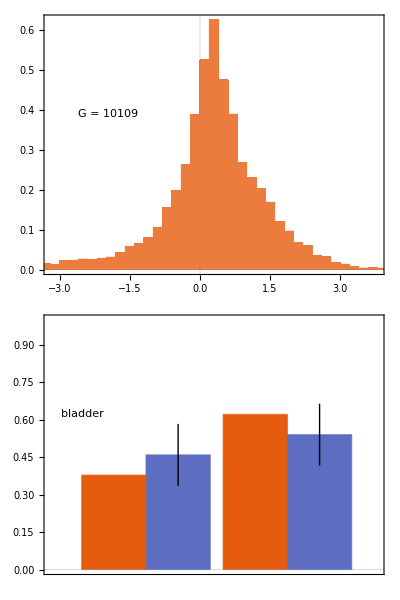
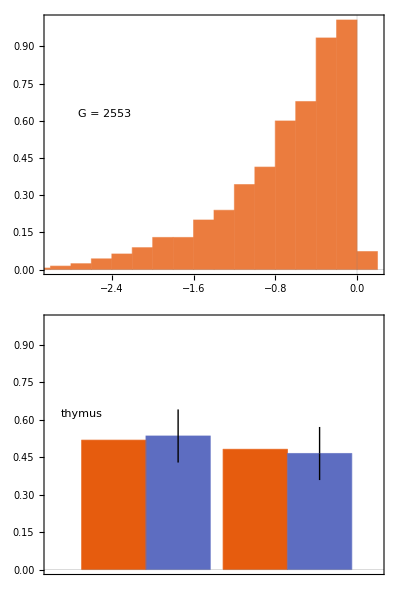
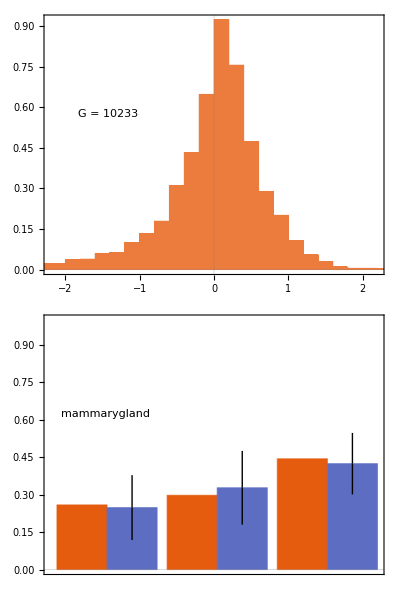
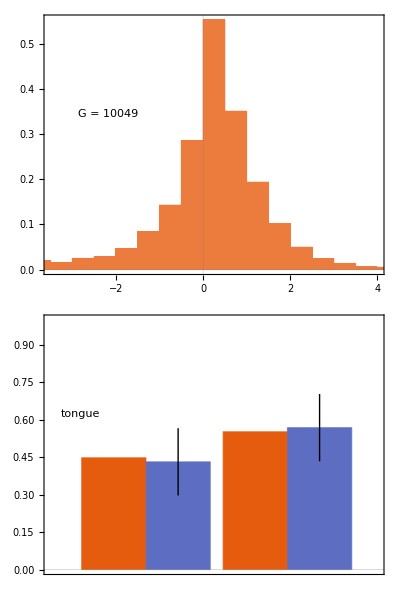
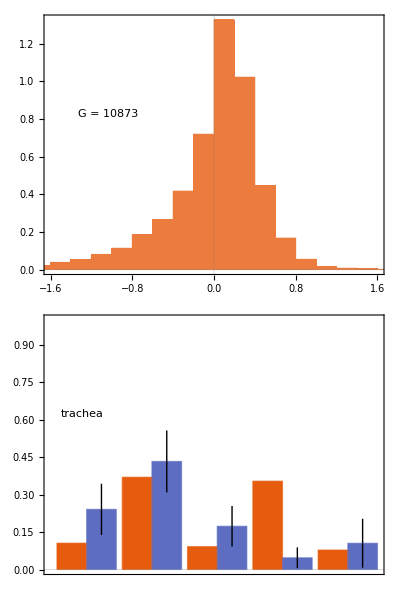
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
Grid[Partition[Table[Column[{Histogram[(estfΦ[tissue].fαf[tissue]⟦-1⟧-dΨf[tissue]/fnf[tissue]⟦-1⟧)/MapThread[Sqrt[σg2[fαf[tissue]⟦-1⟧,#1,#2]/fnf[tissue]⟦-1⟧]/.{0.->10^(-10)}&,{estfΦ[tissue],fσf[tissue]}],Automatic,"PDF",PlotTheme->"Scientific",ImageSize->(1.25{300,100}),AspectRatio->Full,Epilog->{Text[Framed[mathWrapper["G = "<>ToString[Length@dΨf[tissue]],20],RoundingRadius->5,FrameStyle->None,Background->Lighter[Gray,0.9]],Scaled[{.1,.6}],{-1,-1}]}],
BarChart[
Transpose@{dmixture[tissue],MapThread[Around[#1,{Min[#2/2,#1],Min[#2/2,1-#1]}]&,{fαf[tissue]⟦-1⟧,fempConfidences[tissue]}]},
PlotTheme->"Scientific",
PlotRange->{0,1},
ImageSize->(1.25{300,100}),
AspectRatio->Full,
FrameTicks->{None,Automatic},
BarSpacing->None,
Epilog->
{
Text[Framed[mathWrapper[ToString@tissue,24],RoundingRadius->5,Background->White],Scaled[{.05,.6}],{-1,-1}]
}
]
}],{tissue,tissues}],UpTo[3]],
Frame->All
]
```

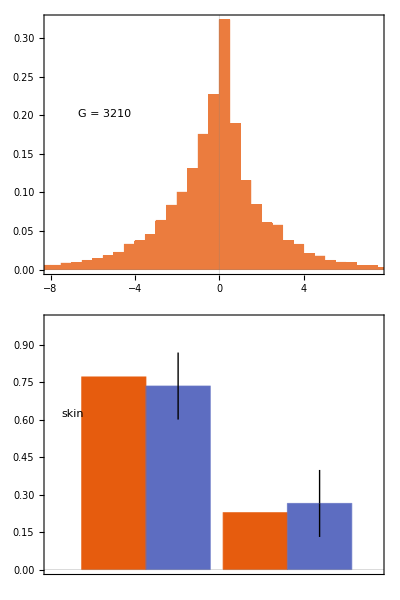
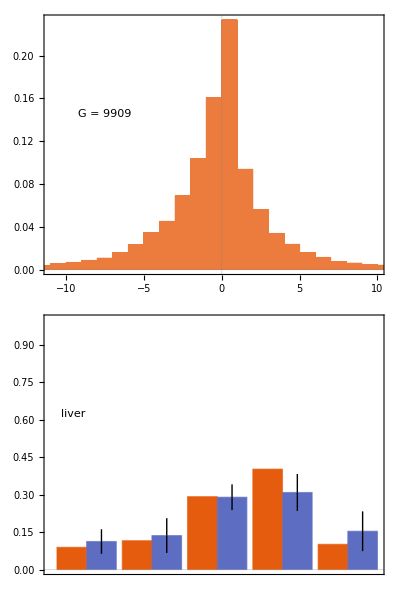
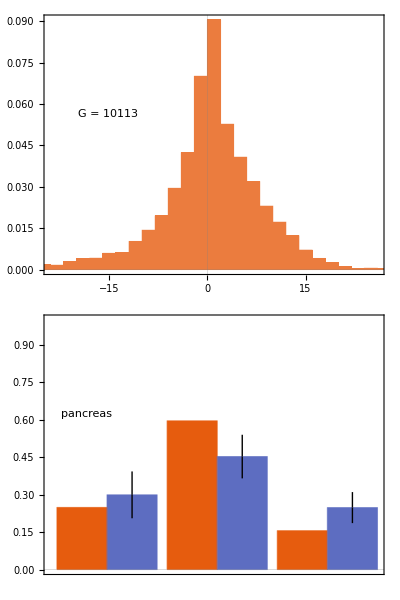
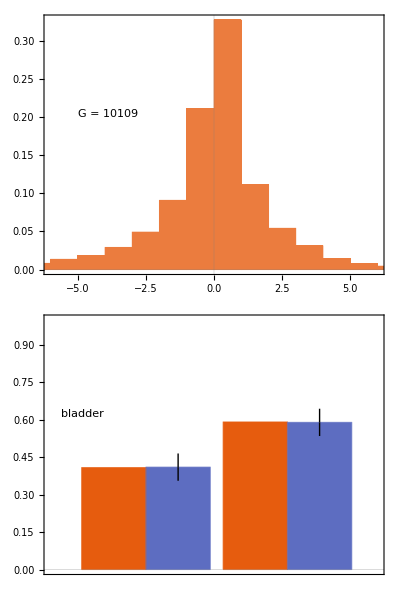
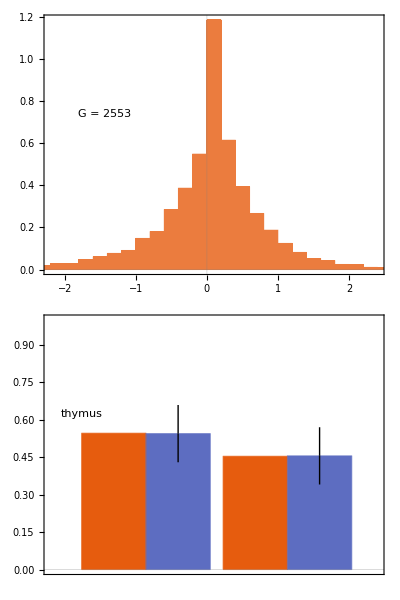
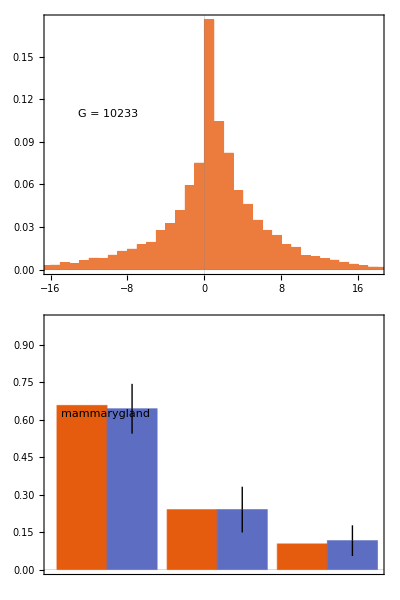
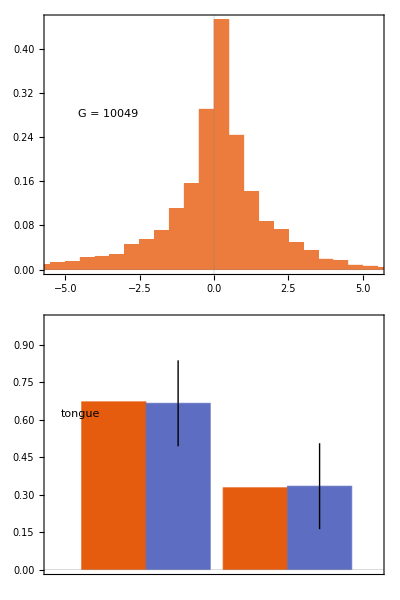
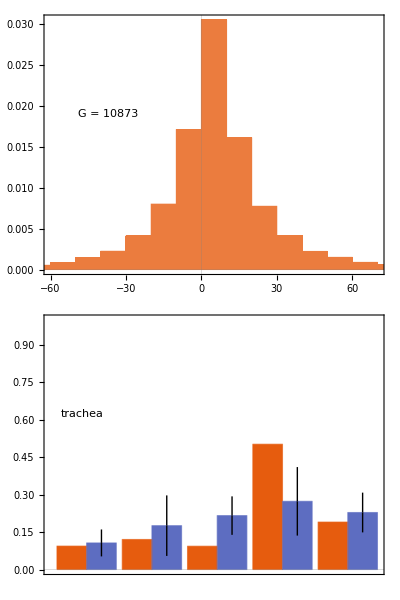
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
Grid[Partition[Table[Column[{Histogram[(estdΦ[tissue].dαf[tissue]-fΨf[tissue]/dnf[tissue]⟦-1⟧)/MapThread[Sqrt[σg2[dαf[tissue],#1,#2]/dnf[tissue]⟦-1⟧]/.{0.->10^(-10)}&,{estdΦ[tissue],dσf[tissue]}],Automatic,"PDF",PlotTheme->"Scientific",ImageSize->(1.25{300,100}),AspectRatio->Full,Epilog->{Text[Framed[mathWrapper["G = "<>ToString[Length@dΨf[tissue]],20],RoundingRadius->5,FrameStyle->None,Background->Lighter[Gray,0.9]],Scaled[{.1,.6}],{-1,-1}]}],
BarChart[
Transpose@{fmixture[tissue],MapThread[Around[#1,{Min[#2/2,#1],Min[#2/2,1-#1]}]&,{dαf[tissue],dempConfidences[tissue]}]},
PlotTheme->"Scientific",
PlotRange->{0,1},
ImageSize->(1.25{300,100}),
AspectRatio->Full,
FrameTicks->{None,Automatic},
BarSpacing->None,
Epilog->
{
Text[Framed[mathWrapper[ToString@tissue,24],RoundingRadius->5,Background->White],Scaled[{.05,.6}],{-1,-1}]
}
]
}],{tissue,tissues}],UpTo[3]],
Frame->All
]
```

### Within-Protocol

#### Load Data

```mathematica
MapIndexed[(dbulks[#1]=Import["/Users/Dani/within_protocol/dd_bulk_individuals.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2⟧)&,tissues];
(drefs[#]=Complement[Range[Length@dmlist[#]],dbulks[#]])&/@tissues;
```

```mathematica
MapIndexed[(fbulks[#1]=Import["/Users/Dani/within_protocol/ff_bulk_individuals.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2⟧)&,tissues];
(frefs[#]=Complement[Range[Length@fmlist[#]],fbulks[#]])&/@tissues;
```

```mathematica
(dmlistrefs[#]=dmlist[#]⟦drefs[#]⟧)&/@tissues;
(dmlistbulks[#]=dmlist[#]⟦dbulks[#]⟧)&/@tissues;
```

```mathematica
(fmlistrefs[#]=fmlist[#]⟦frefs[#]⟧)&/@tissues;
(fmlistbulks[#]=fmlist[#]⟦fbulks[#]⟧)&/@tissues;
```

```mathematica
(dmixturebulk[#]=1.*Normalize[Total[dmlistbulks[#]],Total])&/@tissues;
(fmixturebulk[#]=1.*Normalize[Total[fmlistbulks[#]],Total])&/@tissues;
```

```mathematica
(dΦrefs[#]=dΦs[#]⟦drefs[#]⟧)&/@tissues;
(dΦbulks[#]=dΦs[#]⟦dbulks[#]⟧)&/@tissues;
```

```mathematica
(fΦrefs[#]=fΦs[#]⟦frefs[#]⟧)&/@tissues;
(fΦbulks[#]=fΦs[#]⟦fbulks[#]⟧)&/@tissues;
```

```mathematica
(dσrefs[#]=dσs[#]⟦drefs[#]⟧)&/@tissues;
(dσbulks[#]=dσs[#]⟦dbulks[#]⟧)&/@tissues;
```

```mathematica
(fσrefs[#]=fσs[#]⟦frefs[#]⟧)&/@tissues;
(fσbulks[#]=fσs[#]⟦fbulks[#]⟧)&/@tissues;
```

```mathematica
(dΦref[#]=Total[MapThread[mMatrix[#2,Length@#1]*#1&,{dΦrefs[#],dmlistrefs[#]}]]/mMatrix[Total[dmlistrefs[#]],Length[First@dΦrefs[#]]])&/@tissues;
(dσref[#]=Transpose@MapThread[mixtureσ[#1,#3,#2]&,{Normalize[#,Total]&/@Transpose[dmlistrefs[#]],Transpose[dΦrefs[#],{3,2,1}],Transpose[dσrefs[#],{3,2,1}]}])&/@tissues;
```

```mathematica
(fΦref[#]=Total[MapThread[mMatrix[#2,Length@#1]*#1&,{fΦrefs[#],fmlistrefs[#]}]]/mMatrix[Total[fmlistrefs[#]],Length[First@fΦrefs[#]]])&/@tissues;
(fσref[#]=Transpose@MapThread[mixtureσ[#1,#3,#2]&,{Normalize[#,Total]&/@Transpose[fmlistrefs[#]],Transpose[fΦrefs[#],{3,2,1}],Transpose[fσrefs[#],{3,2,1}]}])&/@tissues;
```

```mathematica
(dΦbulk[#]=Total[Total[MapThread[mMatrix[#2,Length@#1]*#1&,{dΦbulks[#],dmlistbulks[#]}]],{2}])&/@tissues;
(fΦbulk[#]=Total[Total[MapThread[mMatrix[#2,Length@#1]*#1&,{fΦbulks[#],fmlistbulks[#]}]],{2}])&/@tissues;
```

#### Filter Data

```mathematica
Table[{dΦreff[tissue],dσreff[tissue],dΦbulkf[tissue]}=Extract[#,simpleFilter[dΦref[tissue],dΦbulk[tissue]]]&/@{dΦref[tissue],dσref[tissue],dΦbulk[tissue]},{tissue,tissues}];
```

```mathematica
Table[{fΦreff[tissue],fσreff[tissue],fΦbulkf[tissue]}=Extract[#,simpleFilter[fΦref[tissue],fΦbulk[tissue]]]&/@{fΦref[tissue],fσref[tissue],fΦbulk[tissue]},{tissue,tissues}];
```

#### Deconvolve Data

```mathematica
{Total[dmlistbulks[liver],2],dmixturebulk[liver]}
```

{1201,{0.0591174,0.238968,0.0566195,0.576187,0.0691091}}

```mathematica
Monitor[Table[Block[{Print},Quiet[{ddα[tissue],ddΦ[tissue],ddL[tissue],ddn[tissue],ddLS[tissue]}=findMixtures[dΦreff[tissue],dΦbulkf[tissue],dσreff[tissue]/.{0|0.->10^(-6)},10^(-10),50,5,Total[dmlistrefs[tissue]]]]],{tissue,tissues⟦-5;;⟧}],tissue];
```

#### Confidence Regions

```mathematica
MapIndexed[(ffα[#1]=Import["/Users/Dani/within_protocol/ff_alphas.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2⟧)&,tissues];
MapIndexed[(ffn[#1]=Import["/Users/Dani/within_protocol/ff_n.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2,1⟧)&,tissues];
```

```mathematica
MapIndexed[(ddα[#1]=Import["/Users/Dani/within_protocol/dd_alphas.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2⟧)&,tissues];
MapIndexed[(ddn[#1]=Import["/Users/Dani/within_protocol/dd_n.csv","CSV"]⟦;;,2;;-1⟧⟦First@#2,1⟧)&,tissues];
```

```mathematica
Monitor[Table[ffGodambe[tissue]=godambeInformation[ffα[tissue],fΦreff[tissue],fσreff[tissue],fΦbulkf[tissue],ffn[tissue]],{tissue,tissues}],tissue];
```

```mathematica
Monitor[Table[ddGodambe[tissue]=godambeInformation[ddα[tissue],dΦreff[tissue],dσreff[tissue],dΦbulkf[tissue],ddn[tissue]],{tissue,tissues}],tissue];
```

```mathematica
With[{tissue=lung},ddGodambe[tissue]=godambeInformationInvertible[ddα[tissue],dΦreff[tissue],dσreff[tissue],dΦbulkf[tissue],ddn[tissue],1]];
```

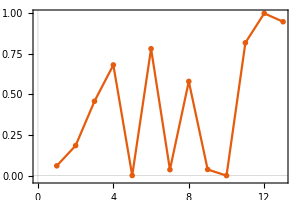
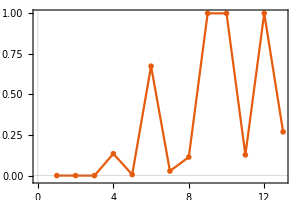

```mathematica
Row[{ListLinePlot[Table[CDF[ChiSquareDistribution[Length@dmixturebulk[tissue]],#]&@(Part[dmixturebulk[tissue]-ddα[tissue],;;-2].Inverse[ddGodambe[tissue]⟦;;-2,;;-2⟧/(Length[fΦreff[tissue]]^(0.75))].Part[dmixturebulk[tissue]-ddα[tissue],;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}],
ListLinePlot[Table[CDF[ChiSquareDistribution[Length@fmixturebulk[tissue]],#]&@(Part[fmixturebulk[tissue]-ffα[tissue],;;-2].Inverse[ffGodambe[tissue]⟦;;-2,;;-2⟧/(Length[fΦreff[tissue]])].Part[fmixturebulk[tissue]-ffα[tissue],;;-2]),{tissue,tissues}],ImageSize->{300,200},AspectRatio->Full,PlotTheme->{"Scientific","BoldScheme"},PlotRange->{-0.025,1}]},Spacer[10]]
```

```mathematica
Table[ffConfidence[tissue]=Append[2Sqrt@Diagonal[#]⟦;;-2⟧,2Sqrt@Total[#⟦;;-2,;;-2⟧,2]]&@(ffGodambe[tissue]/Length[fΦreff[tissue]]),{tissue,tissues}];
Table[ddConfidence[tissue]=Append[2Sqrt@Diagonal[#]⟦;;-2⟧,2Sqrt@Total[#⟦;;-2,;;-2⟧,2]]&@(ddGodambe[tissue]/(Length[dΦreff[tissue]]^(0.75))),{tissue,tissues}];
```

```mathematica
Grid[Partition[Table[Column[{Histogram[(fΦreff[tissue].ffα[tissue]-fΦbulkf[tissue]/ffn[tissue])/MapThread[Sqrt[σg2[ffα[tissue],#1,#2]/ffn[tissue]]/.{0.->10^(-10)}&,{fΦreff[tissue],fσreff[tissue]}],Automatic,"PDF",PlotTheme->"Scientific",ImageSize->(1.25{300,100}),AspectRatio->Full,Epilog->{Text[Framed[mathWrapper["G = "<>ToString[Length@fΦbulkf[tissue]],20],RoundingRadius->5,FrameStyle->None,Background->Lighter[Gray,0.9]],Scaled[{.1,.6}],{-1,-1}]}],
BarChart[
Transpose@{fmixturebulk[tissue],MapThread[Around[#1,{Min[#2/2,#1],Min[#2/2,1-#1]}]&,{ffα[tissue],ffConfidence[tissue]}]},
PlotTheme->"Scientific",
PlotRange->{0,1},
ImageSize->(1.25{300,100}),
AspectRatio->Full,
FrameTicks->{None,Automatic},
BarSpacing->None,
Epilog->
{
Text[Framed[mathWrapper[ToString@tissue,24],RoundingRadius->5,Background->White],Scaled[{.05,.6}],{-1,-1}]
}
]
}],{tissue,tissues}],UpTo[3]],
Frame->All
]
```

```mathematica
Grid[Partition[Table[Column[{Histogram[(dΦreff[tissue].ddα[tissue]-dΦbulkf[tissue]/ddn[tissue])/MapThread[Sqrt[σg2[ddα[tissue],#1,#2]/ddn[tissue]]/.{0.->10^(-10)}&,{dΦreff[tissue],dσreff[tissue]}],Automatic,"PDF",PlotTheme->"Scientific",ImageSize->(1.25{300,100}),AspectRatio->Full,Epilog->{Text[Framed[mathWrapper["G = "<>ToString[Length@dΦbulkf[tissue]],20],RoundingRadius->5,FrameStyle->None,Background->Lighter[Gray,0.9]],Scaled[{.1,.6}],{-1,-1}]}],
BarChart[
Transpose@{dmixturebulk[tissue],MapThread[Around[#1,{Min[#2/2,#1],Min[#2/2,1-#1]}]&,{ddα[tissue],ddConfidence[tissue]}]},
PlotTheme->"Scientific",
PlotRange->{0,1},
ImageSize->(1.25{300,100}),
AspectRatio->Full,
FrameTicks->{None,Automatic},
BarSpacing->None,
Epilog->
{
Text[Framed[mathWrapper[ToString@tissue,24],RoundingRadius->5,Background->White],Scaled[{.05,.6}],{-1,-1}]
}
]
}],{tissue,tissues}],UpTo[3]],
Frame->All
]
```

### Ground Truth

#### Load Data

```mathematica
gtϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/cell_line_mix/cell_line_mix_signature.csv","CSV"]⟦2;;,2;;⟧;
gtσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/cell_line_mix/cell_line_mix_variances.csv","CSV"]⟦2;;,2;;⟧;
gtΨ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/cell_line_mix/cell_line_mix_bulk.csv","CSV"]⟦2;;,2⟧;
gtm=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/cell_line_mix/cell_line_mix_signature_n.csv","CSV"]⟦;;,2⟧;
```

```mathematica
geneNames=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/cell_line_mix/cell_line_mix_signature.csv","CSV"]⟦2;;,1⟧;
gtTruth={0.6,0.3,0.1};
```

```mathematica
rPositions=Flatten@Position[StringContainsQ[#,"RPL"]&/@geneNames,True];
nrPositions=Complement[Range[Length@gtϕ],rPositions];
```

#### Filter Data

Within-Protocol

```mathematica
{gtϕf1,gtσf1,gtΨf1}=offSimplexFilterAbsolute[gtϕ,gtσ,gtΨ,0]⟦2⟧;
```

```mathematica
Length/@{gtϕ,gtϕf1}
```

{18139,9119}

```mathematica
filterPos=MemberQ[gtϕf1,#]&/@gtϕ;
```

```mathematica
testPos=Flatten@Position[filterPos,False];
```

Cross-Protocol

F/D

```mathematica
Length[Part[{fdgtiterations,fdgtfilter}=filterFD[gtϕ⟦nrPositions⟧,gtσ⟦nrPositions⟧,gtΨ⟦nrPositions⟧],2]]
```

12029

```mathematica
{gtϕf2,gtσf2,gtΨf2}=Extract[#,fdgtfilter]&/@{gtϕ⟦nrPositions⟧,gtσ⟦nrPositions⟧,gtΨ⟦nrPositions⟧};
```

```mathematica
filterPos=MemberQ[gtϕf2,#]&/@gtϕ;
```

```mathematica
testPos=Flatten@Position[filterPos,False];
```

D/F

```mathematica
Length[Part[{dfgtiterations,dfgtfilter}=filterDF[gtϕ,gtσ,gtΨ],2]]
```

5910

```mathematica
{gtϕf3,gtσf3,gtΨf3}=Extract[#,dfgtfilter]&/@{gtϕ,gtσ,gtΨ};
```

```mathematica
filterPos=MemberQ[gtϕf3,#]&/@gtϕ;
```

```mathematica
testPos=Flatten@Position[filterPos,False];
```

#### Deconvolve Data

Unfiltered

```mathematica
AbsoluteTiming[{gtα,gtΦ,gtL,gtn,gtLS}=findMixtures[gtϕ,gtΨ,gtσ/.{0|0.->10^(-6)},10^(-10),50,5,gtm];]
```

α_0 = {0.721433,0.278567,0.}, ℒ_0 = 5.49364×10^9, n_0 = 1955.91

α = {0.591339,0.408661,0.}, ℒ = 3.52869×10^9, n = 2727.81

α = {0.,0.55305,0.44695}, ℒ = 2.94674×10^9, n = 131279.

α = {0.,0.541483,0.458517}, ℒ = 1.61186×10^7, n = 131161.

α = {0.,0.508215,0.491785}, ℒ = 1.1396×10^7, n = 138704.

α = {0.,0.495829,0.504171}, ℒ = 1.15173×10^7, n = 140589.

α = {0.,0.470726,0.529274}, ℒ = 8.22584×10^6, n = 142034.

α = {0.,0.4365,0.5635}, ℒ = 8.02136×10^6, n = 145671.

α = {0.,0.405069,0.594931}, ℒ = 7.83312×10^6, n = 149539.

α = {0.,0.376027,0.623973}, ℒ = 7.65899×10^6, n = 153578.

α = {0.,0.34907,0.65093}, ℒ = 7.49689×10^6, n = 157744.

α_Final = {0.,0.376027,0.623973}, ℒ_Final = 7.5617×10^6, n_Final = 153578.

α_LS = {0.616547,0.255214,0.12824}, ℒ_LS = 2.89089×10^8

{2903.07,Null}

Within-Protocol Filter

```mathematica
{gtαf1,gtΦf1,gtLf1,gtnf1,gtLSf1}=findMixtures[gtϕ⟦testPos⟧,gtΨ⟦testPos⟧,gtσ⟦testPos⟧/.{0|0.->10^(-6)},10^(-10),50,5,gtm];
```

α_0 = {0.70086,0.29914,0.}, ℒ_0 = 2.44529×10^9, n_0 = 1885.68

α = {0.495648,0.504352,0.}, ℒ = 1.5828×10^9, n = 2682.11

α = {0.,1.,0.}, ℒ = 1.1993×10^10, n = 34574.4

α = {0.495648,0.504352,0.}, ℒ = 6.99603×10^9, n = 56361.7

α_Final = {0.495648,0.504352,0.}, ℒ_Final = 8.4074×10^7, n_Final = 2682.11

α_LS = {0.622249,0.327339,0.0504117}, ℒ_LS = 9.61174×10^7

Cross-Protocol Filter

F/D

```mathematica
{gtαf2,gtΦf2,gtLf2,gtnf2,gtLSf2}=findMixtures[gtϕ⟦testPos⟧,gtΨ⟦testPos⟧,gtσ⟦testPos⟧/.{0|0.->10^(-6)},10^(-10),50,5,gtm];
```

α_0 = {0.721022,0.278978,0.}, ℒ_0 = 3.51773×10^9, n_0 = 1949.14

α = {0.662468,0.337532,0.}, ℒ = 2.2614×10^9, n = 2732.47

α = {0.,0.658269,0.341731}, ℒ = 2.23763×10^9, n = 169726.

α = {2.29617×10^-11,0.65317,0.34683}, ℒ = 1.11236×10^7, n = 170052.

α = {1.64168×10^-11,0.649625,0.350375}, ℒ = 1.10544×10^7, n = 170393.

α = {1.56713×10^-11,0.644704,0.355296}, ℒ = 1.10015×10^7, n = 170940.

α = {0.,0.592188,0.407812}, ℒ = 7.10313×10^6, n = 172742.

α = {0.,0.541764,0.458236}, ℒ = 6.88784×10^6, n = 175432.

α = {0.,0.498251,0.501749}, ℒ = 6.70103×10^6, n = 178682.

α = {0.,0.459729,0.540271}, ℒ = 6.53587×10^6, n = 182477.

α = {0.,0.425005,0.574995}, ℒ = 6.38609×10^6, n = 186709.

α_Final = {0.,0.459729,0.540271}, ℒ_Final = 6.4469×10^6, n_Final = 182477.

α_LS = {1.,0.,0.}, ℒ_LS = 1.28734×10^9

D/F

```mathematica
{gtαf3,gtΦf3,gtLf3,gtnf3,gtLSf3}=findMixtures[gtϕf3,gtΨf3,gtσf3/.{0|0.->10^(-10)},10^(-10),50,dfgtiterations,gtm];
```

α_0 = {0.325686,0.364593,0.309721}, ℒ_0 = 728505., n_0 = 8831.89

α = {0.316684,0.368449,0.314867}, ℒ = 186679., n = 8998.07

α = {0.297452,0.375931,0.326617}, ℒ = 163232., n = 9317.26

α_Final = {0.325686,0.364593,0.309721}, ℒ_Final = 169317., n_Final = 8831.89

α_LS = {0.353357,0.351632,0.295011}, ℒ_LS = 173464.

#### Interpretation

```mathematica
gtLS⟦1⟧
```

{0.616547,0.255214,0.12824}

```mathematica
gtGodambe=godambeInformation[gtLS⟦1⟧,gtΦ,gtσ,gtΨ,gtn⟦-1⟧];
```

```mathematica
gtConfidences=singleConfidences[gtGodambe,Length@gtϕ];
```

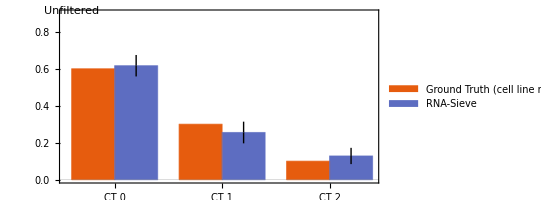

```mathematica
gtPlot=BarChart[Transpose@{gtTruth,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{gtLS⟦1⟧,gtConfidences}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{("CT "<>ToString[#])&/@Range[0,2],{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth (cell line mix)","RNA-Sieve"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.7,0.75}]],Epilog->{Text[Framed[mathWrapper["Unfiltered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]
```

```mathematica
Export["cell_line_mix_inferences.csv",Prepend[{gtLS⟦1⟧},{"CT0","CT1","CT2"}]]
```

cell_line_mix_inferences.csv

```mathematica
Export["cell_line_mix_confidences.csv",Prepend[{gtConfidences},{"CT0","CT1","CT2"}]]
```

cell_line_mix_confidences.csv

```mathematica
Minimize[{Total[Abs[gtϕ.gtTruth-gtΨ/n]/Sqrt[MapThread[σg2[gtTruth,#1,#2]&,{gtϕ,gtσ}]]],n>0},n]
```

{5082.48,{n→31598.4}}

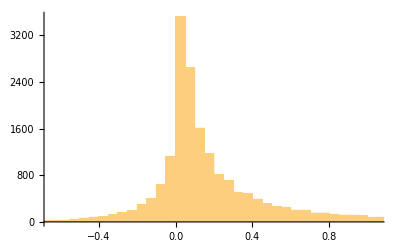

```mathematica
With[{n=31598.4},Histogram[(gtϕ.gtTruth-gtΨ/n)/Sqrt[MapThread[σg2[gtTruth,#1,#2]&,{gtϕ,gtσ}]],{0.05}]]
```

```mathematica
test=With[{n=31598.4},Flatten@Position[(gtϕ.gtTruth-gtΨ/n)/Sqrt[MapThread[σg2[gtTruth,#1,#2]&,{gtϕ,gtσ}]],x_/;Abs[x]<0.1]];
```

```mathematica
findMixtures[gtϕ⟦test⟧,gtΨ⟦test⟧,gtσ⟦test⟧/.{0|0.->10^(-10)},10^(-10),50,5,gtm];
```

α_0 = {0.590399,0.31004,0.0995611}, ℒ_0 = 732169., n_0 = 30723.1

α = {0.589786,0.310729,0.099485}, ℒ = 112418., n = 30711.3

α = {0.589033,0.311394,0.0995725}, ℒ = 112414., n = 30700.5

α = {0.588294,0.312047,0.099659}, ℒ = 112394., n = 30689.8

α = {0.58757,0.312686,0.0997446}, ℒ = 112375., n = 30679.5

α = {0.586859,0.313312,0.0998292}, ℒ = 112356., n = 30669.4

α = {0.585725,0.314519,0.0997555}, ℒ = 109743., n = 30670.

α = {0.583995,0.316238,0.0997667}, ℒ = 109697., n = 30661.2

α_Final = {0.585725,0.314519,0.0997555}, ℒ_Final = 109719., n_Final = 30670.

α_LS = {0.599101,0.314804,0.0860957}, ℒ_LS = 115121.

```mathematica
Table[(MedianDeviation[#]/Median[#])&/@{Max/@dΦ[tissue],Max/@gtΦ},{tissue,tissues}]
```

{{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961},{0.997793,0.971961},{1.,0.971961},{1.,0.971961},{1.,0.971961}}

```mathematica
Table[(Median[#])&/@{Max/@dΦ[tissue],Max/@gtΦ},{tissue,tissues}]
```

{{0.0376825,0.0779242},{0.086019,0.0779242},{0.0494679,0.0779242},{0.0637025,0.0779242},{0.0100604,0.0779242},{0.0355131,0.0779242},{0.0348197,0.0779242},{0.0425727,0.0779242},{0.0544553,0.0779242},{0.0437499,0.0779242},{0.0882269,0.0779242},{0.060161,0.0779242},{0.0474841,0.0779242}}

```mathematica
Table[(StandardDeviation[#]/Mean[#]&/@{Max/@dΦ[tissue],Max/@gtϕ}),{tissue,tissues}]
```

{{7.53659,7.8685},{6.66162,7.8685},{30.0096,7.8685},{7.27426,7.8685},{7.0609,7.8685},{6.91766,7.8685},{7.75124,7.8685},{8.72186,7.8685},{7.46276,7.8685},{6.93195,7.8685},{6.83333,7.8685},{10.4221,7.8685},{20.5751,7.8685}}

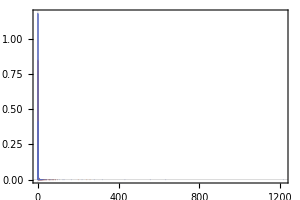
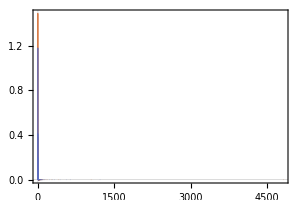
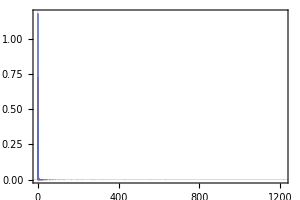
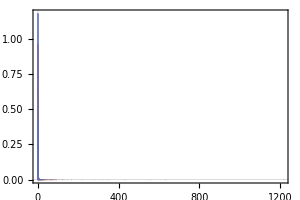
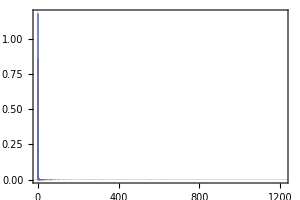
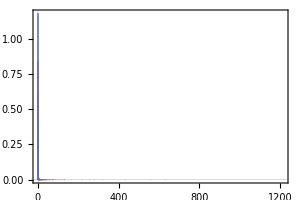
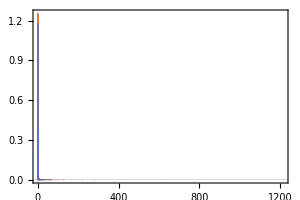
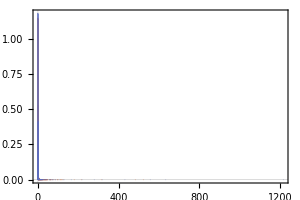
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  |  |

```mathematica
Grid@Partition[Histogram[{Normalize[fΨsimple[#]/(Max/@dΦsimple[#]),Mean],Normalize[gtΨ/(Max/@gtϕ),Mean]},{0.5},"PDF",PlotTheme->"Scientific",PlotRange->{{0,6},{0,Automatic}},ImageSize->{300,200},AspectRatio->Full]&/@tissues,UpTo@4]
```

### Newman

#### Load Data

```mathematica
newmanm=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_n_sig.csv"]⟦2;;,2⟧;
newmanΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_bulk.csv"]⟦2;;,2;;⟧;newmanσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_var.csv"]⟦2;;,2;;⟧;
newmanTruth=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦2;;,2;;⟧;
newmanϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_sig.csv"]⟦2;;,2;;⟧;
```

```mathematica
newmanTruth=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦2;;,2;;⟧;
```

```mathematica
newneutrophilsm=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_with_neutrophils/newman_n_sig_neut.csv"]⟦;;,2⟧;
newneutrophilsΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_with_neutrophils/newman_bulk_neut.csv"]⟦2;;,2;;⟧;newneutrophilsσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_with_neutrophils/newman_var_neut.csv"]⟦2;;,2;;⟧;
newneutrophilsϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_with_neutrophils/newman_sig_neut.csv"]⟦2;;,2;;⟧;
```

```mathematica
newmanΦnames=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_sig.csv"]⟦1,2;;⟧;
newmanTruthnames=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦1,2;;⟧;
nameOrder={"Monocyte","CD8T","CD4T","NKT","NK","B","Neutrophils"};
```

```mathematica
newmanm=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_n.csv"]⟦2;;,2;;⟧;
newmanΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_bulk.csv"]⟦2;;,2;;⟧;
newmanϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_mean.csv"]⟦2;;,2;;⟧;
newmanσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_var.csv"]⟦2;;,2;;⟧;
```

```mathematica
newmanTruthBulkOrder=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦2;;,1⟧;
newmanFinalBulkOrder=(If[StringTake[#,1]=="X",StringTake[#,{2,-1}],#]&@StringSplit[#,"_"]⟦1⟧)&/@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_bulk.csv"]⟦1,2;;⟧;
newmanTruthTypeOrder=Rest@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦1⟧/.{"Other"->"Neutrophil"};
newmanFinalTypeOrder=Rest@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman_neutrophil/newman_mean.csv"]⟦1⟧;
```

```mathematica
newmanFinalTruth=Transpose[Transpose[Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/newman1/newman_true_props.csv"]⟦Prepend[1+Ordering[newmanTruthBulkOrder],1]⟧⟦Prepend[1+InversePermutation@Ordering[newmanFinalBulkOrder],1]⟧]⟦Prepend[1+Ordering[newmanTruthTypeOrder],1]⟧⟦Prepend[1+InversePermutation@Ordering[newmanFinalTypeOrder],1]⟧]⟦2;;,2;;⟧;
```

#### Filter Data

```mathematica
{newmaniterations,newmanfilters}=Transpose[filterDF[newmanϕ,newmanσ,newmanΨs⟦;;,#⟧]&/@Range[Length@newmanΨs⟦1⟧]];
{newmanϕf,newmanσf,newmanΨsf}=Extract[#,Intersection@@newmanfilters]&/@{newmanϕ,newmanσ,newmanΨs};
```

```mathematica
{newneutrophilsiterations,newneutrophilsfilters}=Transpose[filterDF[newneutrophilsϕ,newneutrophilsσ,newneutrophilsΨs⟦;;,#⟧]&/@Range[Length@newneutrophilsΨs⟦1⟧]];
{newneutrophilsϕf,newneutrophilsσf,newneutrophilsΨsf}=Extract[#,Intersection@@newneutrophilsfilters]&/@{newneutrophilsϕ,newneutrophilsσ,newneutrophilsΨs};
```

#### Deconvolve Data

```mathematica
Quiet[{newmanα,newmanΦ,newmanℒ,newmann,newmanLS}=findMixturesJoint[newmanϕ,newmanΨs,newmanσ/.{0|0.->10^(-6)},10^(-10),50,3,newmanm]];
```

```mathematica
Dimensions@newmanαf⟦-1⟧
```

{5,12}

```mathematica
AbsoluteTiming[Quiet[{newmanαf,newmanΦf,newmanℒf,newmannf,newmanLSf}=findMixturesJoint[newmanϕf,newmanΨsf,newmanσf/.{0|0.->10^(-6)},10^(-10),50,3,newmanm]];]
```

α_0 = {{0.271076,0.,0.0010927,0.0738818,0.0372486,0.616701},{0.134092,0.,0.145657,0.102093,0.0377192,0.580439},{0.237515,0.00482409,0.,0.100115,0.057645,0.599901},{0.165486,0.,0.187463,0.0804846,0.018112,0.548455},{0.25614,0.0892857,0.,0.112047,0.0445661,0.497961},{0.131353,0.0810641,0.14044,0.110687,0.0665491,0.469907},{0.098378,0.0421827,0.182137,0.0939714,0.0986498,0.484681},{0.151766,0.,0.0962535,0.0791126,0.0428283,0.63004},{0.175764,0.0678014,0.0640065,0.0921805,0.0883776,0.51187},{0.114471,0.072224,0.125993,0.105843,0.124289,0.457179},{0.132369,0.0264108,0.118762,0.0924718,0.0722163,0.557771},{0.231757,0.0190703,0.0175758,0.0969272,0.0480184,0.586651}}, ℒ_0 = 974525., n_0 = {73.5744,58.3319,50.8308,73.9776,46.4788,55.2682,62.912,70.709,57.872,63.6847,67.8331,60.2492}

α = {{0.20557,0.00282618,0.105092,0.0634121,0.0379478,0.585152},{0.188918,0.040185,0.102215,0.0536598,0.0647956,0.550227},{0.203754,0.0724361,0.0173876,0.0546633,0.0496127,0.602146},{0.205706,0.0265683,0.144824,0.048515,0.0440125,0.530375},{0.255342,0.0610475,0.0151583,0.0913118,0.0539501,0.523191},{0.200666,0.0514737,0.112536,0.105663,0.0845485,0.445113},{0.177472,0.0439807,0.132345,0.0934894,0.108235,0.444478},{0.168226,0.00827289,0.102518,0.0665619,0.0589475,0.595474},{0.202467,0.0747317,0.0570147,0.0882339,0.0908697,0.486683},{0.205029,0.0451,0.0907306,0.103926,0.122841,0.432374},{0.202111,0.00615355,0.109738,0.0878019,0.086374,0.507822},{0.230779,0.017827,0.0609969,0.0878982,0.0569762,0.545523}}, ℒ = 948982., n = {63.4105,53.9496,40.5367,68.2557,39.5888,54.5782,63.5701,62.0128,55.519,66.0199,66.7455,54.8129}

α = {{0.249945,0.0289953,0.0350174,0.0501076,0.0637335,0.572201},{0.225001,0.,0.138675,0.0543907,0.0876276,0.494306},{0.261355,0.0111999,0.0178967,0.0816974,0.0882685,0.539582},{0.230886,0.,0.164821,0.0419677,0.0690723,0.493252},{0.294231,0.053058,0.0286785,0.0829514,0.0831483,0.457932},{0.231052,0.053214,0.123074,0.0731061,0.103037,0.416517},{0.211941,0.032702,0.14694,0.0638928,0.124087,0.420438},{0.20823,0.0260792,0.0950382,0.0500522,0.0820461,0.538554},{0.235728,0.0615364,0.0670634,0.0696532,0.11082,0.455199},{0.22964,0.0437385,0.11254,0.0640278,0.137775,0.412279},{0.220196,0.0542079,0.100425,0.0395074,0.10607,0.479593},{0.260377,0.0329318,0.0467334,0.0687949,0.0795133,0.511649}}, ℒ = 568970., n = {58.1702,103.75,36.9436,119.539,36.658,52.7092,61.8478,57.8889,52.9887,64.6183,64.378,51.4125}

α = {{0.342868,0.0156745,0.00619864,0.0579007,0.087072,0.490287},{0.128953,0.0201564,0.221954,0.,0.0566819,0.572254},{0.351424,0.0484168,0.,0.0573772,0.103183,0.439599},{0.152392,0.00637065,0.248472,0.,0.0458569,0.546909},{0.390378,0.0618509,0.,0.0771105,0.106312,0.364349},{0.29779,0.0923781,0.053604,0.0659731,0.129777,0.360477},{0.274681,0.0709097,0.0848614,0.0536745,0.148454,0.367419},{0.284358,0.0323659,0.0396757,0.0559178,0.107391,0.480291},{0.307661,0.0980037,0.00306253,0.0597936,0.135282,0.396197},{0.292771,0.0802991,0.0485025,0.0564127,0.162419,0.359595},{0.289094,0.0406946,0.0619315,0.0527809,0.132039,0.42346},{0.345129,0.0414173,0.,0.072256,0.103554,0.437643}}, ℒ = 848913., n = {59.6771,76.2755,118.551,85.1458,106.288,53.9169,63.3683,59.5636,54.6904,66.1476,66.1174,235.609}

α = {{0.249945,0.0289953,0.0350174,0.0501076,0.0637335,0.572201},{0.225001,0.,0.138675,0.0543907,0.0876276,0.494306},{0.261355,0.0111999,0.0178967,0.0816974,0.0882685,0.539582},{0.230886,0.,0.164821,0.0419677,0.0690723,0.493252},{0.294231,0.053058,0.0286785,0.0829514,0.0831483,0.457932},{0.231052,0.053214,0.123074,0.0731061,0.103037,0.416517},{0.211941,0.032702,0.14694,0.0638928,0.124087,0.420438},{0.20823,0.0260792,0.0950382,0.0500522,0.0820461,0.538554},{0.235728,0.0615364,0.0670634,0.0696532,0.11082,0.455199},{0.22964,0.0437385,0.11254,0.0640278,0.137775,0.412279},{0.220196,0.0542079,0.100425,0.0395074,0.10607,0.479593},{0.260377,0.0329318,0.0467334,0.0687949,0.0795133,0.511649}}, ℒ = 621156., n = {92.8488,82.5313,126.642,90.6314,113.502,60.1936,70.7397,75.5678,60.967,74.4221,101.494,66.4623}

α_Final = {{0.249945,0.0289953,0.0350174,0.0501076,0.0637335,0.572201},{0.225001,0.,0.138675,0.0543907,0.0876276,0.494306},{0.261355,0.0111999,0.0178967,0.0816974,0.0882685,0.539582},{0.230886,0.,0.164821,0.0419677,0.0690723,0.493252},{0.294231,0.053058,0.0286785,0.0829514,0.0831483,0.457932},{0.231052,0.053214,0.123074,0.0731061,0.103037,0.416517},{0.211941,0.032702,0.14694,0.0638928,0.124087,0.420438},{0.20823,0.0260792,0.0950382,0.0500522,0.0820461,0.538554},{0.235728,0.0615364,0.0670634,0.0696532,0.11082,0.455199},{0.22964,0.0437385,0.11254,0.0640278,0.137775,0.412279},{0.220196,0.0542079,0.100425,0.0395074,0.10607,0.479593},{0.260377,0.0329318,0.0467334,0.0687949,0.0795133,0.511649}}, ℒ_Final = 459501., n_Final = {58.1702,103.75,36.9436,119.539,36.658,52.7092,61.8478,57.8889,52.9887,64.6183,64.378,51.4125}

α_LS = {{0.256103,0.0534824,0.0806953,0.050737,0.0655035,0.493478},{0.150451,0.164222,0.114491,0.0425731,0.0823372,0.445924},{0.232036,0.0854066,0.0648784,0.0561271,0.0806067,0.480946},{0.17322,0.151629,0.1417,0.0406848,0.0636881,0.429078},{0.250197,0.136987,0.0680025,0.0815251,0.0752935,0.387995},{0.142438,0.135862,0.185591,0.0911217,0.0901693,0.354818},{0.128171,0.120386,0.203356,0.0774832,0.109347,0.361257},{0.155388,0.0741642,0.127755,0.0600311,0.0781607,0.504501},{0.181695,0.132803,0.128593,0.0727082,0.0938667,0.390334},{0.137154,0.140852,0.168877,0.0872257,0.128018,0.337875},{0.144355,0.0941701,0.157322,0.0747345,0.105527,0.423892},{0.225065,0.0817782,0.0978776,0.0700673,0.075857,0.449355}}, ℒ_LS = 457122.

α = {{0.256103,0.0534824,0.0806953,0.050737,0.0655035,0.493478},{0.150451,0.164222,0.114491,0.0425731,0.0823372,0.445924},{0.232036,0.0854066,0.0648784,0.0561271,0.0806067,0.480946},{0.17322,0.151629,0.1417,0.0406848,0.0636881,0.429078},{0.250197,0.136987,0.0680025,0.0815251,0.0752935,0.387995},{0.142438,0.135862,0.185591,0.0911217,0.0901693,0.354818},{0.128171,0.120386,0.203356,0.0774832,0.109347,0.361257},{0.155388,0.0741642,0.127755,0.0600311,0.0781607,0.504501},{0.181695,0.132803,0.128593,0.0727082,0.0938667,0.390334},{0.137154,0.140852,0.168877,0.0872257,0.128018,0.337875},{0.144355,0.0941701,0.157322,0.0747345,0.105527,0.423892},{0.225065,0.0817782,0.0978776,0.0700673,0.075857,0.449355}}, ℒ = 1.7819×10^6, n = {224.657,84.5551,131.364,92.9257,118.055,324.713,74.2964,441.772,231.477,371.608,388.051,262.177}

α_Final = {{0.256103,0.0534824,0.0806953,0.050737,0.0655035,0.493478},{0.150451,0.164222,0.114491,0.0425731,0.0823372,0.445924},{0.232036,0.0854066,0.0648784,0.0561271,0.0806067,0.480946},{0.17322,0.151629,0.1417,0.0406848,0.0636881,0.429078},{0.250197,0.136987,0.0680025,0.0815251,0.0752935,0.387995},{0.142438,0.135862,0.185591,0.0911217,0.0901693,0.354818},{0.128171,0.120386,0.203356,0.0774832,0.109347,0.361257},{0.155388,0.0741642,0.127755,0.0600311,0.0781607,0.504501},{0.181695,0.132803,0.128593,0.0727082,0.0938667,0.390334},{0.137154,0.140852,0.168877,0.0872257,0.128018,0.337875},{0.144355,0.0941701,0.157322,0.0747345,0.105527,0.423892},{0.225065,0.0817782,0.0978776,0.0700673,0.075857,0.449355}}, ℒ_Final = 443109., n_Final = {58.1702,103.75,36.9436,119.539,36.658,52.7092,61.8478,57.8889,52.9887,64.6183,64.378,51.4125}

α_LS = {{0.259742,0.0555271,0.0603391,0.0584115,0.0691649,0.496815},{0.139268,0.06693,0.19256,0.0682615,0.0871957,0.445785},{0.2354,0.0781243,0.0249182,0.0774573,0.0956201,0.48848},{0.160141,0.050911,0.239738,0.0609069,0.0602806,0.428022},{0.251075,0.152132,0.0342186,0.0910656,0.0835966,0.387912},{0.126401,0.129208,0.206806,0.0910432,0.0941556,0.352387},{0.110703,0.108003,0.230127,0.0762322,0.117021,0.357914},{0.146269,0.06261,0.141655,0.0637052,0.0806684,0.505092},{0.172175,0.140927,0.120131,0.0739574,0.103947,0.388863},{0.119546,0.135996,0.179933,0.084838,0.145814,0.333873},{0.129529,0.0972049,0.1679,0.0681097,0.117284,0.419973},{0.223903,0.0822069,0.0817647,0.0799064,0.0815644,0.450654}}, ℒ_LS = 443243.

{3199.69,Null}

```mathematica
{2100}
```

```mathematica
AbsoluteTiming[Quiet[{newneutrophilsαf,newneutrophilsΦf,newneutrophilsℒf,newneutrophilsnf,newneutrophilsLSf}=findMixturesJoint[newneutrophilsϕf,newneutrophilsΨsf,newneutrophilsσf/.{0|0.->10^(-6)},10^(-10),50,3,newneutrophilsm]];]
```

α_0 = {{0.227421,0.,0.042166,0.0551645,0.0497109,0.625537},{0.0976435,0.,0.195512,0.0811418,0.0460721,0.579631},{0.197085,0.00416792,0.,0.0843278,0.0718471,0.642572},{0.123014,0.,0.225185,0.0606565,0.0305627,0.560582},{0.224426,0.0829539,0.000304579,0.0992553,0.0589764,0.534084},{0.0943096,0.0750028,0.195053,0.0943962,0.0700297,0.471209},{0.0729531,0.0407114,0.228885,0.0786452,0.101521,0.477284},{0.106819,0.,0.145407,0.0608495,0.0556395,0.631285},{0.143206,0.0540114,0.122502,0.078594,0.0929371,0.508749},{0.0815839,0.0636959,0.176945,0.0928212,0.126072,0.458882},{0.0869388,0.0203512,0.168252,0.0719886,0.0847307,0.567739},{0.185533,0.0200094,0.0553635,0.0770355,0.0598089,0.60225}}, ℒ_0 = 550720., n_0 = {146.382,122.027,94.7403,148.389,85.6322,111.786,127.489,146.029,117.123,129.657,137.952,121.491}

α = {{0.199885,0.,0.0574748,0.0825938,0.0664714,0.593575},{0.0997916,0.,0.173205,0.0979675,0.0739548,0.555081},{0.187976,0.,0.0353211,0.10259,0.0856491,0.588463},{0.119294,0.,0.201464,0.0940419,0.0645757,0.520623},{0.241531,0.,0.0676765,0.144448,0.0937016,0.452642},{0.126031,0.,0.226995,0.135179,0.100127,0.411668},{0.0926983,0.,0.248755,0.11845,0.117938,0.422158},{0.0860926,0.,0.127542,0.0805143,0.071943,0.633908},{0.144005,0.,0.153026,0.120773,0.110356,0.47184},{0.108172,0.,0.215348,0.139021,0.139559,0.3979},{0.103125,0.,0.176282,0.111997,0.105355,0.503242},{0.18479,0.,0.0881391,0.110898,0.0834206,0.532752}}, ℒ = 590314., n = {137.885,112.257,85.8337,141.204,81.5495,108.111,125.314,131.885,113.228,127.819,134.475,116.144}

α = {{0.165715,0.,0.0513833,0.13512,0.098448,0.549334},{0.0629526,0.,0.159633,0.164118,0.119185,0.494111},{0.147256,0.,0.0369009,0.162453,0.126419,0.526971},{0.0814357,0.,0.18833,0.159396,0.104047,0.466791},{0.189268,0.,0.0674769,0.230147,0.136341,0.376767},{0.0879574,0.,0.20379,0.232531,0.150649,0.325073},{0.0605328,0.,0.21846,0.210906,0.170791,0.339311},{0.0574957,0.,0.115992,0.137689,0.108544,0.580279},{0.108607,0.,0.131439,0.207459,0.156544,0.395951},{0.0699834,0.,0.183503,0.239796,0.20225,0.304468},{0.0662731,0.,0.154102,0.188721,0.160139,0.430765},{0.143888,0.,0.081424,0.179863,0.123346,0.471479}}, ℒ = 447327., n = {149.867,122.929,93.6445,155.395,90.2402,119.542,138.476,143.225,124.426,142.506,148.536,127.211}

α = {{0.146287,0.,0.00501406,0.227472,0.14889,0.472337},{0.0561212,0.,0.114699,0.266345,0.172594,0.39024},{0.134941,0.,0.,0.264676,0.180417,0.419965},{0.0668405,0.,0.137086,0.255797,0.155585,0.384692},{0.168802,0.,0.0148069,0.329283,0.194,0.293109},{0.0709282,0.,0.151697,0.326998,0.204511,0.245866},{0.0481595,0.,0.164214,0.30066,0.219953,0.267014},{0.0539205,0.,0.0723003,0.239683,0.161105,0.472991},{0.0930701,0.,0.0870466,0.303342,0.206902,0.309639},{0.0557718,0.,0.136796,0.327018,0.249768,0.230646},{0.0548915,0.,0.106021,0.279276,0.207516,0.352295},{0.125407,0.,0.0316203,0.275631,0.174879,0.392462}}, ℒ = 419359., n = {147.521,121.121,92.3212,154.332,90.5694,120.848,140.214,139.383,124.684,145.23,149.288,126.48}

α = {{0.142603,0.,0.,0.294562,0.178268,0.384567},{0.0637135,0.,0.0740096,0.347146,0.209495,0.305636},{0.130749,0.,0.,0.333758,0.206225,0.329267},{0.0739488,0.,0.0957982,0.334317,0.192047,0.303889},{0.165863,0.,0.00352864,0.394137,0.225631,0.210841},{0.0772407,0.,0.109747,0.395579,0.240527,0.176906},{0.0550708,0.,0.121826,0.367638,0.2558,0.199665},{0.0599476,0.,0.0377513,0.320308,0.197183,0.38481},{0.0973344,0.,0.0531697,0.373865,0.242725,0.232906},{0.0631429,0.,0.0986163,0.391556,0.282309,0.164375},{0.0619385,0.,0.0692459,0.351293,0.240978,0.276544},{0.12643,0.,0.00895656,0.346394,0.207903,0.310316}}, ℒ = 407933., n = {147.383,121.349,93.4944,154.375,92.6246,123.106,142.408,138.551,126.282,148.385,150.476,127.382}

α_Final = {{0.146287,0.,0.00501406,0.227472,0.14889,0.472337},{0.0561212,0.,0.114699,0.266345,0.172594,0.39024},{0.134941,0.,0.,0.264676,0.180417,0.419965},{0.0668405,0.,0.137086,0.255797,0.155585,0.384692},{0.168802,0.,0.0148069,0.329283,0.194,0.293109},{0.0709282,0.,0.151697,0.326998,0.204511,0.245866},{0.0481595,0.,0.164214,0.30066,0.219953,0.267014},{0.0539205,0.,0.0723003,0.239683,0.161105,0.472991},{0.0930701,0.,0.0870466,0.303342,0.206902,0.309639},{0.0557718,0.,0.136796,0.327018,0.249768,0.230646},{0.0548915,0.,0.106021,0.279276,0.207516,0.352295},{0.125407,0.,0.0316203,0.275631,0.174879,0.392462}}, ℒ_Final = 412504., n_Final = {147.521,121.121,92.3212,154.332,90.5694,120.848,140.214,139.383,124.684,145.23,149.288,126.48}

α_LS = {{0.216839,0.0243334,0.0571754,0.026061,0.057798,0.617793},{0.115783,0.0459069,0.163178,0.0357134,0.0738483,0.56557},{0.190609,0.0387858,0.0351857,0.0445973,0.077296,0.613526},{0.142812,0.0311765,0.199576,0.0271091,0.055346,0.543981},{0.232816,0.109659,0.0439994,0.0547035,0.0685063,0.490316},{0.12918,0.102594,0.183584,0.06135,0.0893407,0.433951},{0.104218,0.0840985,0.206005,0.0486489,0.111523,0.445506},{0.105729,0.0375728,0.116121,0.0321485,0.072703,0.635726},{0.15337,0.103798,0.111035,0.0493321,0.0965102,0.485955},{0.119868,0.111469,0.165268,0.0542085,0.130611,0.418576},{0.113182,0.0681041,0.14687,0.0353867,0.100934,0.535524},{0.187623,0.0512802,0.0756195,0.0467218,0.0695785,0.569177}}, ℒ_LS = 508677.

{4249.61,Null}

#### Interpretation

```mathematica
newmanTruthOrdered=Drop[Append[#,0]⟦{2,3,4,7,6,5,1}⟧,{4}]&/@newmanTruth;
newmanαOrdered=Append[#,0]&/@Transpose[newmanLSf⟦1⟧];
```

```mathematica
newmanLSf⟦1⟧//Dimensions
```

{5,12}

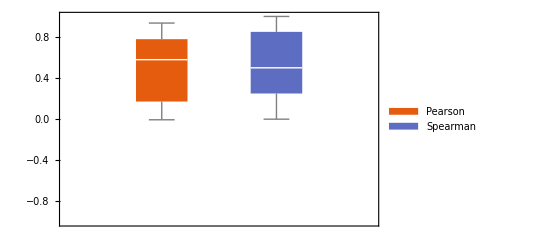

```mathematica
newmanCorrelation=BoxWhiskerChart[{{Correlation@@#&/@Transpose[{newmanTruthOrdered⟦;;,{1,2,3,5,6}⟧,newmanαOrdered⟦;;,{1,2,3,5,6}⟧}],SpearmanRho@@#&/@Transpose[{newmanTruthOrdered⟦;;,{1,2,3,5,6}⟧,newmanαOrdered⟦;;,{1,2,3,5,6}⟧}]}},PlotRange->{-1,1},PlotTheme->"Scientific",GridLines->None,ChartLegends->Placed[SwatchLegend[{"Pearson","Spearman"},LegendFunction->(Framed[#,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.2,0.2}]]]
```

```mathematica
Export["newman_correlation.pdf",newmanCorrelation]
```

newman_correlation.pdf

```mathematica
newmanGodambef=MapThread[godambeInformation[#1,newmanΦf,newmanσf,#2,#3]&,{Transpose@newmanLSf⟦1⟧,Transpose@newmanΨsf,newmannf⟦-1⟧}];
```

```mathematica
newmanGodambe⟦8⟧=godambeInformationInvertible[newmanα⟦-1⟧⟦;;,8⟧,newmanΦ,newmanσ,newmanΨs⟦;;,8⟧,newmann⟦-1,8⟧,0.01];
```

```mathematica
newmanConfidences=Append[singleConfidences[#,Length[newmanσf]^(0.75)],0]&/@newmanGodambef;
```

```mathematica
Mean[7/6*Mean/@Abs[newmanαOrdered-(Append[Prepend[UnitVector[7,#]&/@Range[2,6],{1,0,0,0,0,0,1}],ConstantArray[0,7]].#&/@newmanTruthOrdered)]]
```

0.0699836

```mathematica
TableForm[7/6*{Mean/@Abs[newmanαOrdered-(Append[Prepend[UnitVector[7,#]&/@Range[2,6],{1,0,0,0,0,0,1}],ConstantArray[0,7]].#&/@newmanTruthOrdered)]},TableHeadings->{{"(L̄)_1-ε"},("bulk "<>ToString[#])&/@Range[12]}]
```

| bulk 1 | bulk 2 | bulk 3 | bulk 4 | bulk 5 | bulk 6 | bulk 7 | bulk 8 | bulk 9 | bulk 10 | bulk 11 | bulk 12
(L̄)_1-ε | 0.0668767 | 0.0697086 | 0.0640392 | 0.0673218 | 0.0506341 | 0.0662762 | 0.101064 | 0.0801848 | 0.0763327 | 0.0603446 | 0.0696409 | 0.0673792

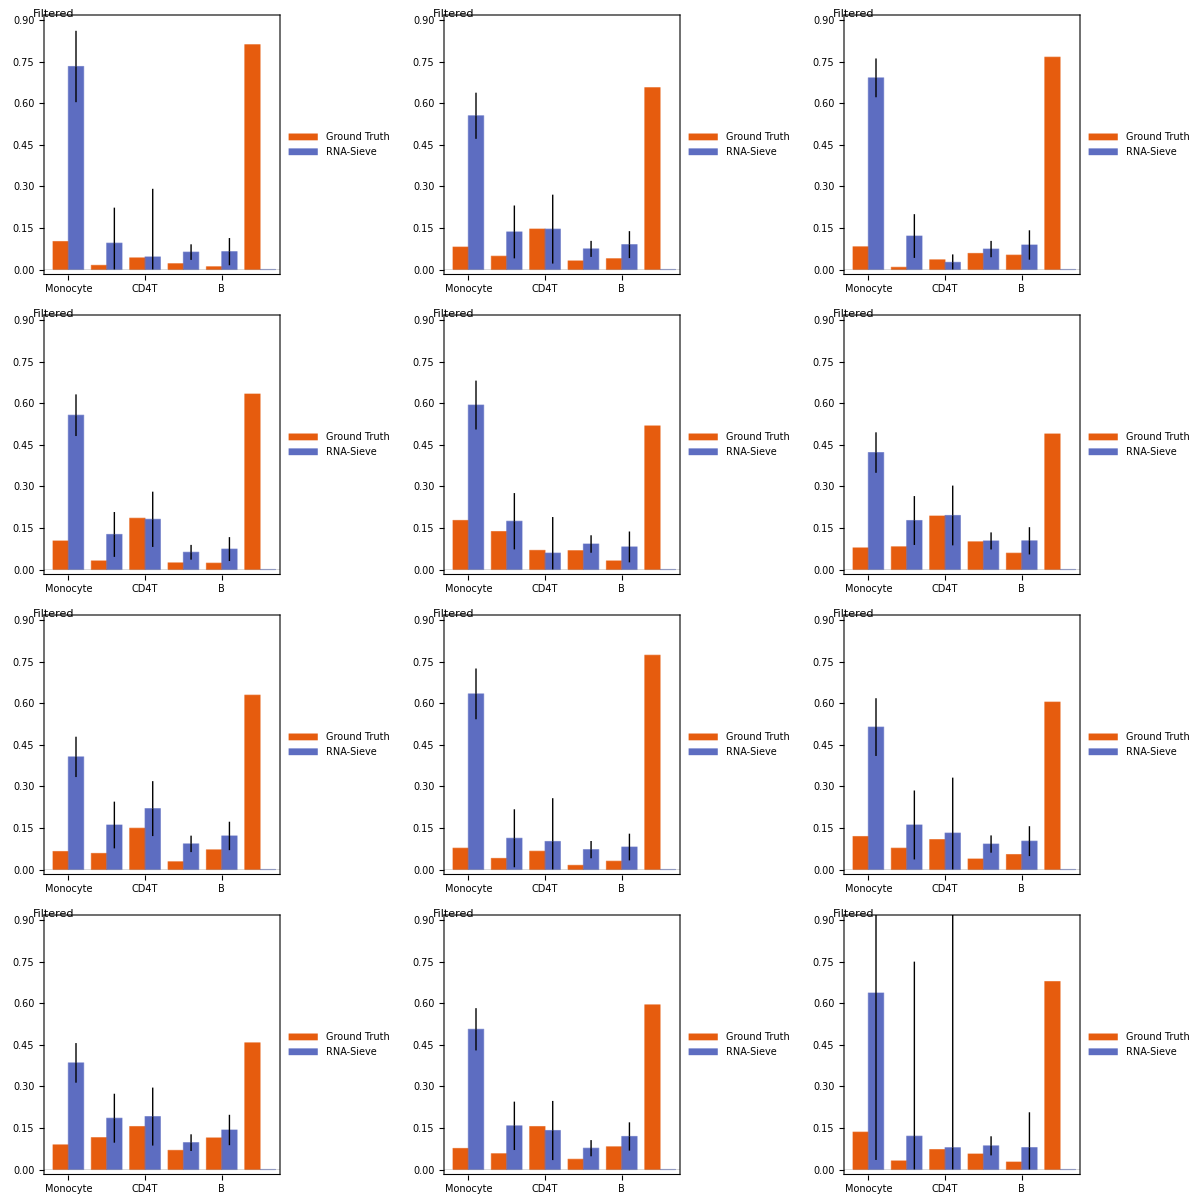

```mathematica
newmanPlot=Grid@Partition[BarChart[Transpose@{newmanTruthOrdered⟦#⟧,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{newmanαOrdered⟦#⟧,newmanConfidences⟦#⟧}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{Drop[nameOrder,{4}],{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth","RNA-Sieve"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.6,0.75}]],Epilog->{Text[Framed[mathWrapper["Filtered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]&/@Range[12],UpTo@3]
```

```mathematica
Export["newman_without_nkt_inferences.csv",Prepend[newmanαOrdered,Drop[nameOrder,{4}]]]
```

newman_without_nkt_inferences.csv

```mathematica
Export["newman_without_nkt_confidences.csv",Prepend[newmanConfidences,Drop[nameOrder,{4}]]]
```

newman_without_nkt_confidences.csv

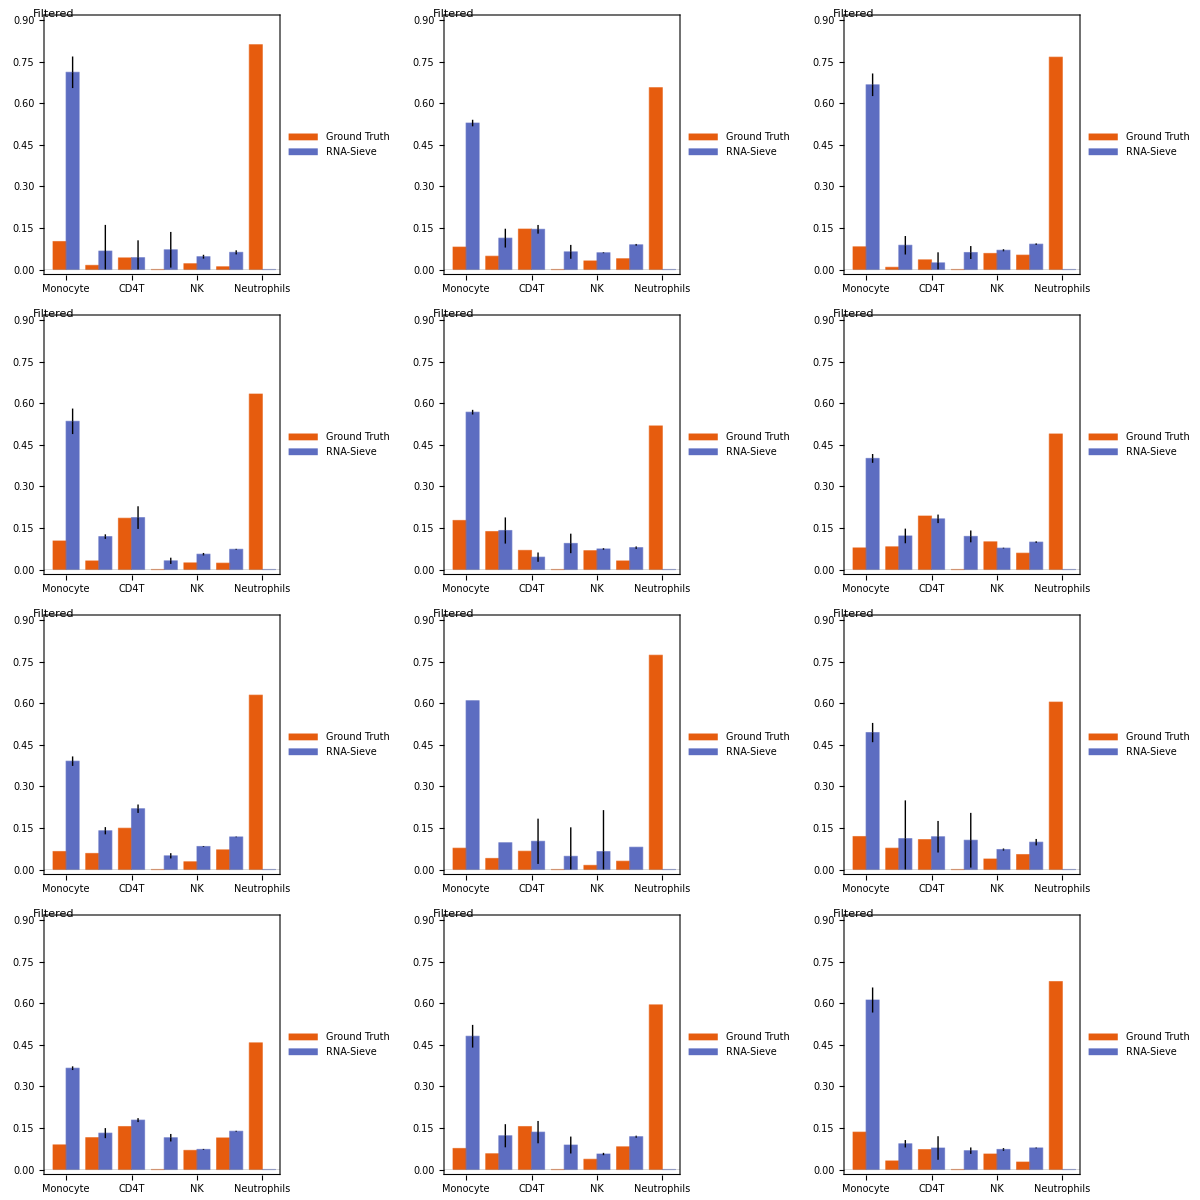

```mathematica
newmanPlot=Grid@Partition[BarChart[Transpose@{newmanTruthOrdered⟦#⟧,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{newmanαOrdered⟦#⟧,newmanConfidences⟦#⟧}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{nameOrder,{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth","RNA-Sieve"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.6,0.75}]],Epilog->{Text[Framed[mathWrapper["Filtered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]&/@Range[12],UpTo@3]
```

```mathematica
Export["newman_filtered.pdf",newmanPlot]
```

newman_filtered.pdf

```mathematica
Export["newman_inferences.csv",Prepend[newmanαOrdered,nameOrder]]
```

newman_inferences.csv

```mathematica
Export["newman_confidences.csv",Prepend[newmanConfidences,nameOrder]]
```

newman_confidences.csv

```mathematica
newneutrophilsTruthOrdered=#⟦{2,3,4,6,5,1}⟧&/@newmanTruth;
newneutrophilsαOrdered=Transpose[newneutrophilsLSf⟦1⟧];
```

```mathematica
Quiet[newneutrophilsGodambe=MapThread[godambeInformation[#1,newneutrophilsΦf,newneutrophilsσf,#2,#3]&,{Transpose@newneutrophilsLSf⟦1⟧,Transpose@newneutrophilsΨsf,newneutrophilsnf⟦-1⟧}]];
```

```mathematica
newneutrophilsConfidences=singleConfidences[#,(Length@newneutrophilsσf)^(1)]&/@newneutrophilsGodambe;
```

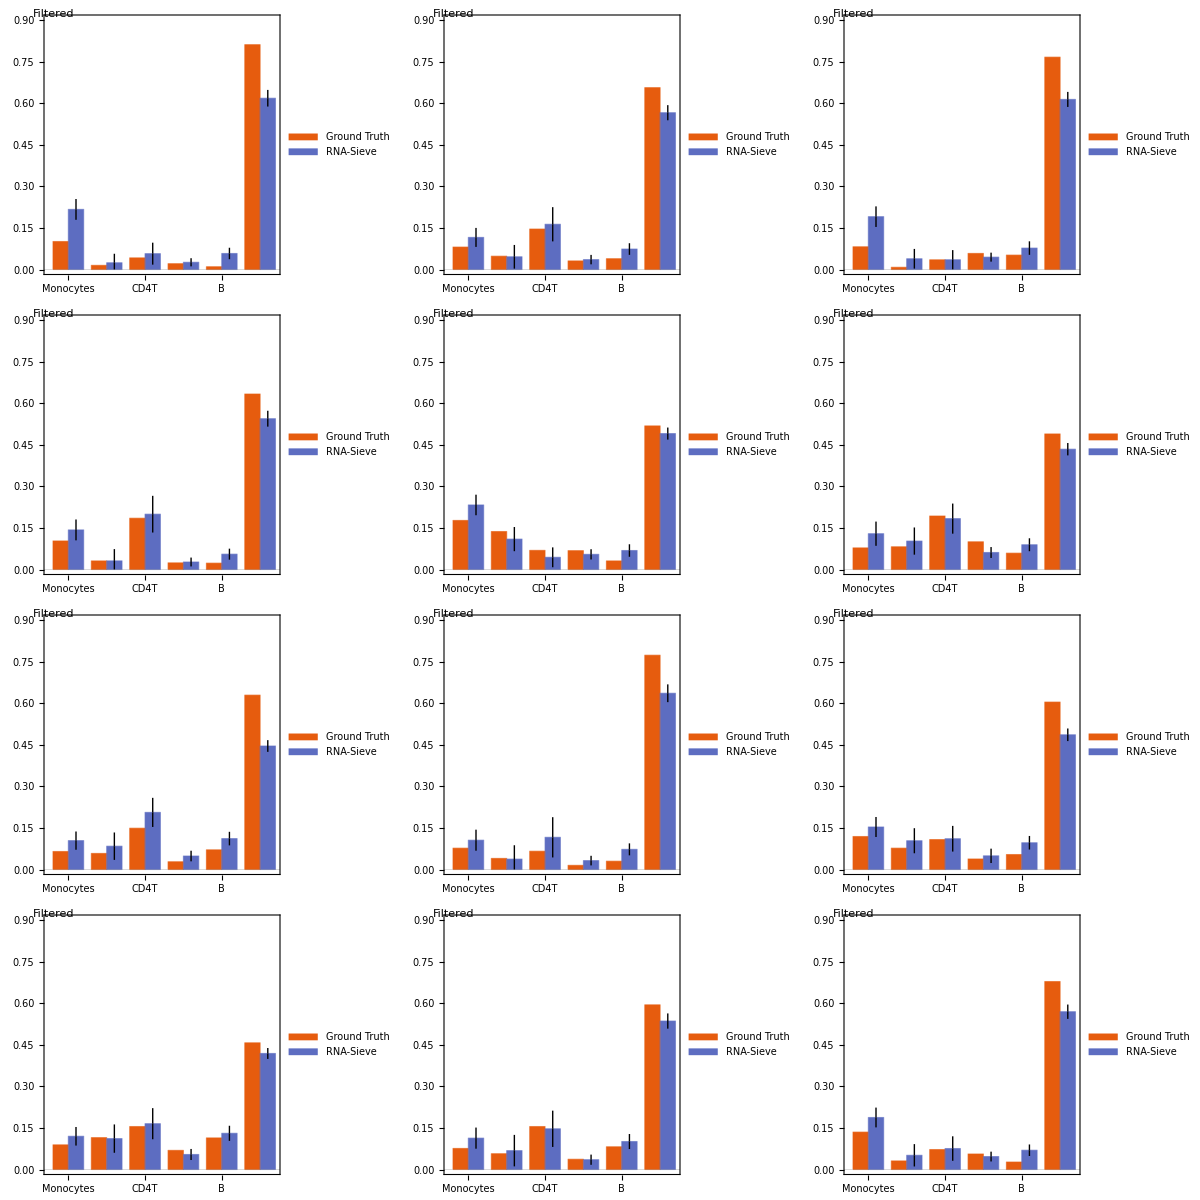

```mathematica
newneutrophilsPlot=Grid@Partition[BarChart[Transpose@{newneutrophilsTruthOrdered⟦#⟧,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{newneutrophilsαOrdered⟦#⟧,newneutrophilsConfidences⟦#⟧}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{newmanTruthnames⟦{2,3,4,6,5,1}⟧,{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth","RNA-Sieve"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.6,0.75}]],Epilog->{Text[Framed[mathWrapper["Filtered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]&/@Range[12],UpTo@3]
```

```mathematica
Export["newman_with_neutrophils_inference.pdf",newneutrophilsPlot]
```

newman_with_neutrophils_inference.pdf

```mathematica
Export["newman_with_neutrophils_inferences.csv",Prepend[newneutrophilsαOrdered,newmanTruthnames⟦{2,3,4,6,5,1}⟧]]
```

newman_with_neutrophils_inferences.csv

```mathematica
Export["newman_with_neutrophils_confidences.csv",Prepend[newneutrophilsConfidences,newmanTruthnames⟦{2,3,4,6,5,1}⟧]]
```

newman_with_neutrophils_confidences.csv

### PBMC

#### Load Data

```mathematica
pbmcm=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc7k_n_sig.csv"]⟦2;;,2;;⟧;
pbmcΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_bulk.csv"]⟦2;;,2;;⟧;
pbmcϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc7k_sig.csv"]⟦2;;,2;;⟧;
pbmcσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc7k_var.csv"]⟦2;;,2;;⟧;
pbmcTruth=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcTruth=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcm1=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc3k_n_sig.csv"]⟦2;;,2;;⟧;
pbmcϕ1=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc3k_sig.csv"]⟦2;;,2;;⟧;
pbmcσ1=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc3k_var.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcm2=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc4k_n_sig.csv"]⟦2;;,2;;⟧;
pbmcϕ2=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc4k_sig.csv"]⟦2;;,2;;⟧;
pbmcσ2=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc4k_var.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcΦNames=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/pbmc7k_sig.csv"]⟦1,2;;⟧
```

{B,CD4T,CD8T,Monocyte,NK}

```mathematica
pbmcTruthNames=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦1,2;;⟧
```

{NK,Monocytes,B,CD4T,CD8T,Other}

```mathematica
pbmcNameOrder={"B","CD4T","CD8T","Monocyte","NK","Other"}
```

{B,CD4T,CD8T,Monocyte,NK,Other}

```mathematica
pbmcneutm=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc7k_n_sig_neut.csv"]⟦2;;,3;;⟧;
pbmcneutΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/monaco_bulk_neut.csv"]⟦2;;,2;;⟧;
pbmcneutϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc7k_sig_neut.csv"]⟦2;;,2;;⟧;
pbmcneutσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc7k_var_neut.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcneutm1=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc3k_n_sig_neut.csv"]⟦2;;,3;;⟧;
pbmcneutϕ1=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc3k_sig_neut.csv"]⟦2;;,2;;⟧;
pbmcneutσ1=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc3k_var_neut.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcneutm2=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc4k_n_sig_neut.csv"]⟦2;;,3;;⟧;
pbmcneutϕ2=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc4k_sig_neut.csv"]⟦2;;,2;;⟧;
pbmcneutσ2=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_with_neutrophils/pbmc4k_var_neut.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcm=Flatten@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_n.csv"]⟦2;;,2;;⟧;
pbmcΨs=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_bulk.csv"]⟦2;;,2;;⟧;
pbmcϕ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_mean.csv"]⟦2;;,2;;⟧;
pbmcσ=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_var.csv"]⟦2;;,2;;⟧;
```

```mathematica
pbmcTruthBulkOrder=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦2;;,1⟧;
pbmcFinalBulkOrder=(If[StringTake[#,1]=="X",StringTake[#,{2,-1}],#]&@StringSplit[#,"_"]⟦1⟧)&/@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_bulk.csv"]⟦1,2;;⟧;
pbmcTruthTypeOrder=Rest@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦1⟧/.{"Other"->"Neutrophil"};
pbmcFinalTypeOrder=Rest@Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/monaco_neutrophil/monaco_mean.csv"]⟦1⟧;
```

```mathematica
pbmcFinalTruth=Transpose[Transpose[Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k/monaco_true_props.csv"]⟦Prepend[1+Ordering[pbmcTruthBulkOrder],1]⟧⟦Prepend[1+InversePermutation@Ordering[pbmcFinalBulkOrder],1]⟧]⟦Prepend[1+Ordering[pbmcTruthTypeOrder],1]⟧⟦Prepend[1+InversePermutation@Ordering[pbmcFinalTypeOrder],1]⟧]⟦2;;,2;;⟧;
```

#### Filter Data

```mathematica
{pbmciterations,pbmcfilters}=Transpose[filterDF[pbmcϕ,pbmcσ,pbmcΨs⟦;;,#⟧]&/@Range[Length@pbmcΨs⟦1⟧]];
{pbmcϕf,pbmcσf,pbmcΨsf}=Extract[#,Intersection@@pbmcfilters]&/@{pbmcϕ,pbmcσ,pbmcΨs};
```

```mathematica
{pbmciterations1,pbmcfilters1}=Transpose[filterDF[pbmcϕ1,pbmcσ1,pbmcΨs⟦;;,#⟧]&/@Range[Length@pbmcΨs⟦1⟧]];
{pbmcϕf1,pbmcσf1,pbmcΨsf1}=Extract[#,Intersection@@pbmcfilters1]&/@{pbmcϕ1,pbmcσ1,pbmcΨs};
```

```mathematica
{pbmciterations2,pbmcfilters2}=Transpose[filterDF[pbmcϕ2,pbmcσ2,pbmcΨs⟦;;,#⟧]&/@Range[Length@pbmcΨs⟦1⟧]];
{pbmcϕf2,pbmcσf2,pbmcΨsf2}=Extract[#,Intersection@@pbmcfilters2]&/@{pbmcϕ2,pbmcσ2,pbmcΨs};
```

```mathematica
{pbmcneutiterations,pbmcneutfilters}=Transpose[filterDF[pbmcneutϕ,pbmcneutσ,pbmcneutΨs⟦;;,#⟧]&/@Range[Length@pbmcneutΨs⟦1⟧]];
{pbmcneutϕf,pbmcneutσf,pbmcneutΨsf}=Extract[#,Intersection@@pbmcneutfilters]&/@{pbmcneutϕ,pbmcneutσ,pbmcneutΨs};
```

```mathematica
{pbmcneutiterations1,pbmcneutfilters1}=Transpose[filterDF[pbmcneutϕ1,pbmcneutσ1,pbmcneutΨs⟦;;,#⟧]&/@Range[Length@pbmcneutΨs⟦1⟧]];
{pbmcneutϕf1,pbmcneutσf1,pbmcneutΨsf1}=Extract[#,Intersection@@pbmcneutfilters1]&/@{pbmcneutϕ1,pbmcneutσ1,pbmcneutΨs};
```

```mathematica
{pbmcneutiterations2,pbmcneutfilters2}=Transpose[filterDF[pbmcneutϕ2,pbmcneutσ2,pbmcneutΨs⟦;;,#⟧]&/@Range[Length@pbmcneutΨs⟦1⟧]];
{pbmcneutϕf2,pbmcneutσf2,pbmcneutΨsf2}=Extract[#,Intersection@@pbmcneutfilters2]&/@{pbmcneutϕ2,pbmcneutσ2,pbmcneutΨs};
```

```mathematica
{pbmciterations,pbmcfilters}=Transpose[filterDF[pbmcϕ,pbmcσ,pbmcΨs⟦;;,#⟧]&/@Range[Length@pbmcΨs⟦1⟧]];
{pbmcϕf,pbmcσf,pbmcΨsf}=Extract[#,Intersection@@pbmcfilters]&/@{pbmcϕ,pbmcσ,pbmcΨs};
```

#### Deconvolve Data

```mathematica
Quiet[{pbmcα,pbmcΦ,pbmcℒ,pbmcn,pbmcLS}=findMixturesJoint[pbmcϕ,pbmcΨs,pbmcσ/.{0|0.->10^(-6)},10^(-10),50,3,pbmcm]];
```

```mathematica
AbsoluteTiming[Quiet[{pbmcαf,pbmcΦf,pbmcℒf,pbmcnf,pbmcLSf}=findMixturesJoint[pbmcϕf,pbmcΨsf,pbmcσf/.{0|0.->10^(-6)},10^(-10),50,3,pbmcm]];]
```

α_0 = {{0.0921007,0.125828,0.140295,0.274272,0.249906,0.117598},{0.0744126,0.086813,0.0725249,0.417729,0.21418,0.134341},{0.0893086,0.143274,0.101347,0.267673,0.21941,0.178988},{0.0556167,0.133296,0.131763,0.253437,0.235619,0.190269},{0.125811,0.214298,0.07936,0.244886,0.219068,0.116578},{0.116389,0.153331,0.0879358,0.299264,0.202253,0.140826},{0.149975,0.088554,0.114336,0.236798,0.172983,0.237354},{0.0939184,0.199409,0.103702,0.215427,0.203169,0.184375},{0.0872571,0.139088,0.0755142,0.315808,0.226373,0.155959},{0.07365,0.182823,0.0494315,0.237391,0.213198,0.243507},{0.0521644,0.0754483,0.0909807,0.397092,0.181735,0.20258},{0.113402,0.20057,0.0625721,0.220209,0.149814,0.253433}}, ℒ_0 = 449677., n_0 = {121.636,127.583,139.417,149.309,137.184,131.604,141.22,130.939,128.83,143.501,122.935,153.241}

α = {{0.0978391,0.0745919,0.0947679,0.306455,0.317472,0.108874},{0.0640942,0.0463637,0.000708665,0.453478,0.300455,0.1349},{0.0900848,0.098464,0.0617505,0.304856,0.277556,0.167289},{0.0536891,0.0887266,0.068571,0.296514,0.308662,0.183837},{0.122342,0.161137,0.00367717,0.287928,0.317421,0.107494},{0.117841,0.108244,0.02556,0.331246,0.274091,0.143019},{0.163015,0.052037,0.0557992,0.272533,0.259886,0.19673},{0.10177,0.162265,0.0711684,0.246989,0.267713,0.150094},{0.0910936,0.111283,0.0537544,0.342839,0.272518,0.128513},{0.0769038,0.136967,0.00529305,0.271647,0.290207,0.218983},{0.0507242,0.0592237,0.0270085,0.42305,0.245285,0.194708},{0.12102,0.120518,0.,0.256332,0.245577,0.256553}}, ℒ = 479718., n = {115.306,123.227,133.063,143.11,131.991,125.977,135.736,123.986,122.462,138.426,116.514,148.352}

α = {{0.0867914,0.0226728,0.,0.304961,0.487199,0.0983752},{0.0322364,0.,0.,0.427677,0.424879,0.115208},{0.0784305,0.0334506,0.,0.305221,0.424578,0.15832},{0.0486874,0.0225491,0.,0.29331,0.463175,0.172279},{0.103763,0.0488461,0.,0.285171,0.457762,0.104459},{0.0999016,0.0233273,0.,0.325537,0.411772,0.139462},{0.139471,0.00966232,0.,0.270781,0.390334,0.189751},{0.090176,0.104717,0.,0.252216,0.408967,0.143924},{0.0766329,0.0410615,0.,0.344323,0.418056,0.119926},{0.065135,0.0374252,0.,0.26751,0.416979,0.212951},{0.0372086,0.,0.,0.410055,0.368544,0.184193},{0.103612,0.0315534,0.,0.251415,0.356966,0.256454}}, ℒ = 424121., n = {123.621,161.576,140.784,153.196,140.776,134.187,145.525,130.727,129.305,147.563,131.113,157.584}

α = {{0.0368494,0.00936874,0.,0.307313,0.604607,0.0418627},{0.,0.180019,0.,0.236481,0.367773,0.215727},{0.0436468,0.,0.,0.307285,0.541824,0.107244},{0.0140194,0.000233572,0.,0.285474,0.573496,0.126778},{0.0577215,0.00852916,0.,0.272526,0.592025,0.0691983},{0.0508033,0.00103397,0.,0.310928,0.532761,0.104474},{0.0725072,0.0246917,0.,0.256703,0.494461,0.151637},{0.0615274,0.031775,0.,0.258524,0.549664,0.0985092},{0.044797,0.000175598,0.,0.344358,0.540332,0.0703373},{0.0260153,0.0160756,0.,0.252691,0.530407,0.174812},{0.,0.09261,0.,0.335293,0.409622,0.162475},{0.0544921,0.00887477,0.,0.239237,0.472807,0.224589}}, ℒ = 411504., n = {124.047,158.008,149.959,163.187,143.557,136.917,145.705,130.178,134.65,149.014,127.908,158.808}

α = {{0.0251473,0.0315608,0.00746762,0.290109,0.643095,0.00262063},{0.0201765,0.,0.,0.2991,0.481484,0.199239},{0.00836352,0.129684,0.,0.257617,0.509628,0.0947083},{0.,0.176326,0.,0.219038,0.504935,0.0997013},{0.0254789,0.0845082,0.,0.247825,0.612252,0.029936},{0.0274548,0.0846506,0.,0.277236,0.542477,0.0681809},{0.0734374,0.,0.,0.252726,0.559824,0.114012},{0.0295546,0.080398,0.,0.249157,0.598863,0.0420278},{0.,0.168233,0.,0.285662,0.505345,0.0407604},{0.0189892,0.0378842,0.,0.238846,0.57248,0.1318},{0.0195658,0.,0.,0.363451,0.494519,0.122464},{0.0391147,0.032848,0.,0.228234,0.517887,0.181916}}, ℒ = 420667., n = {123.349,163.736,146.509,160.75,143.836,136.766,193.437,128.836,133.725,148.293,128.816,157.623}

α_Final = {{0.0368494,0.00936874,0.,0.307313,0.604607,0.0418627},{0.,0.180019,0.,0.236481,0.367773,0.215727},{0.0436468,0.,0.,0.307285,0.541824,0.107244},{0.0140194,0.000233572,0.,0.285474,0.573496,0.126778},{0.0577215,0.00852916,0.,0.272526,0.592025,0.0691983},{0.0508033,0.00103397,0.,0.310928,0.532761,0.104474},{0.0725072,0.0246917,0.,0.256703,0.494461,0.151637},{0.0615274,0.031775,0.,0.258524,0.549664,0.0985092},{0.044797,0.000175598,0.,0.344358,0.540332,0.0703373},{0.0260153,0.0160756,0.,0.252691,0.530407,0.174812},{0.,0.09261,0.,0.335293,0.409622,0.162475},{0.0544921,0.00887477,0.,0.239237,0.472807,0.224589}}, ℒ_Final = 408701., n_Final = {124.047,158.008,149.959,163.187,143.557,136.917,145.705,130.178,134.65,149.014,127.908,158.808}

α_LS = {{0.107139,0.163458,0.193775,0.280291,0.144245,0.111092},{0.0824311,0.085199,0.112726,0.429495,0.154725,0.135424},{0.0826597,0.346252,0.00439303,0.27753,0.14529,0.143875},{0.0509149,0.222419,0.192177,0.262855,0.10837,0.163264},{0.126987,0.249819,0.134142,0.257502,0.118228,0.113322},{0.122392,0.208497,0.119692,0.297384,0.109464,0.14257},{0.17602,0.143525,0.15189,0.252585,0.0876147,0.188365},{0.107911,0.23955,0.1772,0.23989,0.105522,0.129927},{0.0792221,0.273652,0.107268,0.304538,0.102434,0.132886},{0.0877686,0.246574,0.0762524,0.246417,0.124829,0.218159},{0.0622986,0.116755,0.0905825,0.409577,0.135664,0.185123},{0.132763,0.232553,0.051269,0.244818,0.104838,0.23376}}, ℒ_LS = 443952.

{3396.63,Null}

```mathematica
Quiet[{pbmcαf1,pbmcΦf1,pbmcℒf1,pbmcnf1,pbmcLSf1}=findMixturesJoint[pbmcϕf1,pbmcΨsf1,pbmcσf1/.{0|0.->10^(-6)},10^(-10),50,3,pbmcm1]];
```

```mathematica
Quiet[{pbmcαf2,pbmcΦf2,pbmcℒf2,pbmcnf2,pbmcLSf2}=findMixturesJoint[pbmcϕf2,pbmcΨsf2,pbmcσf2/.{0|0.->10^(-6)},10^(-10),50,3,pbmcm2]];
```

```mathematica
AbsoluteTiming[Quiet[{pbmcneutαf,pbmcneutΦf,pbmcneutℒf,pbmcneutnf,pbmcneutLSf}=findMixturesJoint[pbmcneutϕf,pbmcneutΨsf,pbmcneutσf/.{0|0.->10^(-6)},10^(-10),50,3,pbmcneutm]];]
```

α_0 = {{0.111215,0.058305,0.241325,0.154687,0.209217,0.225251},{0.0985304,0.,0.143527,0.307068,0.207976,0.242899},{0.131445,0.0771379,0.191071,0.149316,0.217039,0.233991},{0.090044,0.0744842,0.229699,0.133883,0.211345,0.260545},{0.168495,0.155219,0.16382,0.120645,0.172083,0.219738},{0.139733,0.172626,0.0921223,0.196688,0.184136,0.214695},{0.197362,0.00509472,0.263169,0.125126,0.137697,0.271552},{0.116616,0.135423,0.231402,0.110272,0.167213,0.239074},{0.113347,0.0870385,0.139895,0.206181,0.218395,0.235144},{0.117965,0.1388,0.155661,0.14485,0.179085,0.263639},{0.0771448,0.042618,0.145868,0.31033,0.173984,0.250056},{0.15216,0.181556,0.126781,0.130731,0.14976,0.259012}}, ℒ_0 = 782242., n_0 = {240.411,251.096,256.043,273.193,271.317,260.203,239.456,235.366,237.703,243.759,225.813,258.746}

α = {{0.110028,0.,0.226904,0.186881,0.266514,0.209674},{0.0787612,0.,0.0899101,0.322247,0.289234,0.219848},{0.120793,0.,0.188106,0.200465,0.271517,0.219118},{0.0720277,0.,0.200843,0.194175,0.29141,0.241545},{0.161205,1.9738×10^-11,0.200101,0.171239,0.26454,0.202915},{0.150478,0.0370082,0.110556,0.236175,0.248508,0.217276},{0.182708,0.,0.220173,0.15266,0.231633,0.212826},{0.125608,0.,0.290147,0.148446,0.228802,0.206997},{0.116429,0.,0.207135,0.225027,0.247736,0.203673},{0.122453,0.,0.215397,0.162391,0.262773,0.236986},{0.0697145,0.,0.12326,0.334414,0.237378,0.235234},{0.171219,0.0144069,0.147131,0.175456,0.239405,0.252382}}, ℒ = 856611., n = {241.277,253.895,256.059,274.2,273.652,257.69,250.328,239.631,241.683,249.901,226.262,263.358}

α = {{0.0986726,0.,0.0896186,0.204993,0.455148,0.151568},{0.0657335,0.,0.,0.325538,0.446685,0.162043},{0.104586,0.,0.0609612,0.217992,0.457899,0.158561},{0.0633752,0.,0.0658364,0.211787,0.479197,0.179805},{0.142115,0.,0.07931,0.191904,0.43964,0.147031},{0.137124,0.,0.0425202,0.254033,0.401244,0.165079},{0.174403,0.,0.0766792,0.174787,0.406106,0.168025},{0.116067,0.,0.144475,0.171764,0.412534,0.155159},{0.101752,0.,0.0796734,0.240484,0.429664,0.148426},{0.112657,0.,0.0829576,0.179232,0.442229,0.182925},{0.0613047,0.,0.0225873,0.344171,0.387982,0.183955},{0.158286,0.,0.0558699,0.195083,0.391876,0.198885}}, ℒ = 648250., n = {261.935,305.723,278.104,299.451,299.174,279.086,272.674,259.295,261.63,272.244,249.005,285.999}

α = {{0.0628284,0.,0.,0.219411,0.62268,0.0950809},{1.05799×10^-10,0.,0.0808644,0.3109,0.483167,0.125068},{0.0653651,0.,0.,0.23051,0.605602,0.0985226},{0.030631,0.,0.,0.21613,0.638326,0.114913},{0.0959349,0.,0.,0.200815,0.61287,0.0903802},{0.0808537,0.,0.,0.26112,0.558951,0.0990754},{0.126709,0.,0.,0.187414,0.553609,0.132268},{0.0897181,0.0137021,0.,0.186671,0.597976,0.111932},{0.0681521,0.,0.,0.259588,0.571812,0.100448},{0.0694455,0.,0.,0.202605,0.601977,0.125972},{0.0164136,0.,0.,0.347088,0.513134,0.123363},{0.0999289,0.,0.,0.206387,0.553236,0.140449}}, ℒ = 667757., n = {278.609,299.555,294.381,312.875,331.42,310.384,322.987,271.979,286.898,297.443,335.994,297.484}

α_Final = {{0.0986726,0.,0.0896186,0.204993,0.455148,0.151568},{0.0657335,0.,0.,0.325538,0.446685,0.162043},{0.104586,0.,0.0609612,0.217992,0.457899,0.158561},{0.0633752,0.,0.0658364,0.211787,0.479197,0.179805},{0.142115,0.,0.07931,0.191904,0.43964,0.147031},{0.137124,0.,0.0425202,0.254033,0.401244,0.165079},{0.174403,0.,0.0766792,0.174787,0.406106,0.168025},{0.116067,0.,0.144475,0.171764,0.412534,0.155159},{0.101752,0.,0.0796734,0.240484,0.429664,0.148426},{0.112657,0.,0.0829576,0.179232,0.442229,0.182925},{0.0613047,0.,0.0225873,0.344171,0.387982,0.183955},{0.158286,0.,0.0558699,0.195083,0.391876,0.198885}}, ℒ_Final = 586394., n_Final = {261.935,305.723,278.104,299.451,299.174,279.086,272.674,259.295,261.63,272.244,249.005,285.999}

α_LS = {{0.111506,0.137979,0.20172,0.228769,0.149392,0.170635},{0.0594767,0.300928,0.,0.341055,0.118488,0.180052},{0.118665,0.147368,0.16469,0.232003,0.158358,0.178917},{0.0819869,0.133784,0.206903,0.223854,0.151674,0.201798},{0.145961,0.229749,0.1422,0.200244,0.118068,0.163778},{0.135358,0.193817,0.115605,0.262812,0.12269,0.169717},{0.191271,0.130989,0.195047,0.195283,0.0784206,0.208989},{0.115972,0.22831,0.185448,0.180578,0.108495,0.181198},{0.111401,0.167632,0.144214,0.264887,0.135935,0.175931},{0.11146,0.239249,0.126196,0.199193,0.117736,0.206167},{0.0678737,0.172023,0.092828,0.36519,0.104901,0.197185},{0.152949,0.237775,0.0991295,0.200519,0.0963276,0.2133}}, ℒ_LS = 710069.

{3053.87,Null}

```mathematica
AbsoluteTiming[Quiet[{pbmcneutαf1,pbmcneutΦf1,pbmcneutℒf1,pbmcneutnf1,pbmcneutLSf1}=findMixturesJoint[pbmcneutϕf1,pbmcneutΨsf1,pbmcneutσf1/.{0|0.->10^(-6)},10^(-10),50,3,pbmcneutm1]];]
```

α_0 = {{0.112557,0.129854,0.193526,0.10737,0.203516,0.253177},{0.102145,0.0599978,0.152476,0.267153,0.154364,0.263865},{0.110994,0.125982,0.208673,0.121281,0.177918,0.255152},{0.0903479,0.122589,0.227251,0.108721,0.173461,0.27763},{0.146299,0.204549,0.164347,0.0986542,0.142632,0.243518},{0.147256,0.177497,0.150924,0.143345,0.13432,0.246657},{0.172956,0.0702594,0.200169,0.124512,0.140344,0.29176},{0.0998505,0.184251,0.19712,0.110388,0.153515,0.254876},{0.0951891,0.130702,0.138505,0.194173,0.182993,0.258438},{0.09727,0.203686,0.132387,0.137183,0.154164,0.275309},{0.0841636,0.0713842,0.164178,0.289045,0.116903,0.274326},{0.150522,0.192574,0.170184,0.099104,0.0978054,0.289811}}, ℒ_0 = 701972., n_0 = {238.445,252.376,258.177,272.634,269.708,254.722,238.683,234.27,239.776,245.589,225.016,253.358}

α = {{0.126729,0.0609713,0.22464,0.156028,0.198237,0.233394},{0.109531,1.79688×10^-11,0.194606,0.280746,0.178382,0.236735},{0.116348,0.0767171,0.218804,0.158477,0.189016,0.240637},{0.0949897,0.0363522,0.267008,0.152763,0.195207,0.25368},{0.146991,0.0965792,0.215109,0.144173,0.185841,0.211306},{0.154857,0.0833266,0.198316,0.183267,0.150311,0.229923},{0.191607,0.0330258,0.220745,0.133047,0.170714,0.250862},{0.123237,0.123664,0.227978,0.132706,0.174204,0.218211},{0.121527,0.0865911,0.184531,0.19312,0.186512,0.227719},{0.121152,0.0936724,0.199127,0.151583,0.195271,0.239194},{0.0971678,0.021261,0.196754,0.2915,0.141793,0.251524},{0.172486,0.0615017,0.234814,0.135282,0.139918,0.255998}}, ℒ = 682574., n = {235.076,269.998,253.505,269.593,268.292,250.197,242.715,235.085,238.591,246.997,221.237,255.51}

α = {{0.137413,0.,0.259256,0.186021,0.221854,0.195455},{0.0983688,0.00688674,0.194809,0.309536,0.182319,0.20808},{0.127046,0.00549234,0.249813,0.194105,0.217481,0.206064},{0.0951274,0.,0.288616,0.183378,0.222834,0.210045},{0.154771,0.0138296,0.259309,0.176601,0.211769,0.183721},{0.163739,2.23021×10^-11,0.247429,0.220509,0.171956,0.196367},{0.202857,0.,0.234823,0.15564,0.188143,0.218537},{0.138466,0.0539107,0.263853,0.157429,0.193803,0.192538},{0.137711,0.0121532,0.223073,0.223568,0.205433,0.198061},{0.134065,0.0183819,0.240698,0.180257,0.215013,0.211586},{0.0950845,0.,0.218032,0.319033,0.164336,0.203514},{0.178653,0.,0.272113,0.164107,0.158304,0.226823}}, ℒ = 676085., n = {239.523,258.837,252.867,274.82,267.697,257.421,251.676,236.064,239.33,247.737,224.841,292.839}

α = {{0.112213,0.090505,0.217762,0.181369,0.254527,0.143624},{0.0918381,0.,0.203991,0.325565,0.215872,0.162734},{0.122795,0.,0.256925,0.207923,0.247178,0.165179},{0.0864716,8.07295×10^-11,0.291312,0.198801,0.249456,0.173959},{0.150104,0.,0.279219,0.187375,0.239661,0.143641},{0.155609,0.,0.265824,0.233835,0.180461,0.164272},{0.184502,0.0805996,0.204393,0.152319,0.209748,0.168439},{0.148187,2.41526×10^-11,0.300886,0.172102,0.213632,0.165194},{0.138625,0.,0.239435,0.234626,0.226309,0.161004},{0.135249,0.,0.261671,0.1926,0.237803,0.172677},{0.0834383,0.,0.225822,0.337935,0.178533,0.174273},{0.156859,0.0943363,0.247675,0.164159,0.142265,0.194706}}, ℒ = 637676., n = {244.864,263.436,258.183,276.37,277.912,256.972,257.068,244.695,247.553,251.267,226.966,274.731}

α = {{0.114407,0.,0.257381,0.177252,0.334474,0.116486},{0.0889808,0.,0.211375,0.298436,0.275018,0.126191},{0.11384,0.,0.26367,0.188545,0.318126,0.115819},{0.0824769,0.,0.275706,0.177268,0.334218,0.130332},{0.135348,0.,0.286769,0.169497,0.308742,0.0996446},{0.137381,0.,0.255885,0.215138,0.265055,0.126541},{0.169025,0.,0.235532,0.158735,0.286891,0.149817},{0.124102,0.,0.313841,0.165012,0.279303,0.117742},{0.115183,0.,0.254906,0.22344,0.290204,0.116267},{0.114497,0.,0.275891,0.1813,0.300685,0.127627},{0.0766712,0.,0.221556,0.313624,0.248333,0.139817},{0.118724,0.151804,0.163278,0.153996,0.240275,0.171922}}, ℒ = 551651., n = {262.616,284.168,279.658,299.313,300.773,275.044,274.27,263.543,266.364,273.693,243.959,291.589}

α = {{0.091678,0.,0.231575,0.181285,0.408658,0.0868035},{0.0644322,0.,0.16936,0.29433,0.374306,0.0975709},{0.0904093,0.,0.223907,0.191165,0.400169,0.0943499},{0.0611026,0.,0.241115,0.180804,0.421067,0.0959113},{0.0995189,0.0305397,0.214905,0.168444,0.408525,0.0780666},{0.113926,0.,0.225838,0.212579,0.35629,0.0913667},{0.146535,0.,0.217907,0.16167,0.36029,0.113598},{0.0875175,0.0455016,0.253973,0.155082,0.368118,0.0898083},{0.0936458,0.,0.227035,0.222823,0.361295,0.0952015},{0.0906365,0.,0.248501,0.184073,0.376382,0.100407},{0.0561626,0.,0.190012,0.311352,0.333238,0.109236},{0.134885,0.,0.222626,0.176768,0.337119,0.128602}}, ℒ = 527788., n = {280.164,298.864,297.645,318.892,315.723,290.956,291.544,276.416,282.913,291.934,257.499,306.375}

α = {{0.0791657,0.,0.19536,0.184813,0.466393,0.0742691},{0.0540604,0.,0.130318,0.290542,0.444977,0.0801026},{0.0802033,0.,0.189854,0.193732,0.455513,0.0806967},{0.0522351,0.,0.200686,0.183596,0.481806,0.0816765},{0.0973218,0.,0.203536,0.177701,0.455535,0.0659059},{0.0991791,0.,0.189167,0.213745,0.419984,0.0779253},{0.130352,0.,0.182785,0.166339,0.422212,0.0983112},{0.0918203,0.,0.248412,0.171362,0.408849,0.0795561},{0.0827998,0.,0.195329,0.224895,0.415471,0.0815052},{0.0791306,0.,0.210617,0.188238,0.435332,0.0866832},{0.0452475,0.,0.156449,0.309459,0.395273,0.0935707},{0.0871697,0.100396,0.113524,0.157084,0.443341,0.0984855}}, ℒ = 517672., n = {295.092,312.818,313.192,335.756,337.18,304.779,306.13,295.382,297.118,306.843,269.004,313.748}

α_Final = {{0.091678,0.,0.231575,0.181285,0.408658,0.0868035},{0.0644322,0.,0.16936,0.29433,0.374306,0.0975709},{0.0904093,0.,0.223907,0.191165,0.400169,0.0943499},{0.0611026,0.,0.241115,0.180804,0.421067,0.0959113},{0.0995189,0.0305397,0.214905,0.168444,0.408525,0.0780666},{0.113926,0.,0.225838,0.212579,0.35629,0.0913667},{0.146535,0.,0.217907,0.16167,0.36029,0.113598},{0.0875175,0.0455016,0.253973,0.155082,0.368118,0.0898083},{0.0936458,0.,0.227035,0.222823,0.361295,0.0952015},{0.0906365,0.,0.248501,0.184073,0.376382,0.100407},{0.0561626,0.,0.190012,0.311352,0.333238,0.109236},{0.134885,0.,0.222626,0.176768,0.337119,0.128602}}, ℒ_Final = 519818., n_Final = {280.164,298.864,297.645,318.892,315.723,290.956,291.544,276.416,282.913,291.934,257.499,306.375}

α_LS = {{0.128009,0.201393,0.141189,0.195897,0.144787,0.188725},{0.107476,0.141884,0.113425,0.321006,0.114466,0.201743},{0.120525,0.240733,0.110742,0.197226,0.137137,0.193637},{0.0931152,0.228676,0.140881,0.192932,0.137796,0.2066},{0.149474,0.25776,0.124414,0.183825,0.107274,0.177252},{0.142933,0.259929,0.0853483,0.217064,0.106858,0.187867},{0.187369,0.22306,0.103364,0.170356,0.0912803,0.224572},{0.128276,0.272511,0.130392,0.175451,0.104488,0.188882},{0.127202,0.191929,0.120884,0.243309,0.122384,0.194292},{0.125485,0.240414,0.115346,0.195955,0.11413,0.20867},{0.0896442,0.183088,0.087109,0.336014,0.0916053,0.212539},{0.129763,0.412774,0.,0.159048,0.074206,0.224209}}, ℒ_LS = 624855.

{3949.97,Null}

```mathematica
AbsoluteTiming[Quiet[{pbmcneutαf2,pbmcneutΦf2,pbmcneutℒf2,pbmcneutnf2,pbmcneutLSf2}=findMixturesJoint[pbmcneutϕf2,pbmcneutΨsf2,pbmcneutσf2/.{0|0.->10^(-6)},10^(-10),50,3,pbmcneutm2]];]
```

α_0 = {{0.13363,0.0205912,0.262459,0.162502,0.190675,0.230143},{0.121419,0.,0.191296,0.296676,0.148732,0.241877},{0.132249,0.0566776,0.209928,0.178556,0.177465,0.245125},{0.104274,0.0474924,0.258397,0.153582,0.166293,0.269962},{0.170472,0.170497,0.156932,0.132233,0.14248,0.227387},{0.162381,0.126491,0.150411,0.21595,0.125647,0.21912},{0.20505,0.0388256,0.224208,0.146712,0.114639,0.270565},{0.121392,0.196165,0.176111,0.116156,0.144732,0.245443},{0.122173,0.105723,0.147032,0.212212,0.173031,0.239829},{0.12164,0.189741,0.13245,0.144926,0.141826,0.269418},{0.105427,0.,0.199239,0.321077,0.120319,0.253938},{0.176114,0.172144,0.136595,0.129214,0.114426,0.271506}}, ℒ_0 = 900894., n_0 = {241.596,271.728,261.864,276.641,277.349,264.432,248.618,245.174,247.182,254.05,229.836,263.577}

α = {{0.128636,0.,0.262904,0.1932,0.205256,0.210004},{0.0979275,0.,0.145189,0.316293,0.185437,0.255153},{0.126069,1.64718×10^-11,0.232956,0.206175,0.203011,0.231789},{0.0859382,0.,0.265186,0.193171,0.209925,0.24578},{0.177084,0.0120026,0.227758,0.178479,0.199004,0.205673},{0.170355,0.,0.196711,0.250583,0.169969,0.212383},{0.209612,0.,0.231251,0.162712,0.168251,0.228173},{0.141843,0.06918,0.23408,0.150043,0.183564,0.22129},{0.136331,0.0320989,0.190659,0.228444,0.194861,0.217607},{0.137096,0.0521055,0.187362,0.165491,0.208257,0.249688},{0.082583,0.,0.191323,0.340276,0.16139,0.224428},{0.18985,0.014343,0.198761,0.175573,0.167282,0.254191}}, ℒ = 906735., n = {242.923,265.505,261.15,278.207,278.95,263.447,255.011,247.613,249.166,258.006,230.517,267.283}

α = {{0.116225,0.,0.158642,0.215824,0.363126,0.146182},{0.0884891,0.,0.0568298,0.333457,0.316696,0.204528},{0.11236,0.,0.141726,0.22838,0.351122,0.166413},{0.0785168,0.,0.156348,0.214834,0.364089,0.186211},{0.157076,0.,0.148837,0.203096,0.34161,0.149379},{0.151158,0.,0.103626,0.268535,0.311965,0.164717},{0.190613,0.,0.141243,0.188775,0.305153,0.174216},{0.135923,0.,0.196032,0.181257,0.314333,0.172455},{0.122452,0.,0.137185,0.25454,0.328601,0.157222},{0.129096,0.,0.14351,0.19248,0.337751,0.197163},{0.073722,0.,0.0972318,0.353193,0.294404,0.181449},{0.170814,0.,0.123504,0.20031,0.299159,0.206213}}, ℒ = 657641., n = {257.522,282.547,277.08,296.165,297.887,278.466,271.009,261.705,263.92,275.016,244.332,282.859}

α = {{0.088593,0.,0.0661695,0.245172,0.49284,0.107225},{0.0494334,0.,0.,0.362328,0.445686,0.142552},{0.0874727,0.,0.0431829,0.2623,0.485649,0.121395},{0.0582117,0.,0.0443973,0.246375,0.506222,0.144794},{0.127945,0.,0.0494845,0.229167,0.484845,0.108559},{0.117063,0.,0.0189869,0.299016,0.449292,0.115642},{0.158597,0.,0.0422701,0.214978,0.43429,0.149865},{0.110985,0.0139646,0.0951958,0.196204,0.452124,0.131526},{0.0977075,0.,0.0554068,0.279461,0.449329,0.118096},{0.0966961,0.0133952,0.0495263,0.216961,0.47069,0.152731},{0.0470155,0.,0.00587653,0.384839,0.422692,0.139577},{0.137597,0.0178452,0.0117075,0.226834,0.440393,0.165623}}, ℒ = 617061., n = {266.005,312.055,284.828,304.374,305.727,284.402,280.426,268.428,272.369,282.279,256.018,289.112}

α = {{0.0728341,0.,0.0263854,0.25356,0.575732,0.071489},{0.0219771,0.,0.0522472,0.338024,0.458273,0.129479},{0.0696614,0.,0.00450589,0.271802,0.572787,0.0812436},{0.0434466,0.,0.0130738,0.253468,0.59285,0.0971612},{0.0974167,2.98736×10^-11,0.0232292,0.238625,0.575414,0.0653154},{0.0864334,0.,0.00913196,0.303859,0.53125,0.0693256},{0.134401,0.,0.0117279,0.22241,0.517787,0.113674},{0.0868149,0.0413454,0.0183643,0.210618,0.550563,0.0922949},{0.079186,0.,0.0111252,0.289394,0.535284,0.0850105},{0.0719537,0.0272019,0.,0.228761,0.564935,0.107148},{0.0109742,0.,0.0725161,0.360107,0.460741,0.095662},{0.109217,0.00489308,0.,0.23686,0.529478,0.119551}}, ℒ = 580120., n = {277.306,301.663,296.192,316.518,317.085,293.203,290.234,278.13,282.949,292.875,259.305,297.285}

α_Final = {{0.088593,0.,0.0661695,0.245172,0.49284,0.107225},{0.0494334,0.,0.,0.362328,0.445686,0.142552},{0.0874727,0.,0.0431829,0.2623,0.485649,0.121395},{0.0582117,0.,0.0443973,0.246375,0.506222,0.144794},{0.127945,0.,0.0494845,0.229167,0.484845,0.108559},{0.117063,0.,0.0189869,0.299016,0.449292,0.115642},{0.158597,0.,0.0422701,0.214978,0.43429,0.149865},{0.110985,0.0139646,0.0951958,0.196204,0.452124,0.131526},{0.0977075,0.,0.0554068,0.279461,0.449329,0.118096},{0.0966961,0.0133952,0.0495263,0.216961,0.47069,0.152731},{0.0470155,0.,0.00587653,0.384839,0.422692,0.139577},{0.137597,0.0178452,0.0117075,0.226834,0.440393,0.165623}}, ℒ_Final = 583321., n_Final = {266.005,312.055,284.828,304.374,305.727,284.402,280.426,268.428,272.369,282.279,256.018,289.112}

α_LS = {{0.117264,0.131309,0.242539,0.211347,0.121508,0.176033},{0.0681658,0.200559,0.165945,0.317297,0.0582026,0.189831},{0.113353,0.153191,0.198221,0.222599,0.124319,0.188317},{0.0845756,0.136252,0.241554,0.206798,0.116441,0.214379},{0.142243,0.242161,0.171429,0.19034,0.0863668,0.167459},{0.138509,0.198132,0.143156,0.257052,0.0945849,0.168566},{0.188009,0.146284,0.208757,0.178656,0.0579492,0.220345},{0.114745,0.260811,0.186608,0.16053,0.0827815,0.194525},{0.110813,0.199594,0.156288,0.241425,0.106798,0.185081},{0.107421,0.273389,0.139776,0.176553,0.0864049,0.216456},{0.0711184,0.173622,0.136242,0.340062,0.0783575,0.200597},{0.155189,0.246115,0.113801,0.182236,0.0795958,0.223064}}, ℒ_LS = 805680.

{4151.66,Null}

#### Interpretation

```mathematica
pbmcTruthOrdered=Append[#,0]⟦{3,4,5,2,1,6}⟧&/@pbmcTruth;
pbmcαOrdered=Append[#,0]&/@Transpose[pbmcLSf⟦1⟧];
```

```mathematica
pbmcGodambef=MapThread[godambeInformation[Most[#1],pbmcΦf,pbmcσf,#2,#3]&,{pbmcαOrdered,Transpose@pbmcΨsf,pbmcnf⟦-1⟧}];
pbmcGodambef1=MapThread[godambeInformation[Most[#1],pbmcΦf1,pbmcσf1,#2,#3]&,{pbmcαOrdered,Transpose@pbmcΨsf1,pbmcnf1⟦-1⟧}];
pbmcGodambef2=MapThread[godambeInformation[Most[#1],pbmcΦf2,pbmcσf2,#2,#3]&,{pbmcαOrdered,Transpose@pbmcΨsf2,pbmcnf2⟦-1⟧}];
```

```mathematica
pbmcConfidencesf=Append[singleConfidences[#,Length[pbmcΦf]^(0.75)],0]&/@pbmcGodambef;
pbmcConfidencesf1=Append[singleConfidences[#,Length[pbmcΦf1]^(0.75)],0]&/@pbmcGodambef1;
pbmcConfidencesf2=Append[singleConfidences[#,Length[pbmcΦf2]^(0.75)],0]&/@pbmcGodambef2;
```

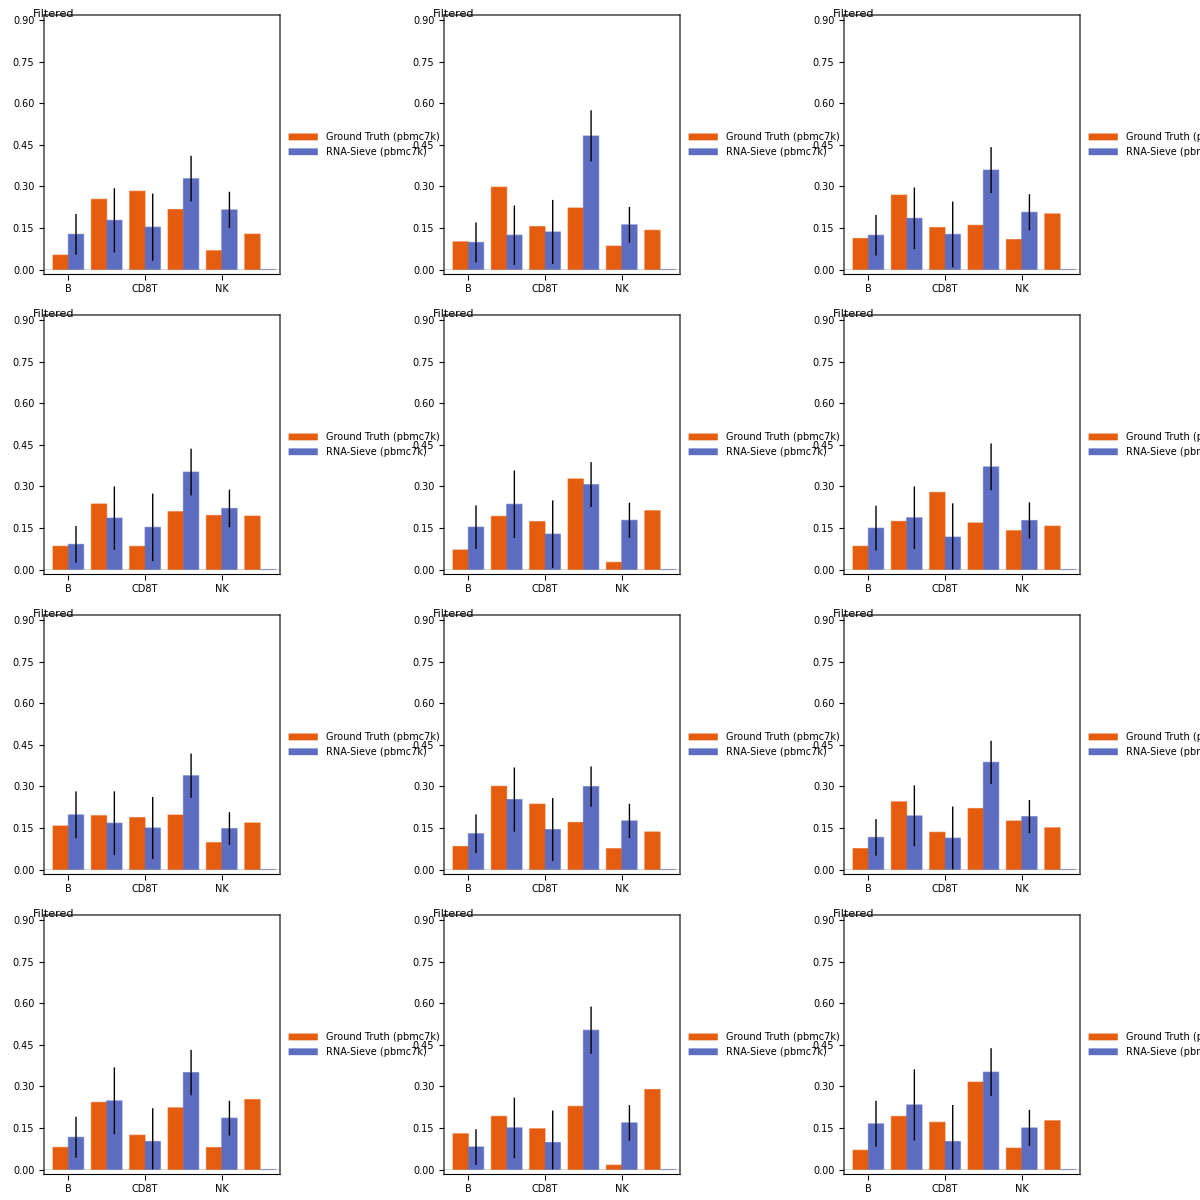

```mathematica
pbmcPlot=Grid@Partition[BarChart[Transpose@{pbmcTruthOrdered⟦#⟧,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{pbmcαOrdered⟦#⟧,pbmcConfidencesf⟦#⟧}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{pbmcNameOrder,{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth (pbmc7k)","RNA-Sieve (pbmc7k)"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.7,0.75}]],Epilog->{Text[Framed[mathWrapper["Filtered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]&/@Range[12],UpTo@3]
```

```mathematica
Export["pbmc_filtered_7k.pdf",pbmcPlot]
```

pbmc_filtered_7k.pdf

```mathematica
Export["pbmc_7k_inferences.csv",Prepend[pbmcαOrdered,pbmcNameOrder]]
```

pbmc_4k_inferences.csv

```mathematica
Export["pbmc_7k_confidences.csv",Prepend[pbmcConfidencesf2,pbmcNameOrder]]
```

pbmc_4k_confidences.csv

```mathematica
pbmcNeutTruthOrdered=#⟦{3,4,5,2,1,6}⟧&/@pbmcTruth;
pbmcNeutαOrdered=Transpose[pbmcneutLSf2⟦1⟧];
```

```mathematica
pbmcNeutGodambef=MapThread[godambeInformation[#1,pbmcneutΦf2,pbmcneutσf2,#2,#3]&,{pbmcNeutαOrdered,Transpose@pbmcneutΨsf2,pbmcneutnf2⟦-1⟧}];
```

```mathematica
pbmcNeutConfidencesf=singleConfidences[#,Length[pbmcneutΦf2]^(0.75)]&/@pbmcNeutGodambef;
```

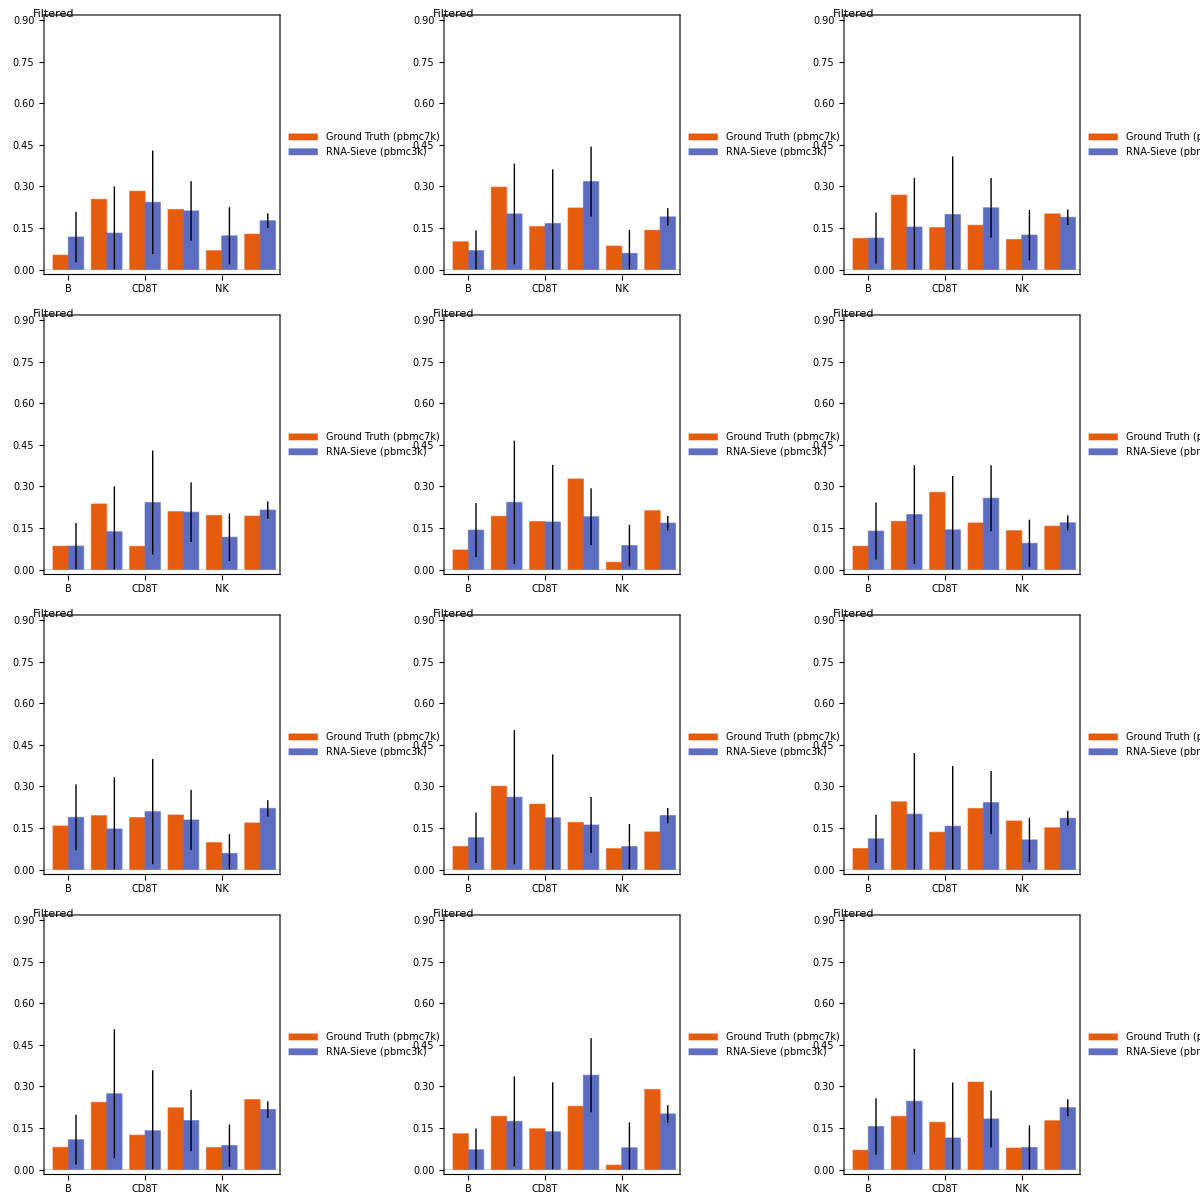

```mathematica
pbmcNeutPlot=Grid@Partition[BarChart[Transpose@{pbmcNeutTruthOrdered⟦#⟧,MapThread[Around[#1,{Min[#1,#2],Min[1-#1,#2]}]&,{pbmcNeutαOrdered⟦#⟧,pbmcNeutConfidencesf⟦#⟧}]},ImageSize->{300+100,200},AspectRatio->Full,BarSpacing->{0,0.5},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,None}},ChartLabels->{Append[Most[pbmcNameOrder],"Other/Neutrophils"],{""}},PlotRange->{0,0.9},ChartLegends->Placed[SwatchLegend[{"Ground Truth (pbmc7k)","RNA-Sieve (pbmc3k)"},LegendFunction->(Framed[#1,RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]]&)],Scaled[{0.7,0.75}]],Epilog->{Text[Framed[mathWrapper["Filtered",18],RoundingRadius->5,Background->White,FrameMargins->5,FrameStyle->Dashed],Scaled[{-0.0475,1.025}],{-1,1}]}]&/@Range[12],UpTo@3]
```

```mathematica
Export["pbmc4k_with_neutrophils_inference.pdf",pbmcNeutPlot]
```

pbmc4k_with_neutrophils_inference.pdf

```mathematica
Export["pbmc4k_with_neutrophils_inferences.csv",Prepend[pbmcNeutαOrdered,pbmcNameOrder]]
```

pbmc4k_with_neutrophils_inferences.csv

```mathematica
Export["pbmc4k_with_neutrophils_confidences.csv",Prepend[pbmcNeutConfidencesf,pbmcNameOrder]]
```

pbmc4k_with_neutrophils_confidences.csv

## Method Comparison

### Load Data

```mathematica
algorithms={"true","rnasieve","bisque","music","scdc","nnls"};
datasets={"pbmc","cell_line","newman"};
```

```mathematica
types[datasets⟦1⟧]=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_results/true7k.csv"]⟦2;;,1⟧;
```

```mathematica
(inference[#]=Import["/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/pbmc7k_results/"<>#<>"7k.csv"]⟦2;;,2;;⟧)&/@algorithms;
```

### Comparison

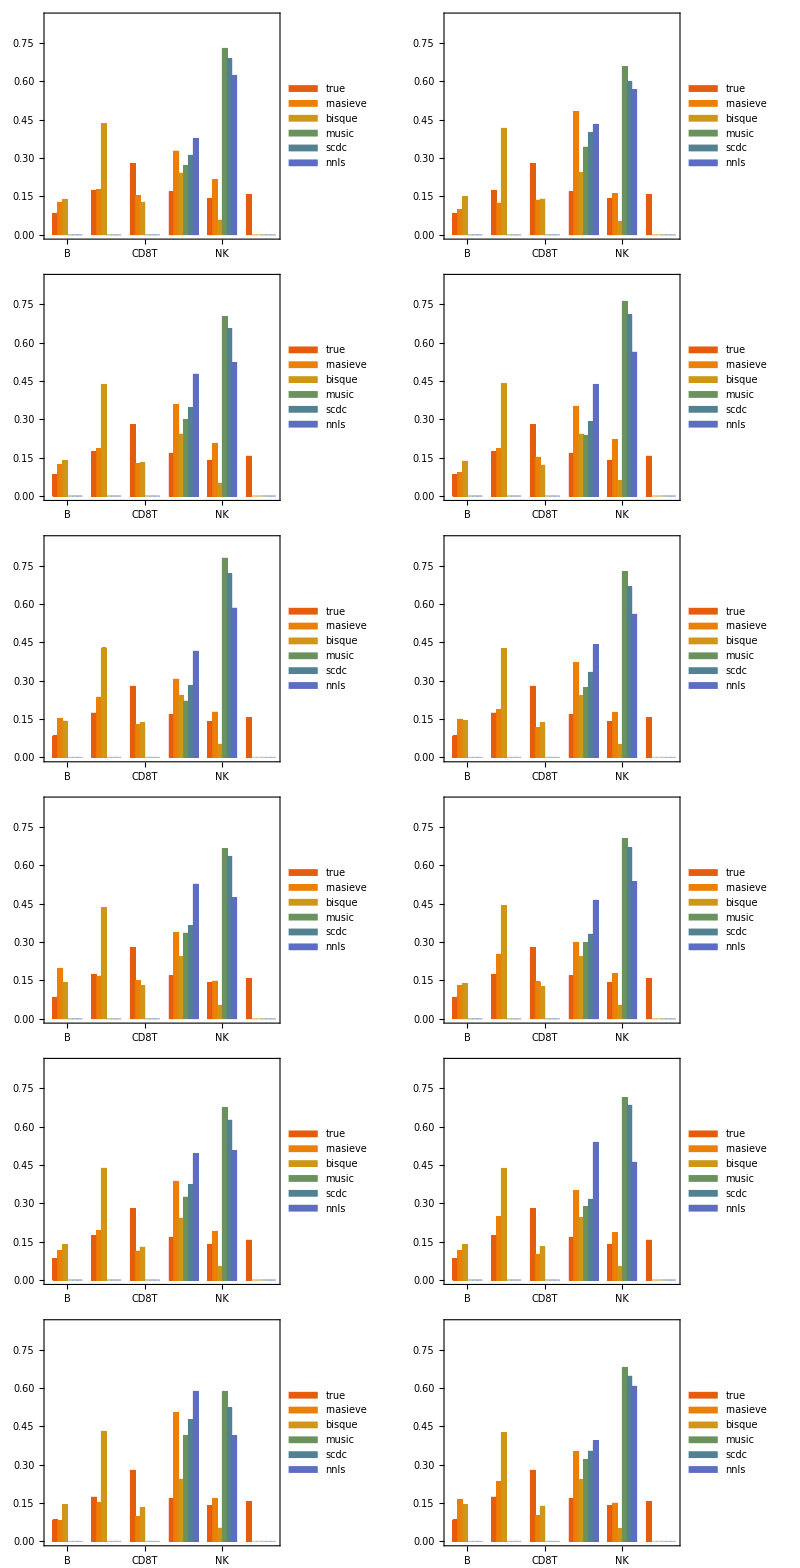

```mathematica
Grid[
Partition[
Table[
BarChart[Transpose@Prepend[Append[inference[#]⟦;;,i⟧,0]&/@Rest[algorithms],inference["true"]⟦;;,1⟧],
PlotTheme->"Scientific",
BarSpacing->{0,2},
ImageSize->{600,300},
AspectRatio->Full,
GridLines->None,
PlotRange->{0,0.85},
FrameTicks->{{Automatic,Automatic},{Automatic,None}},
ChartLabels->{types[datasets⟦1⟧],{""}},
ChartLegends->Placed[SwatchLegend[algorithms,LegendLayout->"Row",LegendFunction->(Framed[#,RoundingRadius->5,FrameStyle->Opacity[.25]]&)],Scaled[{0.35,0.8}]]
],
{i,Length@Transpose[inference["true"]]}
],
UpTo@2]
]
```

```mathematica
nonSingularCorrelation[data1_,data2_]:=If[StandardDeviation[data1]*StandardDeviation[data2]≤0,0,Correlation@@{data1,data2}]
```

```mathematica
nonSingularSpearman[data1_,data2_]:=If[StandardDeviation[data1]*StandardDeviation[data2]≤0,0,SpearmanRho@@{data1,data2}]
```

```mathematica
scientificColours=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

```mathematica
metrics={"pearson","spearman","L1-raw","L1-rescaled","L1-Other→Uniform"}~Join~(("L1-Other→"<>types["pbmc"]⟦#⟧)&/@Range[5])~Join~{"L∞-raw","L∞-rescaled","L∞-Other→Uniform"}~Join~(("L∞-Other→"<>types["pbmc"]⟦#⟧)&/@Range[5])~Join~{"H-raw","H-rescaled","H-Other→Uniform"}~Join~(("H-Other→"<>types["pbmc"]⟦#⟧)&/@Range[5]);
```

```mathematica
comparison["pearson"]=Table[MapThread[nonSingularCorrelation@@{#1,#2}&,{Most@inference["true"],inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["spearman"]=Table[MapThread[nonSingularSpearman@@{#1,#2}&,{Most@inference["true"],inference[algorithm]}],{algorithm,Rest@algorithms}];
```

```mathematica
comparison["L1-raw"]=Table[MapThread[Mean@Abs[#1-#2]&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["L1-rescaled"]=Table[MapThread[Mean@Abs[Normalize[#1,Total]-Normalize[#2,Total]]&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["L∞-raw"]=Table[MapThread[Max@Abs[#1-#2]&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["L∞-rescaled"]=Table[MapThread[Max@Abs[Normalize[#1,Total]-Normalize[#2,Total]]&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["H-raw"]=Table[MapThread[relativeEntropy@@{#2,#1}&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
comparison["H-rescaled"]=Table[MapThread[relativeEntropy@@{Normalize[#2,Total],Normalize[#1,Total]}&,{Transpose[Most@inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
```

```mathematica
Table[comparison["L1-Other→"<>types["pbmc"]⟦shift⟧]=Table[MapThread[Mean@Abs[Insert[UnitVector[6,#]&/@Drop[Range[1,5],{shift}],UnitVector[6,shift]+{0,0,0,0,0,1},shift].#1-#2]&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}],{shift,1,5}];
comparison["L1-Other→Uniform"]=Table[MapThread[Mean@Abs[Join[IdentityMatrix[5],ConstantArray[{1/5},5],2].#1-#2]&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
Table[comparison["L∞-Other→"<>types["pbmc"]⟦shift⟧]=Table[MapThread[Max@Abs[Insert[UnitVector[6,#]&/@Drop[Range[1,5],{shift}],UnitVector[6,shift]+{0,0,0,0,0,1},shift].#1-#2]&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}],{shift,1,5}];
comparison["L∞-Other→Uniform"]=Table[MapThread[Max@Abs[Join[IdentityMatrix[5],ConstantArray[{1/5},5],2].#1-#2]&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
Table[comparison["H-Other→"<>types["pbmc"]⟦shift⟧]=Table[MapThread[relativeEntropy@@{#2,Insert[UnitVector[6,#]&/@Drop[Range[1,5],{shift}],UnitVector[6,shift]+{0,0,0,0,0,1},shift].#1}&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}],{shift,1,5}];
comparison["H-Other→Uniform"]=Table[MapThread[relativeEntropy@@{#2,Join[IdentityMatrix[5],ConstantArray[{1/5},5],2].#1}&,{Transpose[inference["true"]],Transpose@inference[algorithm]}],{algorithm,Rest@algorithms}];
```

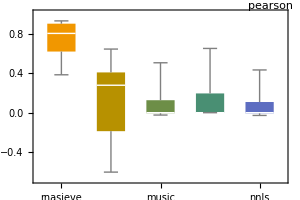
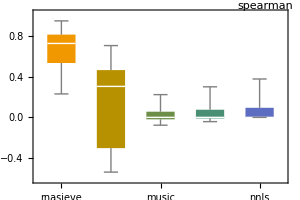
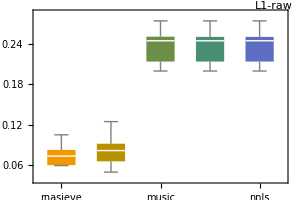
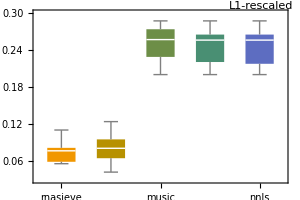
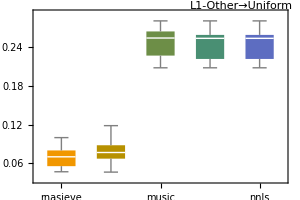
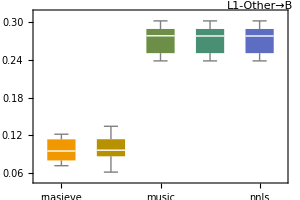
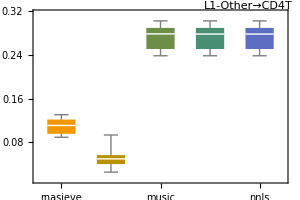
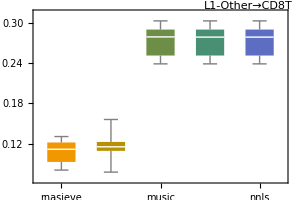
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
comparisonPlot=Grid[Partition[BoxWhiskerChart[comparison[#],Epilog->{Text[Framed[mathWrapper[#,18],RoundingRadius->5,Background->White,FrameStyle->AbsoluteThickness[2]],Scaled[{1.02,1.05}],{1,1}]},PlotTheme->"Scientific",GridLines->None,ImageSize->(1.{300,200}),AspectRatio->Full,ChartStyle->scientificColours⟦{3,8,-3,5,2}⟧,ChartLabels->(mathWrapper[#,14]&/@Rest[algorithms])]&/@metrics,UpTo@4],Spacings->{2,1}]
```

```mathematica
Export["pbmc_comparison.pdf",comparisonPlot]
```

pbmc_comparison.pdf

## Real Data

### Load Data

```mathematica
realTissues={"limb_muscle","marrow","spleen"};
```

```mathematica
deconvolutionPath="/Users/Dani/Dropbox (Personal)/Berkeley/Research/Deconvolution/";
realDataPath=deconvolutionPath<>"real_data/bulk/";
```

```mathematica
Table[realBulkIDs[tissue]=Import[realDataPath<>tissue<>"/exp.csv"]⟦1,2;;⟧,{tissue,realTissues}];
Table[realBulks[tissue]=Import[realDataPath<>tissue<>"/exp.csv"]⟦1;;,2;;⟧,{tissue,realTissues}];
```

```mathematica
Table[realFrefNames[tissue]=Sort@FileNames["*.csv",realDataPath<>tissue<>"/facs/mean"],{tissue,realTissues}];
Table[realFrefs[tissue]=Transpose[SortBy[Transpose[Import[#]⟦;;,2;;⟧],First]]&/@realFrefNames[tissue],{tissue,realTissues}];
```

```mathematica
Table[realFmMat[tissue]=SortBy[Transpose@SortBy[Transpose[Import[realDataPath<>tissue<>"/facs/m_mat.csv"]],First],First],{tissue,realTissues}];
```

```mathematica
combineIndividualRefs[refs_,mMat_]:=With[{convexWeights=Normalize[#,Total]&/@mMat⟦2;;,2;;⟧},Transpose@MapThread[#2.#1&,{convexWeights,Transpose[refs⟦;;,2;;,;;⟧,{3,2,1}]}]]
```

```mathematica
Table[realFref[tissue]=combineIndividualRefs[realFrefs[tissue],realFmMat[tissue]],{tissue,realTissues}];
```

```mathematica
Table[realFvars[tissue]=Transpose[SortBy[Transpose[Import[#]⟦;;,2;;⟧],First]]&/@(StringReplace[#,"mean"->"var"]&/@realFrefNames[tissue]),{tissue,realTissues}];
```

```mathematica
combineIndividualVars[vars_,refs_,mMat_]:=With[{convexWeights=Normalize[#,Total]&/@mMat⟦2;;,2;;⟧},Transpose@MapThread[(#2^2+#3).#1-(#2.#1)^2&,{convexWeights,Transpose[refs⟦;;,2;;,;;⟧,{3,2,1}],Transpose[vars⟦;;,2;;,;;⟧,{3,2,1}]}]]
```

```mathematica
Table[realFvar[tissue]=combineIndividualVars[realFvars[tissue]/.{"NA"->0.},realFrefs[tissue],realFmMat[tissue]],{tissue,realTissues}];
```

```mathematica
Table[realFmList[tissue]=Total/@realFmMat[tissue]⟦2;;,2;;⟧,{tissue,realTissues}];
```

### Filter Data

```mathematica
Table[Length[realFsimpleFilter[tissue]=Intersection@@(simpleFilter[realFref[tissue],#]&/@Drop[Transpose[realBulks[tissue]⟦2;;⟧],If[tissue==realTissues⟦2⟧,{40},{}]])],{tissue,realTissues}]
```

{9542,10179,9051}

```mathematica
Table[Length[realFsimpleFilter[tissue]=Intersection@@(simpleFilter[realFref[tissue],#]&/@Drop[Transpose[realBulks[tissue]⟦2;;⟧],If[tissue==realTissues⟦2⟧,{40},{}]])],{tissue,realTissues}]
```

```mathematica
Table[realΨs[tissue]=Extract[realBulks[tissue]⟦2;;⟧,realFsimpleFilter[tissue]],{tissue,realTissues}];
Table[realϕ[tissue]=Extract[realFref[tissue],realFsimpleFilter[tissue]],{tissue,realTissues}];
Table[realσ[tissue]=Extract[realFvar[tissue],realFsimpleFilter[tissue]],{tissue,realTissues}];
```

```mathematica
Table[Length[realFDfilter[tissue]=Intersection@@(filterFD[realFref[tissue],realFvar[tissue],#]⟦2⟧&/@Transpose[realBulks[tissue]⟦2;;⟧])],{tissue,realTissues}]
```

Infinity::indet: Indeterminate expression 0. ∞ encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
{1611,0,2530}
```

```mathematica
Table[realΨsf[tissue]=Extract[realBulks[tissue]⟦2;;⟧,realFDfilter[tissue]],{tissue,realTissues}];
Table[realϕf[tissue]=Extract[realFref[tissue],realFDfilter[tissue]],{tissue,realTissues}];
Table[realσf[tissue]=Extract[realFvar[tissue],realFDfilter[tissue]],{tissue,realTissues}];
```

### Deconvolve Data

```mathematica
With[{tissue=realTissues⟦1⟧},AbsoluteTiming[Quiet[{realFαf[tissue],realFΦf[tissue],realFℒf[tissue],realFnf[tissue],realFLSf[tissue]}=findMixturesJoint[realϕ[tissue],realΨs[tissue],realσ[tissue]/.{0|0.->10^(-6)},10^(-10),50,3,realFmList[tissue]]];]
]
```

α_0 = {{0.,0.,0.0320367,0.14103,0.326996,0.499938},{0.,0.,0.11001,0.154677,0.291123,0.44419},{0.,0.,0.040761,0.164246,0.304094,0.490898},{0.,0.,0.0373592,0.0881218,0.289002,0.585517},{0.,0.0257486,0.0179385,0.112114,0.360349,0.48385},{0.00142498,0.,0.014612,0.0526081,0.385672,0.545683},{0.00161762,0.0045124,0.0233611,0.115139,0.37082,0.484549},{0.,0.,0.0158155,0.0586144,0.407122,0.518448},{0.00758749,0.000204835,0.0215351,0.114129,0.370492,0.486051},{0.00281599,0.,0.0366638,0.0987525,0.342412,0.519355},{0.,0.,0.0356833,0.0951484,0.327945,0.541223},{0.00171186,0.,0.0056172,0.0944831,0.394315,0.503873},{0.0110371,0.00320327,0.0134139,0.149396,0.348374,0.474576},{0.00579756,0.,0.0401438,0.128944,0.319706,0.505409},{0.,0.,0.0606413,0.0491407,0.363089,0.527129},{0.,0.,0.0686412,0.0337588,0.410718,0.486882},{0.,0.,0.0803696,0.0722279,0.347524,0.499878},{0.0166388,0.0235348,0.00188203,0.087906,0.365379,0.504659},{0.00379405,0.,0.00461264,0.131126,0.345467,0.515},{0.,0.0137324,0.0199787,0.129862,0.363396,0.473031},{0.00266958,0.0314194,0.0131068,0.111948,0.34405,0.496807},{0.00162213,0.,0.00825899,0.128429,0.352332,0.509358},{0.,0.,0.0265845,0.0435447,0.378877,0.550994},{0.,0.,0.0263867,0.0763344,0.373917,0.523362},{0.0119927,0.0134103,0.0224937,0.0733192,0.370851,0.507933},{0.,0.,0.0205002,0.133018,0.339699,0.506783},{0.,0.0381037,0.0449681,0.11326,0.306344,0.497324},{0.,0.,0.0351434,0.133166,0.341512,0.490178},{0.00224214,0.,0.0023266,0.0784551,0.373675,0.543301},{0.0050446,0.,0.0269967,0.152591,0.343662,0.471707},{0.,0.,0.0264288,0.177457,0.304932,0.491182},{0.0174815,0.,0.0294465,0.118429,0.311125,0.523518},{0.000957052,0.,0.0435965,0.119144,0.355056,0.481246},{0.,0.,0.0104438,0.0707067,0.388056,0.530793},{0.,0.,0.0233278,0.107259,0.357106,0.512307},{0.,0.,0.0318811,0.0499919,0.378424,0.539703},{0.00749154,0.0260509,0.019742,0.0365372,0.396671,0.513507},{0.,0.,0.0966303,0.113056,0.293297,0.497017},{0.00650712,0.,0.0152169,0.184771,0.320391,0.473113},{0.0168999,0.,0.,0.126457,0.361352,0.495291},{0.000416144,0.,0.0217622,0.107706,0.360538,0.509577},{0.0124281,0.,0.026199,0.127041,0.317,0.517332},{0.,0.,0.0189129,0.110945,0.330554,0.539588},{0.00746627,0.00322762,0.0337777,0.182108,0.312194,0.461226},{0.,0.100494,0.0381736,0.0709345,0.339591,0.450807},{0.0144852,0.,0.0109718,0.0654476,0.349146,0.55995},{0.00688291,0.,0.00821648,0.0988526,0.359472,0.526576},{0.,0.,0.0326076,0.141837,0.324494,0.501061},{0.,0.,0.0236048,0.11915,0.336733,0.520513},{0.0156124,0.,0.0288057,0.110114,0.320554,0.524913},{0.003053,0.,0.0207831,0.0700316,0.372139,0.533993},{0.0142999,0.0137742,0.0203656,0.0858031,0.301719,0.564038},{0.0247343,0.,0.0437275,0.102734,0.33148,0.497324},{0.,0.,0.0347308,0.0906687,0.362366,0.512235}}, ℒ_0 = 8.65313×10^14, n_0 = {1.71438,2.36085,2.42925,0.782763,1.74733,2.53915,0.877747,0.778437,2.05701,2.8376,1.48942,1.72488,1.72772,1.9046,1.4619,1.81702,1.84644,2.10927,2.76728,1.47128,1.80694,2.51228,1.36015,1.51459,1.36707,2.28222,1.60413,1.83287,1.95294,2.60459,1.77412,0.901388,1.91852,1.91603,2.27862,1.43837,1.49515,1.02197,1.97033,2.33557,2.4769,0.0816789,2.70993,3.50621,3.21544,1.72579,2.16437,2.17152,2.21273,1.36556,1.55447,1.81871,2.78056,0.755776}

α = {{0.,0.0315048,0.,0.,0.68215,0.286345},{0.,0.,0.,0.,0.793106,0.206894},{0.,9.36101×10^-11,0.,0.,0.750913,0.249087},{0.,0.0401953,0.,0.,0.748311,0.211494},{0.,0.,0.,0.,0.704081,0.295919},{0.,0.0459728,0.,0.,0.675355,0.278673},{0.,0.,0.,0.,0.682087,0.317913},{0.,0.0812781,0.,0.,0.633321,0.285401},{0.,0.00203854,0.,0.,0.700169,0.297792},{0.,0.025029,0.,0.,0.711622,0.263349},{0.,0.0941897,0.,0.,0.677523,0.228287},{0.,0.0629862,0.197381,0.,0.483725,0.255908},{0.,0.,0.,0.,0.685173,0.314827},{0.,1.75194×10^-11,0.,0.,0.739601,0.260399},{0.,0.0262185,0.,0.0991526,0.612375,0.262254},{0.,0.0325593,0.,0.332607,0.395991,0.238843},{0.,0.0179363,0.,0.,0.751629,0.230434},{0.,0.,0.195855,0.,0.477182,0.326963},{0.,0.0432048,0.19352,0.,0.513585,0.249691},{0.,0.,0.,0.,0.692523,0.307477},{0.,0.,0.,0.,0.674421,0.325579},{0.,0.0450872,0.123416,0.,0.547621,0.283876},{0.,0.0611668,0.,0.174073,0.513986,0.250774},{0.,0.0412348,0.,0.,0.677552,0.281213},{0.,0.,0.,0.,0.668181,0.331819},{0.,0.0400943,0.,0.,0.693786,0.26612},{0.,0.,0.,0.,0.736416,0.263584},{0.,0.030115,0.,0.,0.67925,0.290635},{0.,0.0724001,0.290293,0.,0.401535,0.235771},{0.,0.00301455,0.,0.,0.719217,0.277768},{0.,0.0408247,0.,0.,0.687186,0.27199},{0.,0.0335574,0.,0.,0.722469,0.243974},{0.,0.0177998,0.,0.,0.71614,0.26606},{0.,0.0609828,0.0524008,0.,0.628729,0.257887},{0.,0.0480877,0.,0.,0.689615,0.262297},{0.,0.0761507,0.,0.0274599,0.635314,0.261076},{0.,0.,0.,0.0893844,0.596079,0.314536},{0.,0.,0.,0.,0.735374,0.264626},{0.,0.0633559,0.,0.,0.660783,0.275861},{0.,0.550693,0.0262062,0.,0.20773,0.21537},{0.,0.0298224,0.,0.,0.701924,0.268254},{0.,0.00706264,0.,0.,0.74469,0.248248},{0.,0.0242577,0.,0.,0.736856,0.238886},{0.,0.,0.,0.,0.701214,0.298786},{0.,0.,0.,0.,0.738995,0.261005},{0.,0.0561049,0.0250218,0.,0.635495,0.283378},{0.,0.0649835,0.106383,0.,0.572197,0.256437},{0.,0.0166699,0.,0.,0.702751,0.280579},{0.,0.0639108,0.,0.,0.67489,0.261199},{0.,0.0176033,0.,0.,0.710762,0.271635},{0.,0.0424081,0.,0.,0.696737,0.260855},{0.,0.,0.,0.,0.733235,0.266765},{0.,0.00466618,0.,0.,0.717384,0.27795},{0.,0.0484619,0.,0.,0.633915,0.317623}}, ℒ = 1.21356×10^15, n = {18848.4,97604.5,52880.,2902.09,123201.,22789.2,65946.3,3992.7,16719.8,19252.9,14309.9,10525.8,215928.,81953.9,7.6724,9.37178,11065.5,12444.5,30227.2,85512.3,135228.,19805.2,7.41149,8751.57,103171.,17846.5,109189.,10707.1,22398.8,16615.1,12329.8,6727.83,9073.59,13901.,18626.1,11.4067,29.9126,75995.1,12424.5,32103.5,16301.6,593.377,19605.2,249696.,190375.,21196.8,11630.5,21182.5,20093.,9549.28,6526.65,127272.,16614.1,4649.54}

α = {{0.,1.,0.,0.,0.,0.},{0.214893,0.785107,0.,0.,0.,0.},{0.0608232,0.939177,0.,0.,0.,0.},{0.185853,0.814147,0.,0.,0.,0.},{0.72722,0.,0.,0.,0.27278,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.930659,0.,0.,6.44814×10^-11,0.0693414},{0.00456308,0.995437,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.0618157,0.938184,0.,0.,0.,0.},{0.0781169,0.921883,0.,0.,0.,0.},{0.0000170643,0.999983,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{1.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.545611,0.,0.,0.454389,0.},{0.,1.,0.,0.,0.,0.},{0.581831,0.,0.,0.,0.418169,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.969481,0.,0.,1.09492×10^-9,0.030519},{0.,0.940582,0.,0.,7.02995×10^-11,0.0594185},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{0.0244309,0.975569,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.774559,0.225441,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.684322,0.,0.,0.284742,0.0309357,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.973272,0.,0.,8.3097×10^-11,0.0267282},{0.,0.360887,0.,0.,0.639113,0.},{0.,1.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.}}, ℒ = 1.06546×10^12, n = {273374.,2.8505×10^6,2.39366×10^6,682193.,386629.,530255.,155267.,140349.,373289.,474160.,694514.,337737.,294748.,314886.,1.52009×10^6,2.6007×10^6,347631.,346753.,420123.,4.54066×10^6,40490.6,483167.,262672.,257961.,36037.1,323462.,326266.,304446.,394783.,451209.,245353.,53899.3,326215.,322681.,343392.,248690.,293936.,723615.,279439.,372817.,413288.,13851.1,416906.,587880.,437471.,349206.,376209.,368495.,327908.,203184.,197404.,58137.4,467082.,115918.}

α = {{0.,0.983026,0.,0.00140156,0.00166996,0.0139028},{0.90398,0.0927737,0.000119938,0.,0.000477609,0.00264852},{0.883583,0.111221,0.0000881401,0.000256055,0.000650072,0.00420124},{0.878471,0.115877,0.0000431945,0.,0.000293391,0.00531569},{0.7076,0.219113,0.00214028,0.,0.0708442,0.000302555},{0.,0.996102,0.,0.,0.00038322,0.00351464},{1.68552×10^-11,0.99493,2.72445×10^-11,0.000606553,0.000757628,0.00370549},{0.,0.994519,0.00495111,0.,0.000530232,0.},{0.,0.996224,2.76851×10^-11,0.000106348,0.00052507,0.00314484},{0.0911722,0.889199,0.,0.0000101778,0.000872259,0.0187463},{0.746148,0.232496,0.000352542,0.00238378,0.000813678,0.017806},{0.,0.992871,2.34494×10^-11,1.03134×10^-10,0.000655202,0.00647429},{0.,0.947283,0.015194,1.34446×10^-10,0.00210036,0.0354224},{0.,0.99969,0.,0.,0.000310001,0.},{0.870191,0.126031,0.,0.,0.00100761,0.00277019},{0.892202,0.106321,0.0000367331,0.0000104381,0.000811059,0.000618538},{0.111015,0.880047,0.,0.,0.00893762,0.},{0.00166301,0.,0.998337,0.,0.,0.},{0.,0.95845,0.00618735,0.000866676,0.00255822,0.0319381},{0.999695,0.000300778,0.,0.,0.,3.83563×10^-6},{0.,0.,0.,0.,1.,0.},{0.,0.999405,0.,0.,0.000595318,0.},{0.,0.99954,0.,0.,0.000460384,0.},{0.,0.996744,0.000843187,0.,0.000605422,0.00180767},{0.,0.,0.302537,0.000841101,0.665675,0.0309475},{0.,0.964544,0.00961047,0.,0.00206689,0.0237788},{0.696968,0.219438,0.00100663,0.00434085,0.0777311,0.000515118},{0.,0.982867,0.000586988,0.00108398,0.00119875,0.014263},{0.001597,0.997721,0.,0.,0.000682013,0.},{0.,0.999647,0.,0.,0.000353063,0.},{0.,0.92869,0.0152281,0.00611453,0.00311483,0.0468526},{0.,0.828188,0.,0.000841905,0.0842624,0.0867082},{0.00171215,0.992384,0.00100285,0.0000475634,0.000922306,0.00393086},{0.,0.94368,0.0113448,0.000346976,0.00267196,0.0419562},{0.,0.989673,0.,0.,0.00109723,0.00922984},{0.,0.999535,0.,0.,0.000465305,0.},{1.13188×10^-10,0.00077257,9.18154×10^-11,0.998743,0.000484603,8.47081×10^-11},{0.834699,0.15437,0.,0.000499244,0.000433803,0.00999816},{0.,0.922206,0.0161585,0.00392616,0.00356992,0.0541391},{0.,0.116965,0.860408,0.0171424,0.001375,0.00410958},{0.,0.996222,0.,0.,0.000486429,0.00329174},{0.,0.999564,0.,0.,0.000436455,0.},{0.,0.964484,0.0107948,0.0020721,0.00146302,0.0211864},{0.,0.98216,4.71985×10^-11,0.00453211,0.00145159,0.0118564},{0.21425,0.0341106,0.,0.686589,0.0650505,0.},{0.,0.999495,0.,0.,0.000505368,0.},{0.,0.99026,0.,0.,0.000784676,0.00895533},{0.,0.981864,0.0000516835,0.00167912,0.00157423,0.0148314},{0.,0.959823,0.007573,0.00090568,0.0022066,0.0294913},{0.,0.977816,0.,0.,0.00178251,0.0204016},{0.,0.972022,0.,0.,0.00366593,0.0243119},{0.329534,3.65762×10^-11,0.,0.00134042,0.660274,0.00885109},{0.,0.999676,0.,0.,0.000324073,0.},{0.,0.981406,0.,0.00231358,0.00156662,0.0147134}}, ℒ = 2.70014×10^8, n = {357649.,5.17305×10^6,2.43812×10^6,693851.,337192.,582918.,190668.,159783.,445796.,462020.,823152.,443794.,331390.,277383.,1.6733×10^6,3.28063×10^6,493465.,345151.,492986.,5.30581×10^6,41724.6,526104.,250851.,314601.,40671.7,421067.,491926.,317605.,480941.,443855.,309980.,51163.6,369304.,396019.,421834.,243286.,287162.,724257.,360628.,415129.,472749.,15978.9,527449.,731030.,370221.,405422.,462037.,500554.,382380.,232597.,206980.,60550.9,436227.,133130.}

α = {{0.,0.845546,0.0723859,0.0762962,0.00577185,0.},{0.958827,0.0408113,0.,0.,0.,0.000361936},{0.86874,0.130553,0.,0.,0.00070717,0.},{0.898388,0.0503422,0.0493707,7.83385×10^-6,0.000368636,0.00152254},{0.188026,0.683511,0.120548,0.,0.00791438,0.},{0.138513,0.853428,0.,0.,0.,0.00805864},{0.266406,0.720961,0.000499967,0.,0.00576873,0.00636353},{0.0160957,0.625134,0.357774,0.,0.000996057,0.},{0.0996352,0.855278,0.0391763,0.00117713,0.00339148,0.00134214},{0.00187356,0.980361,0.,0.0131733,0.00459207,0.},{0.746406,3.66653×10^-11,0.162936,0.0874838,0.,0.00317488},{0.406514,0.408142,0.162678,0.,0.006065,0.0166011},{0.0611293,0.450185,0.471531,0.,0.,0.0171552},{0.,0.950325,0.0331522,0.00269331,0.00393603,0.00989392},{0.874133,0.124935,0.,0.,0.,0.000931435},{0.934396,0.0639199,0.,0.,0.,0.00168381},{0.337292,0.659741,0.,0.000109261,0.00044732,0.00241068},{5.9196×10^-11,1.73333×10^-10,0.999964,7.65859×10^-11,0.0000119884,0.0000238041},{5.37093×10^-11,0.634912,0.309677,0.0466179,0.,0.00879338},{0.99747,0.00132574,0.0000134725,0.0000313546,4.50996×10^-7,0.00115856},{0.,0.,0.,0.,1.,0.},{0.,0.958095,0.0394761,0.,0.000616991,0.00181211},{0.,0.98679,0.00941877,0.000461033,0.00204623,0.00128445},{0.103266,0.690604,0.199991,0.,0.,0.00613881},{0.,0.0153709,0.352583,0.,0.562904,0.0691425},{0.0219995,0.774984,0.181421,0.0036449,0.00645146,0.0114994},{0.548698,0.,0.182779,0.264432,0.00409142,0.},{0.0100108,0.977029,0.00530722,0.,0.00346503,0.00418829},{0.296189,0.660386,0.0309492,0.,0.00480748,0.00766856},{0.0222397,0.965578,0.0042031,0.00156883,0.00410278,0.00230777},{0.0620331,0.184051,0.703912,0.0366031,0.000794129,0.0126073},{0.,0.840172,0.,0.,0.11874,0.0410885},{0.283652,0.646398,0.,0.0592687,0.00732872,0.00335257},{0.056521,0.611992,0.255448,0.0580054,0.,0.0180337},{0.0786703,0.910641,0.,0.0000680672,0.00846913,0.00215168},{0.083283,0.903078,0.,0.,0.00466419,0.00897488},{0.00886308,0.640936,0.0103492,0.333983,0.00566405,0.00020397},{0.800984,0.195493,0.,0.,0.000558583,0.00296447},{0.,0.610808,0.36378,0.,0.0046734,0.020738},{0.,0.724387,0.248691,0.00191318,0.00356626,0.0214424},{0.08167,0.868864,0.0426296,0.,0.00233513,0.00450123},{0.18036,0.808233,0.,0.00125624,0.00838656,0.00176379},{0.179479,0.698661,0.0967332,0.0058513,0.,0.019276},{0.0664705,0.709855,0.123983,0.0930865,0.00660504,0.},{0.00547671,0.168196,0.0143273,0.784507,0.0274924,0.},{0.,0.996518,0.,0.,0.00218829,0.00129396},{0.327766,0.47975,0.170067,0.000148852,0.0106845,0.0115838},{0.0327015,0.855233,0.0497269,0.0544242,0.0043786,0.00353605},{0.,0.707424,0.284779,0.,0.0055766,0.00222046},{0.0799014,0.903957,1.59904×10^-11,0.,0.00773703,0.00840461},{0.,0.879765,0.102783,0.,0.00817795,0.00927484},{0.,0.,0.,0.499774,0.481806,0.0184196},{0.0667517,0.922863,0.,0.0000707845,0.0065712,0.00374346},{0.0295303,0.964187,0.,0.,0.00420601,0.00207674}}, ℒ = 4.37776×10^8, n = {320984.,8.33952×10^6,2.24602×10^6,682477.,338954.,1.01155×10^7,188621.,164335.,450322.,422214.,875432.,479047.,425567.,294937.,5.23225×10^6,8.49153×10^6,544736.,345858.,671357.,5.36739×10^6,42946.9,533770.,276485.,463073.,37627.2,404888.,599286.,316263.,501505.,477465.,312145.,58957.6,393230.,632856.,438058.,277577.,265494.,801834.,353236.,400200.,488330.,16772.4,860963.,677685.,491776.,419128.,459737.,471670.,417541.,244978.,220517.,64944.2,523171.,143893.}

α_Final = {{0.,0.983026,0.,0.00140156,0.00166996,0.0139028},{0.90398,0.0927737,0.000119938,0.,0.000477609,0.00264852},{0.883583,0.111221,0.0000881401,0.000256055,0.000650072,0.00420124},{0.878471,0.115877,0.0000431945,0.,0.000293391,0.00531569},{0.7076,0.219113,0.00214028,0.,0.0708442,0.000302555},{0.,0.996102,0.,0.,0.00038322,0.00351464},{1.68552×10^-11,0.99493,2.72445×10^-11,0.000606553,0.000757628,0.00370549},{0.,0.994519,0.00495111,0.,0.000530232,0.},{0.,0.996224,2.76851×10^-11,0.000106348,0.00052507,0.00314484},{0.0911722,0.889199,0.,0.0000101778,0.000872259,0.0187463},{0.746148,0.232496,0.000352542,0.00238378,0.000813678,0.017806},{0.,0.992871,2.34494×10^-11,1.03134×10^-10,0.000655202,0.00647429},{0.,0.947283,0.015194,1.34446×10^-10,0.00210036,0.0354224},{0.,0.99969,0.,0.,0.000310001,0.},{0.870191,0.126031,0.,0.,0.00100761,0.00277019},{0.892202,0.106321,0.0000367331,0.0000104381,0.000811059,0.000618538},{0.111015,0.880047,0.,0.,0.00893762,0.},{0.00166301,0.,0.998337,0.,0.,0.},{0.,0.95845,0.00618735,0.000866676,0.00255822,0.0319381},{0.999695,0.000300778,0.,0.,0.,3.83563×10^-6},{0.,0.,0.,0.,1.,0.},{0.,0.999405,0.,0.,0.000595318,0.},{0.,0.99954,0.,0.,0.000460384,0.},{0.,0.996744,0.000843187,0.,0.000605422,0.00180767},{0.,0.,0.302537,0.000841101,0.665675,0.0309475},{0.,0.964544,0.00961047,0.,0.00206689,0.0237788},{0.696968,0.219438,0.00100663,0.00434085,0.0777311,0.000515118},{0.,0.982867,0.000586988,0.00108398,0.00119875,0.014263},{0.001597,0.997721,0.,0.,0.000682013,0.},{0.,0.999647,0.,0.,0.000353063,0.},{0.,0.92869,0.0152281,0.00611453,0.00311483,0.0468526},{0.,0.828188,0.,0.000841905,0.0842624,0.0867082},{0.00171215,0.992384,0.00100285,0.0000475634,0.000922306,0.00393086},{0.,0.94368,0.0113448,0.000346976,0.00267196,0.0419562},{0.,0.989673,0.,0.,0.00109723,0.00922984},{0.,0.999535,0.,0.,0.000465305,0.},{1.13188×10^-10,0.00077257,9.18154×10^-11,0.998743,0.000484603,8.47081×10^-11},{0.834699,0.15437,0.,0.000499244,0.000433803,0.00999816},{0.,0.922206,0.0161585,0.00392616,0.00356992,0.0541391},{0.,0.116965,0.860408,0.0171424,0.001375,0.00410958},{0.,0.996222,0.,0.,0.000486429,0.00329174},{0.,0.999564,0.,0.,0.000436455,0.},{0.,0.964484,0.0107948,0.0020721,0.00146302,0.0211864},{0.,0.98216,4.71985×10^-11,0.00453211,0.00145159,0.0118564},{0.21425,0.0341106,0.,0.686589,0.0650505,0.},{0.,0.999495,0.,0.,0.000505368,0.},{0.,0.99026,0.,0.,0.000784676,0.00895533},{0.,0.981864,0.0000516835,0.00167912,0.00157423,0.0148314},{0.,0.959823,0.007573,0.00090568,0.0022066,0.0294913},{0.,0.977816,0.,0.,0.00178251,0.0204016},{0.,0.972022,0.,0.,0.00366593,0.0243119},{0.329534,3.65762×10^-11,0.,0.00134042,0.660274,0.00885109},{0.,0.999676,0.,0.,0.000324073,0.},{0.,0.981406,0.,0.00231358,0.00156662,0.0147134}}, ℒ_Final = 1.69927×10^8, n_Final = {357649.,5.17305×10^6,2.43812×10^6,693851.,337192.,582918.,190668.,159783.,445796.,462020.,823152.,443794.,331390.,277383.,1.6733×10^6,3.28063×10^6,493465.,345151.,492986.,5.30581×10^6,41724.6,526104.,250851.,314601.,40671.7,421067.,491926.,317605.,480941.,443855.,309980.,51163.6,369304.,396019.,421834.,243286.,287162.,724257.,360628.,415129.,472749.,15978.9,527449.,731030.,370221.,405422.,462037.,500554.,382380.,232597.,206980.,60550.9,436227.,133130.}

α_LS = {{0.498137,0.,0.0277725,0.,0.47409,0.},{0.,0.,0.244192,0.00352446,0.741887,0.010396},{0.,0.,0.16769,0.0170006,0.753921,0.0613876},{0.,0.,0.172664,0.00197368,0.825362,0.},{0.,0.0389538,0.11964,0.00775315,0.174365,0.659288},{0.44668,0.,0.0183725,0.000429901,0.534518,0.},{0.385791,0.,0.0652805,0.,0.548929,0.},{0.294799,0.,0.,0.0298094,0.675391,0.},{0.44101,0.,0.0469796,0.,0.51201,0.},{0.,0.,0.0285682,0.148543,0.822889,0.},{0.,0.,0.0931266,0.0649803,0.841893,0.},{0.412252,0.,0.0750294,0.00684569,0.505873,0.},{0.558708,0.,0.,0.0298355,0.411457,0.},{0.512735,0.,0.00917079,0.00305498,0.47504,0.},{0.,0.,0.0375995,0.00149552,0.960905,0.},{0.,0.,0.0803682,0.174941,0.612406,0.132285},{0.,0.,0.177661,0.00390926,0.806752,0.0116777},{0.,0.0072633,0.701574,0.0978831,0.0664533,0.126826},{0.586206,0.,0.,0.,0.413794,0.},{0.,0.78085,0.00423078,0.001345,0.0759168,0.137658},{0.495141,0.0716644,0.419602,0.0135925,0.,0.},{0.59875,0.,0.0164597,0.00101729,0.383773,0.},{0.558857,0.,0.0110984,0.00161254,0.428432,0.},{0.512021,0.,0.,0.0072468,0.480733,0.},{0.918253,0.00674378,0.,0.0750032,0.,0.},{0.592314,0.,0.,0.0270435,0.380642,0.},{0.,0.,0.0793142,0.4926,0.,0.428086},{0.541364,0.,0.,0.,0.458636,0.},{0.,0.,0.0173157,0.00140582,0.975976,0.00530253},{0.522995,0.,0.0103005,0.00283223,0.463873,0.},{0.573226,0.,0.,0.,0.426774,0.},{0.862355,0.,0.0252588,0.,0.112386,0.},{0.,0.,0.115864,0.0630145,0.821121,0.},{0.602153,0.,0.,0.,0.397847,0.},{0.541121,0.,0.0391608,0.00237954,0.417339,0.},{0.541198,0.,0.0176665,0.000509382,0.440626,0.},{0.,0.110837,0.00407229,0.,0.861879,0.0232113},{0.,0.,0.0265295,0.0472314,0.926239,0.},{0.588335,0.,0.,0.,0.411665,0.},{0.262824,0.,0.,0.,0.737176,0.},{0.455125,0.,0.0245032,0.00150982,0.518862,0.},{0.555724,0.,0.017033,0.00373175,0.423512,0.},{0.53539,0.,0.,0.,0.46461,0.},{0.379654,0.,0.0314456,0.,0.5889,0.},{0.,0.301509,0.0332657,0.,0.637609,0.0276162},{0.662077,0.,0.0111768,0.00135112,0.325395,0.},{0.47765,0.,0.0485253,0.00204883,0.471776,0.},{0.503274,0.,0.,0.,0.496726,0.},{0.594924,0.,0.,0.,0.405076,0.},{0.501101,0.,0.0455012,0.00176823,0.451629,0.},{0.548775,0.,0.0303595,0.00213961,0.418725,0.},{0.,0.00676968,0.00556189,0.531883,0.,0.455785},{0.487821,0.,0.0119325,0.00177028,0.498476,0.},{0.457364,0.,0.0294702,0.,0.513166,0.}}, ℒ_LS = 9.67734×10^9

{12078.8,Null}

```mathematica
With[{tissue=realTissues⟦1⟧},AbsoluteTiming[Quiet[{realFαf1[tissue],realFΦf1[tissue],realFℒf1[tissue],realFnf1[tissue],realFLSf1[tissue]}=findMixturesJoint[realϕf[tissue],realΨsf[tissue],realσf[tissue]/.{0|0.->10^(-6)},10^(-10),50,3,realFmList[tissue]]];]
]
```

α_0 = {{0.178596,0.281101,0.031936,0.220059,0.148007,0.1403},{0.170084,0.199455,0.0884488,0.378467,0.0859527,0.0775931},{0.211239,0.252161,0.0425417,0.242661,0.124604,0.126793},{0.222255,0.189277,0.108591,0.142994,0.181987,0.154896},{0.195987,0.287266,0.0395447,0.16042,0.177725,0.139058},{0.229344,0.269727,0.029881,0.0782838,0.229911,0.162854},{0.185849,0.285356,0.0256764,0.183588,0.198638,0.120893},{0.229928,0.278209,0.0316044,0.106557,0.208142,0.145559},{0.190437,0.290147,0.0424643,0.174378,0.167444,0.135129},{0.200331,0.257629,0.0734221,0.174739,0.165437,0.128442},{0.163905,0.286754,0.0724649,0.234906,0.135344,0.106626},{0.249629,0.263663,0.,0.161234,0.176097,0.149377},{0.198543,0.297795,0.00678478,0.219929,0.14433,0.132618},{0.180314,0.269632,0.0579385,0.224887,0.136325,0.130903},{0.179712,0.283521,0.0640609,0.120636,0.205919,0.146152},{0.209454,0.297767,0.0392155,0.112519,0.20186,0.139184},{0.196478,0.261763,0.0538607,0.190984,0.164256,0.132659},{0.191546,0.308346,0.00692517,0.15386,0.18336,0.155963},{0.214201,0.273325,0.0281186,0.183316,0.173635,0.127405},{0.189846,0.282618,0.0487921,0.174383,0.172207,0.132154},{0.182283,0.310072,0.0180567,0.198173,0.158399,0.133016},{0.208334,0.295642,0.00500281,0.172663,0.155277,0.163082},{0.191037,0.323903,0.0446213,0.110663,0.198867,0.130909},{0.202052,0.277962,0.0273038,0.154668,0.190284,0.147731},{0.212603,0.26316,0.040675,0.132827,0.215927,0.134807},{0.19383,0.275249,0.0301741,0.209249,0.150005,0.141493},{0.176386,0.289003,0.046278,0.272735,0.115789,0.0998089},{0.188529,0.291913,0.0453222,0.209998,0.125245,0.138993},{0.213266,0.295754,0.016324,0.125992,0.198712,0.149953},{0.207839,0.263562,0.0398858,0.215437,0.136892,0.136384},{0.180238,0.277505,0.0416545,0.244326,0.125869,0.130408},{0.184303,0.255328,0.0661484,0.215793,0.161701,0.116726},{0.207125,0.263258,0.059086,0.190367,0.151811,0.128353},{0.221437,0.294822,0.00716321,0.125278,0.201355,0.149945},{0.222418,0.26681,0.0503478,0.145323,0.174324,0.140777},{0.217372,0.290629,0.0496206,0.135205,0.161541,0.145632},{0.218033,0.32675,0.0102277,0.104024,0.202572,0.138392},{0.183405,0.254599,0.0853847,0.231348,0.136247,0.109017},{0.162913,0.305363,0.,0.258128,0.139035,0.134562},{0.205039,0.308926,0.00802961,0.163678,0.171354,0.142973},{0.232538,0.26548,0.0581415,0.163542,0.154267,0.126031},{0.213829,0.263636,0.0758783,0.142459,0.193885,0.110313},{0.219676,0.261755,0.0384009,0.162863,0.166626,0.150679},{0.18427,0.292791,0.0297424,0.238072,0.130073,0.125052},{0.157799,0.348469,0.0218409,0.208643,0.138617,0.124631},{0.221041,0.29103,0.0129844,0.113429,0.20683,0.154686},{0.207644,0.281063,0.0510594,0.166628,0.168154,0.125452},{0.196887,0.271446,0.0369255,0.193104,0.184787,0.116851},{0.184496,0.300539,0.0452055,0.162867,0.178335,0.128558},{0.205717,0.274616,0.0530062,0.19289,0.151222,0.122548},{0.227063,0.227302,0.0811784,0.124139,0.203579,0.136739},{0.171883,0.308177,0.0404119,0.198949,0.154944,0.125635},{0.199564,0.274607,0.0657404,0.179501,0.149371,0.131217},{0.187834,0.25395,0.043902,0.154664,0.225312,0.134337}}, ℒ_0 = 897814., n_0 = {4.67155,5.14684,5.27918,1.46884,4.43119,6.35493,2.5437,2.05249,5.40176,6.6084,3.61095,4.78444,5.30165,4.64121,3.73497,4.76205,4.44374,6.54823,7.35834,3.91794,5.23114,6.61578,3.57505,4.19204,4.00384,6.04158,4.33868,4.99905,5.08589,6.45113,5.00778,2.15768,4.65885,5.23031,5.23304,3.58322,4.40493,2.7917,6.31776,6.99328,5.97996,0.161112,5.85921,9.64433,8.89222,4.36784,5.67624,5.78501,5.63125,3.42342,3.40964,4.98343,7.22781,2.11918}

α = {{0.224574,0.325929,0.0119477,0.206423,0.0712098,0.159916},{0.215521,0.235094,0.0184209,0.360879,0.0317259,0.138359},{0.24674,0.289703,0.0242164,0.23618,0.051446,0.151715},{0.254573,0.25681,0.0121769,0.19927,0.12097,0.1562},{0.23599,0.32328,0.00559806,0.170819,0.0934242,0.170889},{0.277021,0.313437,1.12314×10^-10,0.11589,0.103008,0.190644},{0.213258,0.310674,0.0233069,0.187887,0.10468,0.160194},{0.271907,0.307906,0.0257744,0.134902,0.078285,0.181226},{0.237203,0.32756,0.0189337,0.178237,0.0777257,0.16034},{0.239657,0.313399,0.0133877,0.188765,0.0858727,0.158918},{0.207491,0.335052,4.76504×10^-10,0.231782,0.0922259,0.133449},{0.219202,0.26602,0.185303,0.123078,0.0619387,0.144458},{0.238691,0.315978,0.0660438,0.201475,0.0254807,0.152331},{0.23486,0.309272,0.00793075,0.206528,0.0798021,0.161607},{0.2308,0.314926,0.0112415,0.156243,0.115431,0.171359},{0.257206,0.308459,0.028313,0.149411,0.0877563,0.168855},{0.243881,0.293046,0.033593,0.195904,0.0857652,0.147811},{0.22695,0.326452,0.0798963,0.135931,0.0520858,0.178684},{0.250772,0.308569,5.63214×10^-10,0.199824,0.0635861,0.177248},{0.22411,0.299515,0.0201646,0.196771,0.089446,0.169993},{0.232634,0.333376,0.0124549,0.186886,0.0626627,0.171986},{0.247239,0.304167,0.0686273,0.158526,0.0355789,0.185861},{0.235062,0.337815,0.00142502,0.132853,0.105921,0.186924},{0.240173,0.301124,0.00742276,0.183723,0.0837923,0.183764},{0.240642,0.311282,0.00571471,0.156899,0.114508,0.170954},{0.227069,0.319394,0.000216131,0.206713,0.0704901,0.176118},{0.207828,0.311426,0.0462717,0.237191,0.068078,0.129205},{0.238704,0.313983,0.00714124,0.211775,0.0542614,0.174135},{0.245634,0.327098,0.0221072,0.143662,0.0846175,0.176882},{0.248831,0.310756,3.18966×10^-9,0.213941,0.0572048,0.169267},{0.223694,0.311971,0.00293534,0.245349,0.0583538,0.157697},{0.220883,0.2992,0.0293879,0.206569,0.098586,0.145374},{0.238941,0.300659,0.0164349,0.204639,0.0893926,0.149933},{0.257447,0.309359,0.0593463,0.132076,0.0674249,0.174346},{0.256283,0.326956,1.69392×10^-9,0.15939,0.0909017,0.16647},{0.265321,0.327506,0.00175606,0.15361,0.0818433,0.169964},{0.237342,0.330396,0.072724,0.10614,0.0829095,0.170489},{0.23363,0.280258,0.0295652,0.245469,0.0690487,0.14203},{0.189597,0.297239,0.121039,0.212075,0.0451353,0.134914},{0.238697,0.317014,0.0333652,0.187222,0.0463693,0.177333},{0.269799,0.304013,0.00113967,0.182354,0.0762,0.166494},{0.188423,0.239667,0.106825,0.220421,0.134197,0.110466},{0.261434,0.300603,1.95824×10^-10,0.193102,0.0671499,0.177712},{0.212903,0.316006,0.0285666,0.222102,0.0637802,0.156641},{0.193637,0.350007,0.0458568,0.167828,0.0822526,0.160418},{0.258848,0.328068,0.0245827,0.123612,0.0728934,0.191996},{0.250449,0.33079,0.0154823,0.170429,0.081001,0.151848},{0.247697,0.317345,0.00628785,0.196146,0.0799866,0.152538},{0.230904,0.346624,2.17369×10^-10,0.169568,0.0944506,0.158454},{0.245024,0.321722,0.0158949,0.188697,0.0760614,0.152601},{0.260589,0.289636,0.0198523,0.129617,0.136963,0.163342},{0.214979,0.329207,0.0116785,0.194612,0.099223,0.150301},{0.240793,0.302014,0.0105763,0.202789,0.0827233,0.161105},{0.215771,0.307836,0.0117626,0.170801,0.11723,0.1766}}, ℒ = 839944., n = {1.26686,1.74789,1.57012,0.13232,1.1349,2.4406,0.38685,0.257332,1.58055,2.26678,0.901341,1.27975,1.74777,1.23454,0.850973,1.36813,1.17621,2.5309,3.20582,0.927047,1.58483,2.47953,0.77284,1.09551,0.950235,2.2533,1.09553,1.4798,1.4907,2.53419,1.52707,0.258821,1.18583,1.60936,1.90883,0.758782,1.15136,0.499392,2.42853,2.79971,2.06218,0.0014661,2.06585,4.67008,4.18376,1.13612,1.76923,1.91785,2.02793,0.680462,0.649714,1.40155,2.7853,0.285849}

α = {{0.439241,0.30817,0.,0.,0.,0.252589},{0.389772,0.42199,1.75763×10^-11,1.16577×10^-10,1.58744×10^-11,0.188238},{0.441534,0.333214,0.,0.,0.,0.225252},{0.850439,0.,0.,0.,0.,0.149561},{0.48268,0.251274,0.,0.,0.,0.266046},{0.35389,0.309687,0.121479,0.,0.,0.214944},{0.688802,5.65004×10^-11,0.,0.,0.,0.311198},{0.77436,0.,0.,0.,0.,0.22564},{0.42504,0.329391,0.,0.,0.,0.245569},{0.390179,0.382603,0.,0.,0.,0.227218},{0.394655,0.172411,0.228136,0.,0.,0.204797},{0.503092,0.254438,0.,0.,0.,0.24247},{0.394462,0.399747,0.,0.,0.,0.20579},{0.465658,0.288414,0.,0.,0.,0.245928},{0.527396,0.202765,0.,0.,0.,0.269839},{0.463935,0.295878,0.,0.,0.,0.240187},{0.475771,0.283092,0.,0.,0.,0.241136},{0.345718,0.434755,0.,0.,0.,0.219527},{0.308312,0.371349,0.137748,8.24641×10^-11,0.,0.182592},{0.501621,0.222158,0.,0.,0.,0.276221},{0.414774,0.354874,0.,0.,0.,0.230352},{0.374115,0.404004,0.,0.,0.,0.221882},{0.559835,0.164832,0.,0.,0.,0.275332},{0.482965,0.257255,0.,0.,0.,0.259781},{0.526985,0.198089,0.,0.,0.,0.274926},{0.318255,0.339195,0.148622,0.,0.,0.193927},{0.464266,0.307878,0.,0.,0.,0.227856},{0.431246,0.33134,0.,0.,0.,0.237414},{0.445027,0.311941,0.,0.,0.,0.243032},{0.319328,0.338309,0.155208,0.,0.,0.187155},{0.41237,0.368032,0.,0.,0.,0.219598},{0.751993,1.66638×10^-11,0.,0.,0.,0.248007},{0.489113,0.254056,0.,0.,0.,0.256831},{0.438589,0.327289,0.,0.,0.,0.234122},{0.3076,0.21143,0.310558,0.,0.,0.170412},{0.593234,0.115325,0.,0.,0.,0.291441},{0.494674,0.260585,0.,0.,0.,0.24474},{0.645267,0.0717909,0.,0.,0.,0.282942},{0.323062,0.447345,0.,0.0360143,0.,0.193579},{0.344025,0.443918,0.,4.72425×10^-10,0.,0.212057},{0.390392,0.310932,0.0946116,0.,0.,0.204065},{1.,1.07341×10^-10,4.95563×10^-11,5.27418×10^-11,5.11835×10^-11,3.86416×10^-10},{0.381957,0.325829,0.0727016,0.,0.,0.219513},{0.252827,0.381517,0.,0.197382,0.,0.168274},{0.248281,0.426092,0.,0.152861,0.,0.172766},{0.501222,0.235859,0.,0.,0.,0.262919},{0.422402,0.350587,0.,0.,0.,0.227011},{0.408728,0.378434,0.,0.,0.,0.212838},{0.302205,0.294603,0.229145,0.,0.,0.174047},{0.60452,0.117228,0.,0.,0.,0.278251},{0.652054,0.0383242,0.,0.,0.,0.309622},{0.429927,0.33706,0.,0.,0.,0.233013},{0.362345,0.422324,0.,1.61622×10^-11,0.,0.21533},{0.738216,2.49915×10^-11,0.,0.,0.,0.261784}}, ℒ = 5.9035×10^7, n = {1570.58,1797.04,2497.3,5284.62,1316.73,3.29215,9616.35,8846.5,1129.25,1581.45,5.64301,1077.44,1937.72,1310.06,1419.55,1726.1,1395.81,963.245,28.8394,1404.44,1036.78,1375.64,905.43,1361.46,1807.79,13.4309,1514.33,598.808,1072.42,29.0339,1470.59,6514.76,2082.56,798.761,7.77473,384.382,1271.34,1221.,3.74798,1382.32,10.1389,394.195,19.5931,5.75242,6.2436,1245.52,1087.61,1110.51,8.72962,725.022,482.517,1476.85,2517.39,7229.43}

α = {{0.224574,0.325929,0.0119477,0.206423,0.0712098,0.159916},{0.215521,0.235094,0.0184209,0.360879,0.0317259,0.138359},{0.24674,0.289703,0.0242164,0.23618,0.051446,0.151715},{0.254573,0.25681,0.0121769,0.19927,0.12097,0.1562},{0.23599,0.32328,0.00559806,0.170819,0.0934242,0.170889},{0.277021,0.313437,1.12314×10^-10,0.11589,0.103008,0.190644},{0.213258,0.310674,0.0233069,0.187887,0.10468,0.160194},{0.271907,0.307906,0.0257744,0.134902,0.078285,0.181226},{0.237203,0.32756,0.0189337,0.178237,0.0777257,0.16034},{0.239657,0.313399,0.0133877,0.188765,0.0858727,0.158918},{0.207491,0.335052,4.76504×10^-10,0.231782,0.0922259,0.133449},{0.219202,0.26602,0.185303,0.123078,0.0619387,0.144458},{0.238691,0.315978,0.0660438,0.201475,0.0254807,0.152331},{0.23486,0.309272,0.00793075,0.206528,0.0798021,0.161607},{0.2308,0.314926,0.0112415,0.156243,0.115431,0.171359},{0.257206,0.308459,0.028313,0.149411,0.0877563,0.168855},{0.243881,0.293046,0.033593,0.195904,0.0857652,0.147811},{0.22695,0.326452,0.0798963,0.135931,0.0520858,0.178684},{0.250772,0.308569,5.63214×10^-10,0.199824,0.0635861,0.177248},{0.22411,0.299515,0.0201646,0.196771,0.089446,0.169993},{0.232634,0.333376,0.0124549,0.186886,0.0626627,0.171986},{0.247239,0.304167,0.0686273,0.158526,0.0355789,0.185861},{0.235062,0.337815,0.00142502,0.132853,0.105921,0.186924},{0.240173,0.301124,0.00742276,0.183723,0.0837923,0.183764},{0.240642,0.311282,0.00571471,0.156899,0.114508,0.170954},{0.227069,0.319394,0.000216131,0.206713,0.0704901,0.176118},{0.207828,0.311426,0.0462717,0.237191,0.068078,0.129205},{0.238704,0.313983,0.00714124,0.211775,0.0542614,0.174135},{0.245634,0.327098,0.0221072,0.143662,0.0846175,0.176882},{0.248831,0.310756,3.18966×10^-9,0.213941,0.0572048,0.169267},{0.223694,0.311971,0.00293534,0.245349,0.0583538,0.157697},{0.220883,0.2992,0.0293879,0.206569,0.098586,0.145374},{0.238941,0.300659,0.0164349,0.204639,0.0893926,0.149933},{0.257447,0.309359,0.0593463,0.132076,0.0674249,0.174346},{0.256283,0.326956,1.69392×10^-9,0.15939,0.0909017,0.16647},{0.265321,0.327506,0.00175606,0.15361,0.0818433,0.169964},{0.237342,0.330396,0.072724,0.10614,0.0829095,0.170489},{0.23363,0.280258,0.0295652,0.245469,0.0690487,0.14203},{0.189597,0.297239,0.121039,0.212075,0.0451353,0.134914},{0.238697,0.317014,0.0333652,0.187222,0.0463693,0.177333},{0.269799,0.304013,0.00113967,0.182354,0.0762,0.166494},{0.188423,0.239667,0.106825,0.220421,0.134197,0.110466},{0.261434,0.300603,1.95824×10^-10,0.193102,0.0671499,0.177712},{0.212903,0.316006,0.0285666,0.222102,0.0637802,0.156641},{0.193637,0.350007,0.0458568,0.167828,0.0822526,0.160418},{0.258848,0.328068,0.0245827,0.123612,0.0728934,0.191996},{0.250449,0.33079,0.0154823,0.170429,0.081001,0.151848},{0.247697,0.317345,0.00628785,0.196146,0.0799866,0.152538},{0.230904,0.346624,2.17369×10^-10,0.169568,0.0944506,0.158454},{0.245024,0.321722,0.0158949,0.188697,0.0760614,0.152601},{0.260589,0.289636,0.0198523,0.129617,0.136963,0.163342},{0.214979,0.329207,0.0116785,0.194612,0.099223,0.150301},{0.240793,0.302014,0.0105763,0.202789,0.0827233,0.161105},{0.215771,0.307836,0.0117626,0.170801,0.11723,0.1766}}, ℒ = 2.17204×10^8, n = {27932.9,2457.91,31210.4,7761.2,26567.9,7515.04,18980.2,15676.9,32103.7,2444.33,8368.28,26560.5,79.8505,27820.3,35436.8,25545.9,26861.6,1277.98,74.164,34305.1,36670.1,1937.32,6726.77,28126.4,27578.6,172.34,28745.4,22263.3,32537.3,154.317,13807.6,12258.7,28031.5,32611.9,9654.43,19215.3,25861.4,16328.8,6.53666,2610.02,8082.86,579.616,10495.6,9.82272,11.6775,24495.4,35740.,17901.8,9308.55,21370.3,17960.3,33063.8,4113.06,12163.4}

α_Final = {{0.224574,0.325929,0.0119477,0.206423,0.0712098,0.159916},{0.215521,0.235094,0.0184209,0.360879,0.0317259,0.138359},{0.24674,0.289703,0.0242164,0.23618,0.051446,0.151715},{0.254573,0.25681,0.0121769,0.19927,0.12097,0.1562},{0.23599,0.32328,0.00559806,0.170819,0.0934242,0.170889},{0.277021,0.313437,1.12314×10^-10,0.11589,0.103008,0.190644},{0.213258,0.310674,0.0233069,0.187887,0.10468,0.160194},{0.271907,0.307906,0.0257744,0.134902,0.078285,0.181226},{0.237203,0.32756,0.0189337,0.178237,0.0777257,0.16034},{0.239657,0.313399,0.0133877,0.188765,0.0858727,0.158918},{0.207491,0.335052,4.76504×10^-10,0.231782,0.0922259,0.133449},{0.219202,0.26602,0.185303,0.123078,0.0619387,0.144458},{0.238691,0.315978,0.0660438,0.201475,0.0254807,0.152331},{0.23486,0.309272,0.00793075,0.206528,0.0798021,0.161607},{0.2308,0.314926,0.0112415,0.156243,0.115431,0.171359},{0.257206,0.308459,0.028313,0.149411,0.0877563,0.168855},{0.243881,0.293046,0.033593,0.195904,0.0857652,0.147811},{0.22695,0.326452,0.0798963,0.135931,0.0520858,0.178684},{0.250772,0.308569,5.63214×10^-10,0.199824,0.0635861,0.177248},{0.22411,0.299515,0.0201646,0.196771,0.089446,0.169993},{0.232634,0.333376,0.0124549,0.186886,0.0626627,0.171986},{0.247239,0.304167,0.0686273,0.158526,0.0355789,0.185861},{0.235062,0.337815,0.00142502,0.132853,0.105921,0.186924},{0.240173,0.301124,0.00742276,0.183723,0.0837923,0.183764},{0.240642,0.311282,0.00571471,0.156899,0.114508,0.170954},{0.227069,0.319394,0.000216131,0.206713,0.0704901,0.176118},{0.207828,0.311426,0.0462717,0.237191,0.068078,0.129205},{0.238704,0.313983,0.00714124,0.211775,0.0542614,0.174135},{0.245634,0.327098,0.0221072,0.143662,0.0846175,0.176882},{0.248831,0.310756,3.18966×10^-9,0.213941,0.0572048,0.169267},{0.223694,0.311971,0.00293534,0.245349,0.0583538,0.157697},{0.220883,0.2992,0.0293879,0.206569,0.098586,0.145374},{0.238941,0.300659,0.0164349,0.204639,0.0893926,0.149933},{0.257447,0.309359,0.0593463,0.132076,0.0674249,0.174346},{0.256283,0.326956,1.69392×10^-9,0.15939,0.0909017,0.16647},{0.265321,0.327506,0.00175606,0.15361,0.0818433,0.169964},{0.237342,0.330396,0.072724,0.10614,0.0829095,0.170489},{0.23363,0.280258,0.0295652,0.245469,0.0690487,0.14203},{0.189597,0.297239,0.121039,0.212075,0.0451353,0.134914},{0.238697,0.317014,0.0333652,0.187222,0.0463693,0.177333},{0.269799,0.304013,0.00113967,0.182354,0.0762,0.166494},{0.188423,0.239667,0.106825,0.220421,0.134197,0.110466},{0.261434,0.300603,1.95824×10^-10,0.193102,0.0671499,0.177712},{0.212903,0.316006,0.0285666,0.222102,0.0637802,0.156641},{0.193637,0.350007,0.0458568,0.167828,0.0822526,0.160418},{0.258848,0.328068,0.0245827,0.123612,0.0728934,0.191996},{0.250449,0.33079,0.0154823,0.170429,0.081001,0.151848},{0.247697,0.317345,0.00628785,0.196146,0.0799866,0.152538},{0.230904,0.346624,2.17369×10^-10,0.169568,0.0944506,0.158454},{0.245024,0.321722,0.0158949,0.188697,0.0760614,0.152601},{0.260589,0.289636,0.0198523,0.129617,0.136963,0.163342},{0.214979,0.329207,0.0116785,0.194612,0.099223,0.150301},{0.240793,0.302014,0.0105763,0.202789,0.0827233,0.161105},{0.215771,0.307836,0.0117626,0.170801,0.11723,0.1766}}, ℒ_Final = 835408., n_Final = {1.26686,1.74789,1.57012,0.13232,1.1349,2.4406,0.38685,0.257332,1.58055,2.26678,0.901341,1.27975,1.74777,1.23454,0.850973,1.36813,1.17621,2.5309,3.20582,0.927047,1.58483,2.47953,0.77284,1.09551,0.950235,2.2533,1.09553,1.4798,1.4907,2.53419,1.52707,0.258821,1.18583,1.60936,1.90883,0.758782,1.15136,0.499392,2.42853,2.79971,2.06218,0.0014661,2.06585,4.67008,4.18376,1.13612,1.76923,1.91785,2.02793,0.680462,0.649714,1.40155,2.7853,0.285849}

α_LS = {{0.141858,0.25692,0.108453,0.229482,0.149241,0.114046},{0.103825,0.148469,0.214198,0.371208,0.124461,0.037839},{0.157904,0.224977,0.138381,0.254238,0.120349,0.104151},{0.217195,0.204875,0.0948736,0.18744,0.148964,0.146652},{0.156422,0.260524,0.118069,0.180577,0.164846,0.119563},{0.189306,0.254064,0.115889,0.11319,0.184307,0.143243},{0.141295,0.253625,0.113884,0.205287,0.18141,0.104498},{0.201473,0.261379,0.106559,0.137495,0.171256,0.121838},{0.156249,0.268218,0.124126,0.18882,0.148444,0.114143},{0.172961,0.245507,0.135161,0.193491,0.141719,0.11116},{0.120036,0.265391,0.127474,0.244936,0.152602,0.0895604},{0.233003,0.245276,0.0133943,0.196104,0.175385,0.136837},{0.148745,0.263629,0.0695007,0.241423,0.173672,0.10303},{0.145559,0.237917,0.143762,0.225256,0.143602,0.103903},{0.14116,0.25794,0.156126,0.154225,0.179553,0.110995},{0.169336,0.270012,0.114119,0.15234,0.175348,0.118845},{0.156951,0.234589,0.144573,0.210662,0.158638,0.0945872},{0.154017,0.272758,0.0734755,0.179901,0.195381,0.124467},{0.153538,0.234733,0.140503,0.204423,0.1678,0.0990033},{0.136268,0.239699,0.147596,0.199676,0.167913,0.108848},{0.140978,0.271574,0.101713,0.213363,0.16568,0.106693},{0.17253,0.264718,0.0624455,0.200306,0.163782,0.136219},{0.15394,0.284954,0.145149,0.12839,0.17574,0.111828},{0.152986,0.248688,0.11274,0.185479,0.176923,0.123184},{0.16923,0.250313,0.127707,0.161514,0.178304,0.112933},{0.134873,0.244076,0.134039,0.222275,0.154041,0.110696},{0.140952,0.251648,0.123066,0.267862,0.137648,0.0788248},{0.132853,0.244123,0.167335,0.218143,0.134619,0.102927},{0.178273,0.273878,0.0847969,0.155802,0.181032,0.126218},{0.151292,0.238059,0.129164,0.230999,0.137614,0.112871},{0.11924,0.234905,0.182218,0.244861,0.133538,0.0852382},{0.152783,0.242663,0.137285,0.218904,0.147811,0.100555},{0.175665,0.249477,0.121303,0.208815,0.135186,0.109553},{0.186421,0.27033,0.069983,0.158551,0.188674,0.12604},{0.145358,0.240199,0.216312,0.143534,0.150408,0.104189},{0.193259,0.272899,0.110592,0.15798,0.14323,0.12204},{0.177386,0.302656,0.0739192,0.134629,0.189282,0.122129},{0.124372,0.211551,0.201709,0.244059,0.140086,0.0782228},{0.129036,0.257969,0.0473264,0.288979,0.173336,0.103353},{0.15697,0.264862,0.0877594,0.196066,0.184431,0.109912},{0.185413,0.240018,0.150316,0.182455,0.136922,0.104875},{0.187111,0.252119,0.122762,0.196286,0.138462,0.103261},{0.174769,0.23459,0.107853,0.20149,0.157242,0.124056},{0.131542,0.251854,0.121273,0.250349,0.152041,0.0929404},{0.125551,0.301054,0.107643,0.203761,0.165937,0.0960544},{0.18635,0.270508,0.0931592,0.139556,0.184491,0.125936},{0.173725,0.268328,0.112964,0.181995,0.155724,0.107264},{0.15623,0.245342,0.134748,0.208662,0.166758,0.0882592},{0.126981,0.265791,0.168808,0.171153,0.166719,0.100547},{0.1696,0.252126,0.132927,0.203417,0.141266,0.100665},{0.203298,0.233881,0.128197,0.13766,0.176439,0.120525},{0.137046,0.271975,0.131221,0.203449,0.163288,0.0930198},{0.149568,0.243484,0.165315,0.195949,0.139452,0.106231},{0.147603,0.246537,0.120474,0.18148,0.188561,0.115345}}, ℒ_LS = 832814.

α = {{0.141858,0.25692,0.108453,0.229482,0.149241,0.114046},{0.103825,0.148469,0.214198,0.371208,0.124461,0.037839},{0.157904,0.224977,0.138381,0.254238,0.120349,0.104151},{0.217195,0.204875,0.0948736,0.18744,0.148964,0.146652},{0.156422,0.260524,0.118069,0.180577,0.164846,0.119563},{0.189306,0.254064,0.115889,0.11319,0.184307,0.143243},{0.141295,0.253625,0.113884,0.205287,0.18141,0.104498},{0.201473,0.261379,0.106559,0.137495,0.171256,0.121838},{0.156249,0.268218,0.124126,0.18882,0.148444,0.114143},{0.172961,0.245507,0.135161,0.193491,0.141719,0.11116},{0.120036,0.265391,0.127474,0.244936,0.152602,0.0895604},{0.233003,0.245276,0.0133943,0.196104,0.175385,0.136837},{0.148745,0.263629,0.0695007,0.241423,0.173672,0.10303},{0.145559,0.237917,0.143762,0.225256,0.143602,0.103903},{0.14116,0.25794,0.156126,0.154225,0.179553,0.110995},{0.169336,0.270012,0.114119,0.15234,0.175348,0.118845},{0.156951,0.234589,0.144573,0.210662,0.158638,0.0945872},{0.154017,0.272758,0.0734755,0.179901,0.195381,0.124467},{0.153538,0.234733,0.140503,0.204423,0.1678,0.0990033},{0.136268,0.239699,0.147596,0.199676,0.167913,0.108848},{0.140978,0.271574,0.101713,0.213363,0.16568,0.106693},{0.17253,0.264718,0.0624455,0.200306,0.163782,0.136219},{0.15394,0.284954,0.145149,0.12839,0.17574,0.111828},{0.152986,0.248688,0.11274,0.185479,0.176923,0.123184},{0.16923,0.250313,0.127707,0.161514,0.178304,0.112933},{0.134873,0.244076,0.134039,0.222275,0.154041,0.110696},{0.140952,0.251648,0.123066,0.267862,0.137648,0.0788248},{0.132853,0.244123,0.167335,0.218143,0.134619,0.102927},{0.178273,0.273878,0.0847969,0.155802,0.181032,0.126218},{0.151292,0.238059,0.129164,0.230999,0.137614,0.112871},{0.11924,0.234905,0.182218,0.244861,0.133538,0.0852382},{0.152783,0.242663,0.137285,0.218904,0.147811,0.100555},{0.175665,0.249477,0.121303,0.208815,0.135186,0.109553},{0.186421,0.27033,0.069983,0.158551,0.188674,0.12604},{0.145358,0.240199,0.216312,0.143534,0.150408,0.104189},{0.193259,0.272899,0.110592,0.15798,0.14323,0.12204},{0.177386,0.302656,0.0739192,0.134629,0.189282,0.122129},{0.124372,0.211551,0.201709,0.244059,0.140086,0.0782228},{0.129036,0.257969,0.0473264,0.288979,0.173336,0.103353},{0.15697,0.264862,0.0877594,0.196066,0.184431,0.109912},{0.185413,0.240018,0.150316,0.182455,0.136922,0.104875},{0.187111,0.252119,0.122762,0.196286,0.138462,0.103261},{0.174769,0.23459,0.107853,0.20149,0.157242,0.124056},{0.131542,0.251854,0.121273,0.250349,0.152041,0.0929404},{0.125551,0.301054,0.107643,0.203761,0.165937,0.0960544},{0.18635,0.270508,0.0931592,0.139556,0.184491,0.125936},{0.173725,0.268328,0.112964,0.181995,0.155724,0.107264},{0.15623,0.245342,0.134748,0.208662,0.166758,0.0882592},{0.126981,0.265791,0.168808,0.171153,0.166719,0.100547},{0.1696,0.252126,0.132927,0.203417,0.141266,0.100665},{0.203298,0.233881,0.128197,0.13766,0.176439,0.120525},{0.137046,0.271975,0.131221,0.203449,0.163288,0.0930198},{0.149568,0.243484,0.165315,0.195949,0.139452,0.106231},{0.147603,0.246537,0.120474,0.18148,0.188561,0.115345}}, ℒ = 2.20811×10^8, n = {29269.1,4030.01,31379.8,11661.8,27844.3,1026.55,19895.5,16425.8,31176.2,2581.92,22993.1,27895.6,29405.4,27338.6,37120.,26768.3,28154.7,1564.08,4318.44,35963.5,35225.1,2233.71,23002.2,29484.9,28913.4,3859.49,30164.3,32141.6,34151.4,2706.62,36581.6,12112.1,29370.9,34219.,2101.81,20097.9,27147.,17059.3,6221.7,4081.52,2279.82,552.499,3104.15,6791.14,5248.4,25704.3,33918.2,1807.42,3145.85,22387.6,15228.4,32600.4,4310.29,14684.8}

α_Final = {{0.141858,0.25692,0.108453,0.229482,0.149241,0.114046},{0.103825,0.148469,0.214198,0.371208,0.124461,0.037839},{0.157904,0.224977,0.138381,0.254238,0.120349,0.104151},{0.217195,0.204875,0.0948736,0.18744,0.148964,0.146652},{0.156422,0.260524,0.118069,0.180577,0.164846,0.119563},{0.189306,0.254064,0.115889,0.11319,0.184307,0.143243},{0.141295,0.253625,0.113884,0.205287,0.18141,0.104498},{0.201473,0.261379,0.106559,0.137495,0.171256,0.121838},{0.156249,0.268218,0.124126,0.18882,0.148444,0.114143},{0.172961,0.245507,0.135161,0.193491,0.141719,0.11116},{0.120036,0.265391,0.127474,0.244936,0.152602,0.0895604},{0.233003,0.245276,0.0133943,0.196104,0.175385,0.136837},{0.148745,0.263629,0.0695007,0.241423,0.173672,0.10303},{0.145559,0.237917,0.143762,0.225256,0.143602,0.103903},{0.14116,0.25794,0.156126,0.154225,0.179553,0.110995},{0.169336,0.270012,0.114119,0.15234,0.175348,0.118845},{0.156951,0.234589,0.144573,0.210662,0.158638,0.0945872},{0.154017,0.272758,0.0734755,0.179901,0.195381,0.124467},{0.153538,0.234733,0.140503,0.204423,0.1678,0.0990033},{0.136268,0.239699,0.147596,0.199676,0.167913,0.108848},{0.140978,0.271574,0.101713,0.213363,0.16568,0.106693},{0.17253,0.264718,0.0624455,0.200306,0.163782,0.136219},{0.15394,0.284954,0.145149,0.12839,0.17574,0.111828},{0.152986,0.248688,0.11274,0.185479,0.176923,0.123184},{0.16923,0.250313,0.127707,0.161514,0.178304,0.112933},{0.134873,0.244076,0.134039,0.222275,0.154041,0.110696},{0.140952,0.251648,0.123066,0.267862,0.137648,0.0788248},{0.132853,0.244123,0.167335,0.218143,0.134619,0.102927},{0.178273,0.273878,0.0847969,0.155802,0.181032,0.126218},{0.151292,0.238059,0.129164,0.230999,0.137614,0.112871},{0.11924,0.234905,0.182218,0.244861,0.133538,0.0852382},{0.152783,0.242663,0.137285,0.218904,0.147811,0.100555},{0.175665,0.249477,0.121303,0.208815,0.135186,0.109553},{0.186421,0.27033,0.069983,0.158551,0.188674,0.12604},{0.145358,0.240199,0.216312,0.143534,0.150408,0.104189},{0.193259,0.272899,0.110592,0.15798,0.14323,0.12204},{0.177386,0.302656,0.0739192,0.134629,0.189282,0.122129},{0.124372,0.211551,0.201709,0.244059,0.140086,0.0782228},{0.129036,0.257969,0.0473264,0.288979,0.173336,0.103353},{0.15697,0.264862,0.0877594,0.196066,0.184431,0.109912},{0.185413,0.240018,0.150316,0.182455,0.136922,0.104875},{0.187111,0.252119,0.122762,0.196286,0.138462,0.103261},{0.174769,0.23459,0.107853,0.20149,0.157242,0.124056},{0.131542,0.251854,0.121273,0.250349,0.152041,0.0929404},{0.125551,0.301054,0.107643,0.203761,0.165937,0.0960544},{0.18635,0.270508,0.0931592,0.139556,0.184491,0.125936},{0.173725,0.268328,0.112964,0.181995,0.155724,0.107264},{0.15623,0.245342,0.134748,0.208662,0.166758,0.0882592},{0.126981,0.265791,0.168808,0.171153,0.166719,0.100547},{0.1696,0.252126,0.132927,0.203417,0.141266,0.100665},{0.203298,0.233881,0.128197,0.13766,0.176439,0.120525},{0.137046,0.271975,0.131221,0.203449,0.163288,0.0930198},{0.149568,0.243484,0.165315,0.195949,0.139452,0.106231},{0.147603,0.246537,0.120474,0.18148,0.188561,0.115345}}, ℒ_Final = 831913., n_Final = {1.26686,1.74789,1.57012,0.13232,1.1349,2.4406,0.38685,0.257332,1.58055,2.26678,0.901341,1.27975,1.74777,1.23454,0.850973,1.36813,1.17621,2.5309,3.20582,0.927047,1.58483,2.47953,0.77284,1.09551,0.950235,2.2533,1.09553,1.4798,1.4907,2.53419,1.52707,0.258821,1.18583,1.60936,1.90883,0.758782,1.15136,0.499392,2.42853,2.79971,2.06218,0.0014661,2.06585,4.67008,4.18376,1.13612,1.76923,1.91785,2.02793,0.680462,0.649714,1.40155,2.7853,0.285849}

α_LS = {{0.169116,0.267593,0.0680176,0.240029,0.131036,0.124208},{0.148394,0.155369,0.144366,0.421821,0.0724587,0.0575906},{0.188157,0.234734,0.0881527,0.2717,0.0986898,0.118566},{0.227014,0.200548,0.0915766,0.189599,0.150182,0.141081},{0.181939,0.273156,0.0700338,0.184051,0.161001,0.12982},{0.229685,0.26426,0.0463603,0.109093,0.195305,0.155296},{0.16362,0.262315,0.0707917,0.20859,0.177689,0.116993},{0.223356,0.266249,0.0708141,0.137441,0.170432,0.131707},{0.183072,0.278172,0.0785883,0.194962,0.142485,0.122721},{0.194606,0.251467,0.0994641,0.198283,0.139159,0.117022},{0.152307,0.276057,0.0943449,0.254389,0.131073,0.0918294},{0.238902,0.24806,0.0291681,0.185991,0.160212,0.137667},{0.178099,0.276617,0.0514995,0.258538,0.119357,0.115888},{0.177967,0.248457,0.091189,0.23679,0.128731,0.116866},{0.172033,0.269473,0.0843421,0.158503,0.183335,0.132315},{0.200879,0.281081,0.0636759,0.153153,0.167443,0.133769},{0.190166,0.242809,0.0987672,0.219011,0.144833,0.104413},{0.172469,0.285507,0.0597955,0.176999,0.165376,0.139854},{0.19809,0.252253,0.0615609,0.221194,0.146615,0.120287},{0.16428,0.253012,0.0904675,0.208298,0.157839,0.126103},{0.169,0.287896,0.0517395,0.221367,0.143005,0.126992},{0.193805,0.274675,0.0428774,0.203368,0.132781,0.152494},{0.184053,0.298554,0.0759277,0.133344,0.174659,0.133463},{0.182245,0.256356,0.0645914,0.191918,0.16381,0.141079},{0.195414,0.262095,0.06703,0.164658,0.181616,0.129186},{0.17049,0.2581,0.0690047,0.235862,0.133682,0.132862},{0.162957,0.262817,0.0972436,0.280934,0.111731,0.0843176},{0.172887,0.264598,0.084537,0.238718,0.111479,0.127781},{0.199775,0.284266,0.0464324,0.155951,0.172747,0.140829},{0.193767,0.248334,0.068584,0.245022,0.115376,0.128917},{0.168389,0.256202,0.0717437,0.279238,0.112326,0.112101},{0.173628,0.249023,0.101208,0.224742,0.144637,0.106763},{0.19998,0.254492,0.0838916,0.215359,0.131053,0.115224},{0.20933,0.278105,0.0432914,0.157906,0.174681,0.136687},{0.209937,0.266844,0.0715719,0.167138,0.156254,0.128256},{0.219916,0.279501,0.0736341,0.158264,0.138308,0.130376},{0.193435,0.309575,0.0545549,0.12857,0.181216,0.132648},{0.165657,0.223051,0.134558,0.265753,0.121631,0.0893485},{0.14332,0.269134,0.0542341,0.295622,0.128466,0.109225},{0.187648,0.28078,0.0474377,0.211938,0.141784,0.130412},{0.229295,0.251847,0.0805934,0.191835,0.129856,0.116574},{0.199803,0.246863,0.123571,0.196052,0.136436,0.0972759},{0.203973,0.244405,0.0662494,0.20714,0.141704,0.136529},{0.158844,0.267583,0.0730295,0.264978,0.124788,0.110777},{0.13925,0.315731,0.0824054,0.207987,0.141868,0.112758},{0.210156,0.280686,0.0527096,0.138092,0.176737,0.141619},{0.200899,0.277278,0.0697644,0.190147,0.146523,0.115389},{0.190058,0.259283,0.0706434,0.220707,0.157864,0.101444},{0.176922,0.287157,0.068871,0.185288,0.160597,0.121165},{0.19908,0.261756,0.0813811,0.214754,0.130693,0.112336},{0.221439,0.236102,0.0934081,0.138004,0.185364,0.125682},{0.164252,0.286723,0.0714866,0.216512,0.152624,0.108403},{0.185796,0.258135,0.0925782,0.20975,0.128961,0.12478},{0.166041,0.251877,0.0682834,0.187515,0.187956,0.138329}}, ℒ_LS = 831824.

α = {{0.169116,0.267593,0.0680176,0.240029,0.131036,0.124208},{0.148394,0.155369,0.144366,0.421821,0.0724587,0.0575906},{0.188157,0.234734,0.0881527,0.2717,0.0986898,0.118566},{0.227014,0.200548,0.0915766,0.189599,0.150182,0.141081},{0.181939,0.273156,0.0700338,0.184051,0.161001,0.12982},{0.229685,0.26426,0.0463603,0.109093,0.195305,0.155296},{0.16362,0.262315,0.0707917,0.20859,0.177689,0.116993},{0.223356,0.266249,0.0708141,0.137441,0.170432,0.131707},{0.183072,0.278172,0.0785883,0.194962,0.142485,0.122721},{0.194606,0.251467,0.0994641,0.198283,0.139159,0.117022},{0.152307,0.276057,0.0943449,0.254389,0.131073,0.0918294},{0.238902,0.24806,0.0291681,0.185991,0.160212,0.137667},{0.178099,0.276617,0.0514995,0.258538,0.119357,0.115888},{0.177967,0.248457,0.091189,0.23679,0.128731,0.116866},{0.172033,0.269473,0.0843421,0.158503,0.183335,0.132315},{0.200879,0.281081,0.0636759,0.153153,0.167443,0.133769},{0.190166,0.242809,0.0987672,0.219011,0.144833,0.104413},{0.172469,0.285507,0.0597955,0.176999,0.165376,0.139854},{0.19809,0.252253,0.0615609,0.221194,0.146615,0.120287},{0.16428,0.253012,0.0904675,0.208298,0.157839,0.126103},{0.169,0.287896,0.0517395,0.221367,0.143005,0.126992},{0.193805,0.274675,0.0428774,0.203368,0.132781,0.152494},{0.184053,0.298554,0.0759277,0.133344,0.174659,0.133463},{0.182245,0.256356,0.0645914,0.191918,0.16381,0.141079},{0.195414,0.262095,0.06703,0.164658,0.181616,0.129186},{0.17049,0.2581,0.0690047,0.235862,0.133682,0.132862},{0.162957,0.262817,0.0972436,0.280934,0.111731,0.0843176},{0.172887,0.264598,0.084537,0.238718,0.111479,0.127781},{0.199775,0.284266,0.0464324,0.155951,0.172747,0.140829},{0.193767,0.248334,0.068584,0.245022,0.115376,0.128917},{0.168389,0.256202,0.0717437,0.279238,0.112326,0.112101},{0.173628,0.249023,0.101208,0.224742,0.144637,0.106763},{0.19998,0.254492,0.0838916,0.215359,0.131053,0.115224},{0.20933,0.278105,0.0432914,0.157906,0.174681,0.136687},{0.209937,0.266844,0.0715719,0.167138,0.156254,0.128256},{0.219916,0.279501,0.0736341,0.158264,0.138308,0.130376},{0.193435,0.309575,0.0545549,0.12857,0.181216,0.132648},{0.165657,0.223051,0.134558,0.265753,0.121631,0.0893485},{0.14332,0.269134,0.0542341,0.295622,0.128466,0.109225},{0.187648,0.28078,0.0474377,0.211938,0.141784,0.130412},{0.229295,0.251847,0.0805934,0.191835,0.129856,0.116574},{0.199803,0.246863,0.123571,0.196052,0.136436,0.0972759},{0.203973,0.244405,0.0662494,0.20714,0.141704,0.136529},{0.158844,0.267583,0.0730295,0.264978,0.124788,0.110777},{0.13925,0.315731,0.0824054,0.207987,0.141868,0.112758},{0.210156,0.280686,0.0527096,0.138092,0.176737,0.141619},{0.200899,0.277278,0.0697644,0.190147,0.146523,0.115389},{0.190058,0.259283,0.0706434,0.220707,0.157864,0.101444},{0.176922,0.287157,0.068871,0.185288,0.160597,0.121165},{0.19908,0.261756,0.0813811,0.214754,0.130693,0.112336},{0.221439,0.236102,0.0934081,0.138004,0.185364,0.125682},{0.164252,0.286723,0.0714866,0.216512,0.152624,0.108403},{0.185796,0.258135,0.0925782,0.20975,0.128961,0.12478},{0.166041,0.251877,0.0682834,0.187515,0.187956,0.138329}}, ℒ = 2.25105×10^8, n = {28782.7,4008.46,30990.4,11229.9,27372.9,1010.41,19522.8,16109.7,30388.4,2532.04,23121.9,27409.2,32001.9,26827.1,36465.2,26318.2,27689.3,1536.08,3762.83,35339.3,37829.4,2195.,18721.4,28979.9,28405.,3358.6,29662.3,29412.2,33567.1,2672.64,32945.7,12549.4,28879.,33641.7,2070.57,19756.4,26675.1,16806.,6101.33,4018.34,2228.49,539.552,3049.74,6630.48,6059.05,25261.,34200.,1814.86,3104.61,22005.9,18466.9,32025.3,4246.6,14337.}

α_Final = {{0.169116,0.267593,0.0680176,0.240029,0.131036,0.124208},{0.148394,0.155369,0.144366,0.421821,0.0724587,0.0575906},{0.188157,0.234734,0.0881527,0.2717,0.0986898,0.118566},{0.227014,0.200548,0.0915766,0.189599,0.150182,0.141081},{0.181939,0.273156,0.0700338,0.184051,0.161001,0.12982},{0.229685,0.26426,0.0463603,0.109093,0.195305,0.155296},{0.16362,0.262315,0.0707917,0.20859,0.177689,0.116993},{0.223356,0.266249,0.0708141,0.137441,0.170432,0.131707},{0.183072,0.278172,0.0785883,0.194962,0.142485,0.122721},{0.194606,0.251467,0.0994641,0.198283,0.139159,0.117022},{0.152307,0.276057,0.0943449,0.254389,0.131073,0.0918294},{0.238902,0.24806,0.0291681,0.185991,0.160212,0.137667},{0.178099,0.276617,0.0514995,0.258538,0.119357,0.115888},{0.177967,0.248457,0.091189,0.23679,0.128731,0.116866},{0.172033,0.269473,0.0843421,0.158503,0.183335,0.132315},{0.200879,0.281081,0.0636759,0.153153,0.167443,0.133769},{0.190166,0.242809,0.0987672,0.219011,0.144833,0.104413},{0.172469,0.285507,0.0597955,0.176999,0.165376,0.139854},{0.19809,0.252253,0.0615609,0.221194,0.146615,0.120287},{0.16428,0.253012,0.0904675,0.208298,0.157839,0.126103},{0.169,0.287896,0.0517395,0.221367,0.143005,0.126992},{0.193805,0.274675,0.0428774,0.203368,0.132781,0.152494},{0.184053,0.298554,0.0759277,0.133344,0.174659,0.133463},{0.182245,0.256356,0.0645914,0.191918,0.16381,0.141079},{0.195414,0.262095,0.06703,0.164658,0.181616,0.129186},{0.17049,0.2581,0.0690047,0.235862,0.133682,0.132862},{0.162957,0.262817,0.0972436,0.280934,0.111731,0.0843176},{0.172887,0.264598,0.084537,0.238718,0.111479,0.127781},{0.199775,0.284266,0.0464324,0.155951,0.172747,0.140829},{0.193767,0.248334,0.068584,0.245022,0.115376,0.128917},{0.168389,0.256202,0.0717437,0.279238,0.112326,0.112101},{0.173628,0.249023,0.101208,0.224742,0.144637,0.106763},{0.19998,0.254492,0.0838916,0.215359,0.131053,0.115224},{0.20933,0.278105,0.0432914,0.157906,0.174681,0.136687},{0.209937,0.266844,0.0715719,0.167138,0.156254,0.128256},{0.219916,0.279501,0.0736341,0.158264,0.138308,0.130376},{0.193435,0.309575,0.0545549,0.12857,0.181216,0.132648},{0.165657,0.223051,0.134558,0.265753,0.121631,0.0893485},{0.14332,0.269134,0.0542341,0.295622,0.128466,0.109225},{0.187648,0.28078,0.0474377,0.211938,0.141784,0.130412},{0.229295,0.251847,0.0805934,0.191835,0.129856,0.116574},{0.199803,0.246863,0.123571,0.196052,0.136436,0.0972759},{0.203973,0.244405,0.0662494,0.20714,0.141704,0.136529},{0.158844,0.267583,0.0730295,0.264978,0.124788,0.110777},{0.13925,0.315731,0.0824054,0.207987,0.141868,0.112758},{0.210156,0.280686,0.0527096,0.138092,0.176737,0.141619},{0.200899,0.277278,0.0697644,0.190147,0.146523,0.115389},{0.190058,0.259283,0.0706434,0.220707,0.157864,0.101444},{0.176922,0.287157,0.068871,0.185288,0.160597,0.121165},{0.19908,0.261756,0.0813811,0.214754,0.130693,0.112336},{0.221439,0.236102,0.0934081,0.138004,0.185364,0.125682},{0.164252,0.286723,0.0714866,0.216512,0.152624,0.108403},{0.185796,0.258135,0.0925782,0.20975,0.128961,0.12478},{0.166041,0.251877,0.0682834,0.187515,0.187956,0.138329}}, ℒ_Final = 831759., n_Final = {1.26686,1.74789,1.57012,0.13232,1.1349,2.4406,0.38685,0.257332,1.58055,2.26678,0.901341,1.27975,1.74777,1.23454,0.850973,1.36813,1.17621,2.5309,3.20582,0.927047,1.58483,2.47953,0.77284,1.09551,0.950235,2.2533,1.09553,1.4798,1.4907,2.53419,1.52707,0.258821,1.18583,1.60936,1.90883,0.758782,1.15136,0.499392,2.42853,2.79971,2.06218,0.0014661,2.06585,4.67008,4.18376,1.13612,1.76923,1.91785,2.02793,0.680462,0.649714,1.40155,2.7853,0.285849}

α_LS = {{0.159029,0.265835,0.0817916,0.235586,0.134847,0.122911},{0.135691,0.152496,0.165908,0.414429,0.0778449,0.0536302},{0.178649,0.232288,0.105639,0.266428,0.102147,0.114849},{0.223209,0.200419,0.0954235,0.186683,0.151477,0.142788},{0.172995,0.271352,0.083296,0.180578,0.162835,0.128945},{0.2213,0.263362,0.059355,0.106844,0.19447,0.154669},{0.152979,0.260528,0.0879292,0.203597,0.180373,0.114594},{0.214396,0.265073,0.0856381,0.132892,0.171818,0.130184},{0.173439,0.276529,0.0930721,0.191202,0.144086,0.121672},{0.187038,0.250476,0.111162,0.194815,0.14013,0.11638},{0.144134,0.274592,0.104227,0.249936,0.13706,0.0900504},{0.229048,0.24558,0.0456209,0.181837,0.162441,0.135475},{0.166996,0.274586,0.069176,0.252689,0.123619,0.112934},{0.16722,0.246478,0.106402,0.232309,0.132504,0.115086},{0.161194,0.267979,0.102861,0.154017,0.184536,0.129413},{0.189137,0.278186,0.0834087,0.148837,0.169706,0.130725},{0.178186,0.240076,0.1192,0.213055,0.148579,0.100904},{0.159862,0.282665,0.0789259,0.172223,0.168502,0.137821},{0.187882,0.250263,0.0762108,0.216993,0.150113,0.118538},{0.153396,0.250087,0.10896,0.203338,0.160824,0.123395},{0.158601,0.28567,0.0674877,0.217152,0.146763,0.124326},{0.182889,0.272384,0.0598465,0.199423,0.135022,0.150435},{0.173732,0.296792,0.0933507,0.128932,0.175835,0.131359},{0.171093,0.254604,0.0809179,0.186912,0.167197,0.139277},{0.187206,0.260939,0.0806229,0.161504,0.182582,0.127147},{0.16098,0.256691,0.0821767,0.231959,0.137521,0.130674},{0.152195,0.259691,0.116774,0.274216,0.1162,0.0809243},{0.161467,0.26155,0.103041,0.233566,0.115267,0.125108},{0.190222,0.282674,0.0609237,0.151836,0.175019,0.139324},{0.183752,0.246943,0.0837024,0.240422,0.118607,0.126573},{0.157115,0.254472,0.0888014,0.273873,0.116316,0.109422},{0.164714,0.247232,0.116163,0.221039,0.145895,0.104958},{0.191602,0.253614,0.0965582,0.21171,0.132605,0.113911},{0.198817,0.276101,0.0602731,0.153559,0.176804,0.134446},{0.202706,0.26574,0.0817822,0.164829,0.156991,0.127952},{0.210781,0.278395,0.0872715,0.154713,0.140272,0.128567},{0.182135,0.308017,0.0725937,0.124218,0.182754,0.130282},{0.151075,0.218851,0.162145,0.257285,0.125313,0.0853318},{0.131005,0.266197,0.074024,0.28866,0.134589,0.105525},{0.17598,0.278351,0.0640783,0.206008,0.147395,0.128188},{0.219553,0.250454,0.093722,0.188703,0.131995,0.115572},{0.188551,0.244226,0.142497,0.190195,0.140126,0.0944054},{0.196514,0.243101,0.0772308,0.204256,0.144124,0.134774},{0.147312,0.26443,0.0924538,0.25964,0.128905,0.107259},{0.128883,0.312942,0.0997426,0.202416,0.146853,0.109163},{0.200274,0.278957,0.0677818,0.134448,0.178175,0.140365},{0.192028,0.276161,0.0831115,0.186111,0.148887,0.113703},{0.180818,0.257504,0.0855115,0.2165,0.160212,0.0994548},{0.168071,0.285897,0.0806149,0.182134,0.163708,0.119575},{0.189417,0.260137,0.097535,0.209935,0.13306,0.109915},{0.215461,0.235304,0.104457,0.135512,0.184614,0.124652},{0.154137,0.284461,0.0886973,0.210745,0.15655,0.105408},{0.174985,0.255535,0.111066,0.204675,0.131943,0.121796},{0.157722,0.250947,0.0831778,0.183921,0.189354,0.134878}}, ℒ_LS = 831741.

α = {{0.159029,0.265835,0.0817916,0.235586,0.134847,0.122911},{0.135691,0.152496,0.165908,0.414429,0.0778449,0.0536302},{0.178649,0.232288,0.105639,0.266428,0.102147,0.114849},{0.223209,0.200419,0.0954235,0.186683,0.151477,0.142788},{0.172995,0.271352,0.083296,0.180578,0.162835,0.128945},{0.2213,0.263362,0.059355,0.106844,0.19447,0.154669},{0.152979,0.260528,0.0879292,0.203597,0.180373,0.114594},{0.214396,0.265073,0.0856381,0.132892,0.171818,0.130184},{0.173439,0.276529,0.0930721,0.191202,0.144086,0.121672},{0.187038,0.250476,0.111162,0.194815,0.14013,0.11638},{0.144134,0.274592,0.104227,0.249936,0.13706,0.0900504},{0.229048,0.24558,0.0456209,0.181837,0.162441,0.135475},{0.166996,0.274586,0.069176,0.252689,0.123619,0.112934},{0.16722,0.246478,0.106402,0.232309,0.132504,0.115086},{0.161194,0.267979,0.102861,0.154017,0.184536,0.129413},{0.189137,0.278186,0.0834087,0.148837,0.169706,0.130725},{0.178186,0.240076,0.1192,0.213055,0.148579,0.100904},{0.159862,0.282665,0.0789259,0.172223,0.168502,0.137821},{0.187882,0.250263,0.0762108,0.216993,0.150113,0.118538},{0.153396,0.250087,0.10896,0.203338,0.160824,0.123395},{0.158601,0.28567,0.0674877,0.217152,0.146763,0.124326},{0.182889,0.272384,0.0598465,0.199423,0.135022,0.150435},{0.173732,0.296792,0.0933507,0.128932,0.175835,0.131359},{0.171093,0.254604,0.0809179,0.186912,0.167197,0.139277},{0.187206,0.260939,0.0806229,0.161504,0.182582,0.127147},{0.16098,0.256691,0.0821767,0.231959,0.137521,0.130674},{0.152195,0.259691,0.116774,0.274216,0.1162,0.0809243},{0.161467,0.26155,0.103041,0.233566,0.115267,0.125108},{0.190222,0.282674,0.0609237,0.151836,0.175019,0.139324},{0.183752,0.246943,0.0837024,0.240422,0.118607,0.126573},{0.157115,0.254472,0.0888014,0.273873,0.116316,0.109422},{0.164714,0.247232,0.116163,0.221039,0.145895,0.104958},{0.191602,0.253614,0.0965582,0.21171,0.132605,0.113911},{0.198817,0.276101,0.0602731,0.153559,0.176804,0.134446},{0.202706,0.26574,0.0817822,0.164829,0.156991,0.127952},{0.210781,0.278395,0.0872715,0.154713,0.140272,0.128567},{0.182135,0.308017,0.0725937,0.124218,0.182754,0.130282},{0.151075,0.218851,0.162145,0.257285,0.125313,0.0853318},{0.131005,0.266197,0.074024,0.28866,0.134589,0.105525},{0.17598,0.278351,0.0640783,0.206008,0.147395,0.128188},{0.219553,0.250454,0.093722,0.188703,0.131995,0.115572},{0.188551,0.244226,0.142497,0.190195,0.140126,0.0944054},{0.196514,0.243101,0.0772308,0.204256,0.144124,0.134774},{0.147312,0.26443,0.0924538,0.25964,0.128905,0.107259},{0.128883,0.312942,0.0997426,0.202416,0.146853,0.109163},{0.200274,0.278957,0.0677818,0.134448,0.178175,0.140365},{0.192028,0.276161,0.0831115,0.186111,0.148887,0.113703},{0.180818,0.257504,0.0855115,0.2165,0.160212,0.0994548},{0.168071,0.285897,0.0806149,0.182134,0.163708,0.119575},{0.189417,0.260137,0.097535,0.209935,0.13306,0.109915},{0.215461,0.235304,0.104457,0.135512,0.184614,0.124652},{0.154137,0.284461,0.0886973,0.210745,0.15655,0.105408},{0.174985,0.255535,0.111066,0.204675,0.131943,0.121796},{0.157722,0.250947,0.0831778,0.183921,0.189354,0.134878}}, ℒ = 2.22579×10^8, n = {28936.3,4020.4,31240.5,9552.77,27522.,1015.59,19643.,16222.3,30391.4,2546.83,23240.9,27563.2,31202.1,26993.7,36670.7,26461.3,27842.2,1543.06,3776.96,35534.9,38027.4,2205.91,18763.7,29134.,28568.8,3823.36,29823.8,29316.5,33744.9,2684.77,33795.6,10464.6,29041.3,33819.9,1807.01,19873.3,26818.3,16900.6,6123.8,4036.19,2238.76,545.806,3066.48,6676.7,6082.21,25395.9,34079.9,1807.53,3119.8,22136.8,18586.9,34285.1,4266.51,11572.2}

α_Final = {{0.159029,0.265835,0.0817916,0.235586,0.134847,0.122911},{0.135691,0.152496,0.165908,0.414429,0.0778449,0.0536302},{0.178649,0.232288,0.105639,0.266428,0.102147,0.114849},{0.223209,0.200419,0.0954235,0.186683,0.151477,0.142788},{0.172995,0.271352,0.083296,0.180578,0.162835,0.128945},{0.2213,0.263362,0.059355,0.106844,0.19447,0.154669},{0.152979,0.260528,0.0879292,0.203597,0.180373,0.114594},{0.214396,0.265073,0.0856381,0.132892,0.171818,0.130184},{0.173439,0.276529,0.0930721,0.191202,0.144086,0.121672},{0.187038,0.250476,0.111162,0.194815,0.14013,0.11638},{0.144134,0.274592,0.104227,0.249936,0.13706,0.0900504},{0.229048,0.24558,0.0456209,0.181837,0.162441,0.135475},{0.166996,0.274586,0.069176,0.252689,0.123619,0.112934},{0.16722,0.246478,0.106402,0.232309,0.132504,0.115086},{0.161194,0.267979,0.102861,0.154017,0.184536,0.129413},{0.189137,0.278186,0.0834087,0.148837,0.169706,0.130725},{0.178186,0.240076,0.1192,0.213055,0.148579,0.100904},{0.159862,0.282665,0.0789259,0.172223,0.168502,0.137821},{0.187882,0.250263,0.0762108,0.216993,0.150113,0.118538},{0.153396,0.250087,0.10896,0.203338,0.160824,0.123395},{0.158601,0.28567,0.0674877,0.217152,0.146763,0.124326},{0.182889,0.272384,0.0598465,0.199423,0.135022,0.150435},{0.173732,0.296792,0.0933507,0.128932,0.175835,0.131359},{0.171093,0.254604,0.0809179,0.186912,0.167197,0.139277},{0.187206,0.260939,0.0806229,0.161504,0.182582,0.127147},{0.16098,0.256691,0.0821767,0.231959,0.137521,0.130674},{0.152195,0.259691,0.116774,0.274216,0.1162,0.0809243},{0.161467,0.26155,0.103041,0.233566,0.115267,0.125108},{0.190222,0.282674,0.0609237,0.151836,0.175019,0.139324},{0.183752,0.246943,0.0837024,0.240422,0.118607,0.126573},{0.157115,0.254472,0.0888014,0.273873,0.116316,0.109422},{0.164714,0.247232,0.116163,0.221039,0.145895,0.104958},{0.191602,0.253614,0.0965582,0.21171,0.132605,0.113911},{0.198817,0.276101,0.0602731,0.153559,0.176804,0.134446},{0.202706,0.26574,0.0817822,0.164829,0.156991,0.127952},{0.210781,0.278395,0.0872715,0.154713,0.140272,0.128567},{0.182135,0.308017,0.0725937,0.124218,0.182754,0.130282},{0.151075,0.218851,0.162145,0.257285,0.125313,0.0853318},{0.131005,0.266197,0.074024,0.28866,0.134589,0.105525},{0.17598,0.278351,0.0640783,0.206008,0.147395,0.128188},{0.219553,0.250454,0.093722,0.188703,0.131995,0.115572},{0.188551,0.244226,0.142497,0.190195,0.140126,0.0944054},{0.196514,0.243101,0.0772308,0.204256,0.144124,0.134774},{0.147312,0.26443,0.0924538,0.25964,0.128905,0.107259},{0.128883,0.312942,0.0997426,0.202416,0.146853,0.109163},{0.200274,0.278957,0.0677818,0.134448,0.178175,0.140365},{0.192028,0.276161,0.0831115,0.186111,0.148887,0.113703},{0.180818,0.257504,0.0855115,0.2165,0.160212,0.0994548},{0.168071,0.285897,0.0806149,0.182134,0.163708,0.119575},{0.189417,0.260137,0.097535,0.209935,0.13306,0.109915},{0.215461,0.235304,0.104457,0.135512,0.184614,0.124652},{0.154137,0.284461,0.0886973,0.210745,0.15655,0.105408},{0.174985,0.255535,0.111066,0.204675,0.131943,0.121796},{0.157722,0.250947,0.0831778,0.183921,0.189354,0.134878}}, ℒ_Final = 831733., n_Final = {1.26686,1.74789,1.57012,0.13232,1.1349,2.4406,0.38685,0.257332,1.58055,2.26678,0.901341,1.27975,1.74777,1.23454,0.850973,1.36813,1.17621,2.5309,3.20582,0.927047,1.58483,2.47953,0.77284,1.09551,0.950235,2.2533,1.09553,1.4798,1.4907,2.53419,1.52707,0.258821,1.18583,1.60936,1.90883,0.758782,1.15136,0.499392,2.42853,2.79971,2.06218,0.0014661,2.06585,4.67008,4.18376,1.13612,1.76923,1.91785,2.02793,0.680462,0.649714,1.40155,2.7853,0.285849}

α_LS = {{0.162936,0.266252,0.0769127,0.237215,0.133905,0.12278},{0.140674,0.153236,0.157831,0.417279,0.0767159,0.0542643},{0.182445,0.232995,0.0991103,0.268445,0.101366,0.115638},{0.224828,0.200278,0.0941758,0.187744,0.15109,0.141883},{0.176536,0.271812,0.0785836,0.18182,0.1625,0.128749},{0.224704,0.263614,0.0547223,0.107755,0.194808,0.154397},{0.157138,0.260974,0.0817591,0.205428,0.1799,0.114801},{0.2181,0.265385,0.080389,0.134523,0.171551,0.130052},{0.177287,0.276994,0.0876806,0.192641,0.143841,0.121557},{0.190102,0.250693,0.106912,0.19616,0.139981,0.116153},{0.147233,0.274779,0.100869,0.251472,0.135572,0.0900753},{0.232959,0.246251,0.039643,0.183444,0.162019,0.135683},{0.171301,0.275095,0.0627131,0.254839,0.12271,0.113342},{0.171432,0.246955,0.100932,0.233931,0.131682,0.115068},{0.165522,0.268418,0.0959978,0.155796,0.184435,0.129832},{0.193786,0.279038,0.0762026,0.150469,0.169358,0.131146},{0.182877,0.240829,0.111747,0.215338,0.147715,0.101494},{0.164853,0.283473,0.0718566,0.174071,0.167895,0.13785},{0.191959,0.250717,0.0709343,0.218549,0.149377,0.118464},{0.157672,0.250942,0.102133,0.205244,0.1602,0.123809},{0.162701,0.286174,0.0618241,0.218754,0.145944,0.124603},{0.187246,0.273004,0.0536417,0.200928,0.134705,0.150476},{0.177904,0.297293,0.0869013,0.130621,0.175785,0.131496},{0.175542,0.254984,0.0750684,0.188799,0.166414,0.139193},{0.190568,0.261255,0.0756642,0.162785,0.182425,0.127302},{0.164766,0.256944,0.0775218,0.233372,0.136659,0.130738},{0.156386,0.26054,0.109527,0.276711,0.115274,0.0815629},{0.16599,0.262403,0.0962862,0.235539,0.114407,0.125375},{0.194054,0.283027,0.0557247,0.153332,0.174631,0.139232},{0.187705,0.247194,0.0782371,0.242151,0.117964,0.126749},{0.161505,0.254897,0.0824867,0.275901,0.115412,0.109798},{0.168329,0.247767,0.110604,0.222486,0.145745,0.10507},{0.195001,0.253784,0.091972,0.213068,0.13235,0.113826},{0.202972,0.276648,0.0541449,0.155166,0.176418,0.134651},{0.205665,0.265972,0.0781681,0.165668,0.156984,0.127544},{0.214379,0.27868,0.0824435,0.155975,0.139892,0.128631},{0.186679,0.308441,0.0659025,0.125893,0.182595,0.13049},{0.156794,0.220185,0.151667,0.260604,0.124549,0.0862008},{0.135722,0.266901,0.0667805,0.291257,0.133128,0.106211},{0.180559,0.278959,0.0580685,0.208157,0.146037,0.128219},{0.223394,0.250756,0.0890117,0.189913,0.131583,0.115341},{0.192975,0.244866,0.135578,0.192459,0.139384,0.0947379},{0.199497,0.243352,0.0734245,0.205301,0.143625,0.134801},{0.151835,0.265342,0.0851797,0.261678,0.128073,0.107892},{0.132918,0.313652,0.0935304,0.204424,0.145778,0.109698},{0.20426,0.279408,0.0623443,0.135815,0.178027,0.140145},{0.195609,0.276409,0.0782538,0.187564,0.148449,0.113715},{0.184523,0.257934,0.0800899,0.218111,0.15976,0.0995827},{0.171533,0.286116,0.0764644,0.183284,0.163006,0.119597},{0.193285,0.260542,0.0915562,0.211734,0.13267,0.110213},{0.218062,0.235549,0.100443,0.136434,0.184976,0.124536},{0.158114,0.28505,0.0823161,0.212915,0.155717,0.105887},{0.179249,0.25626,0.104177,0.206635,0.131408,0.122271},{0.161143,0.251226,0.0777478,0.185325,0.18905,0.135508}}, ℒ_LS = 831742.

{6107.53,Null}

```mathematica
ageIDs=Import[deconvolutionPath<>"real_data/bulk/limb_muscle/meta.csv"]⟦2;;,{9,10}⟧;
```

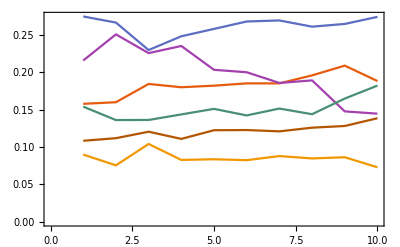

```mathematica
ListLinePlot[Transpose[Mean/@Map[First[#]&,SortBy[GatherBy[Transpose@{Transpose[realFLSf1["limb_muscle"]⟦1⟧],ageIDs⟦;;,1⟧},Last],Last@First[#]&],{2}]],PlotTheme->"Scientific",GridLines->None]
```

```mathematica
runtimes={{"cell_line",1403.07},{"Newman",1800.03},{"pbmc",1133.47},{"limb muscle",2035.84},{"marrow",1852.11},{"spleen",2175.39}};
```

```mathematica
Export["runtimes.csv",runtimes]
```

runtimes.csv